```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
data3=Import[NotebookDirectory[]<>"..\\data\\2020_Problem_D_DATA\\passingevents.csv"];
```

```mathematica
object3=Transpose[data3][[{1,2,3,4}]];
```

```mathematica
allteam=Drop[Thread[Table[object3[[i]],{i,1,4}]],1]
```

{{1,Huskies,Huskies_D1,Huskies_F1},{1,Huskies,Huskies_M1,Huskies_F2},{1,Opponent1,Opponent1_D2,Opponent1_G1},{1,Opponent1,Opponent1_G1,Opponent1_F1},{1,Huskies,Huskies_M2,Huskies_M3},23419,{38,Opponent14,Opponent14_M3,Opponent14_D1},{38,Opponent14,Opponent14_D1,Opponent14_D6},{38,Opponent14,Opponent14_D6,Opponent14_M4},{38,Opponent14,Opponent14_M4,Opponent14_M2},{38,Opponent14,Opponent14_M2,Opponent14_F1}}
 |  |  |  |

```mathematica
passmember=Drop[#,2]&/@Cases[allteam,{_,"Huskies",_,_}]
```

{{Huskies_D1,Huskies_F1},{Huskies_M1,Huskies_F2},{Huskies_M2,Huskies_M3},{Huskies_D1,Huskies_F1},{Huskies_D1,Huskies_G1},{Huskies_G1,Huskies_G1},{Huskies_D1,Huskies_D2},{Huskies_D2,Huskies_D3},{Huskies_D3,Huskies_G1},{Huskies_G1,Huskies_D3},{Huskies_D3,Huskies_G1},{Huskies_D2,Huskies_D3},{Huskies_D3,Huskies_D4},10409,{Huskies_M2,Huskies_D4},{Huskies_D4,Huskies_F6},{Huskies_F6,Huskies_D4},{Huskies_D4,Huskies_F6},{Huskies_F6,Huskies_D1},{Huskies_D1,Huskies_M1},{Huskies_M1,Huskies_M12},{Huskies_M1,Huskies_D4},{Huskies_D4,Huskies_F6},{Huskies_F6,Huskies_M2},{Huskies_M2,Huskies_M1},{Huskies_M1,Huskies_F4},{Huskies_F4,Huskies_M2}}
 |  |  |  |

```mathematica
allteamnew[match_]:=Cases[allteam,{match,_,_,_}]
```

```mathematica
allteamnew[1];
```

```mathematica
allteamfnmatchchuli[match_]:=Module[{allteamfnmatch1fn1,allteamfnmatch1fn2},

allteamfnmatch1fn1=Drop[#,2]&/@allteamnew[match];
allteamfnmatch1fn2=Drop[Flatten@allteamfnmatch1fn1,1];
Partition[allteamfnmatch1fn2,2]//PositionIndex
]
```

```mathematica
allteamfnmatchchuli[1];
```

```mathematica
samecase[match_]:=Cases[Keys[allteamfnmatchchuli[match]],{x_,x_}]
```

```mathematica
samecase[12];
```

```mathematica
numberlist[match_]:=Table[
allteamfnmatchchuli[match][samecase[match][[i]]],{i,1,samecase[match]//Length}]//Flatten//Sort
```

```mathematica
numberlist[2];
```

```mathematica
continuationnumbernew[j_]:=Append[Prepend[#,#[[1]]-1],#[[-1]]+1]&/@(Split[numberlist[j],(#2-#1==1&)]/.{_}->Nothing)
```

```mathematica
continuationnumbernew[4];
```

```mathematica
Position[<|{"Huskies_F1","Huskies_M1"}->{1,214,353},{"Huskies_F2","Opponent1_D2"}->{2,282},{"Opponent1_G1","Opponent1_G1"}->{3,50,148,347,359,488,500,517,527,531},{"Opponent1_F1","Huskies_M2"}->{4,113},{"Huskies_M3","Opponent1_D1"}->{5},{"Opponent1_F2","Opponent1_F2"}->{6,48,65,74,128,219,260,268,295,305,384}|>,2]
```

{{Key[{Huskies_F2,Opponent1_D2}],1}}

```mathematica
result[match_]:=If[#[[1]]==0,List@allteamnew[match][[1]][[4]],List@Position[allteamfnmatchchuli[match],#[[1]]][[1]][[1]][[1]][[2]]]~Join~Table[Position[allteamfnmatchchuli[match],#[[i]]][[1]][[1]][[1]][[1]],{i,2,Length@#-1}]~Join~If[#[[-1]]==Length@allteamnew[match],List@allteamnew[match][[-1]][[4]],List@Position[allteamfnmatchchuli[match],#[[-1]]][[1]][[1]][[1]][[2]]]&/@continuationnumbernew[match]
```

```mathematica
resultunion[match_]:=Union/@result[match];
```

```mathematica
(*Table[Histogram[Length@#&/@resultunion[i],50,Axes->True],{i,1,38}]*)
```

```mathematica
skill[match_,core_]:=Select[resultunion[match],Length[#]==core&]
```

```mathematica
skill[1,3]
```

{{Huskies_D1,Huskies_M3,Opponent1_M2},{Huskies_D1,Huskies_D3,Huskies_F1},{Huskies_F2,Huskies_M1,Opponent1_F2},{Huskies_M1,Huskies_M3,Huskies_M4},{Opponent1_D2,Opponent1_D4,Opponent1_G1},{Opponent1_D1,Opponent1_D2,Opponent1_M1},{Opponent1_F3,Opponent1_M1,Opponent1_M3}}

```mathematica
(*myteamskill[match_,core_]:=Cases[skill[match,core],{x_,y_,___,z_}/;MemberQ[StringPart[x,Table[i,{i,1,7}]],"H"]&&MemberQ[StringPart[y,Table[i,{i,1,7}]],"H"]&&MemberQ[StringPart[z,Table[i,{i,1,7}]],"H"]]*)
```

```mathematica
myteamskill[match_]:=Cases[result[match],{x_,y_,___,z_}/;MemberQ[StringPart[x,Table[i,{i,1,7}]],"H"]&&MemberQ[StringPart[y,Table[i,{i,1,7}]],"H"]&&MemberQ[StringPart[z,Table[i,{i,1,7}]],"H"]]
```

```mathematica
myteamunionskill[match_]:=Cases[resultunion[match],{x_,y_,___,z_}/;MemberQ[StringPart[x,Table[i,{i,1,7}]],"H"]&&MemberQ[StringPart[y,Table[i,{i,1,7}]],"H"]&&MemberQ[StringPart[z,Table[i,{i,1,7}]],"H"]]
```

```mathematica
opponetunionskill[match_]:=Cases[resultunion[match],{x_,y_,___,z_}/;MemberQ[StringPart[x,Table[i,{i,1,7}]],"O"]&&MemberQ[StringPart[y,Table[i,{i,1,7}]],"O"]&&MemberQ[StringPart[z,Table[i,{i,1,7}]],"O"]]
```

```mathematica
(*myteamtrueskill[match_,core_]:=result[match][[Position[resultunion[match],#]&/@myteamskill[match,core]//Flatten]]*)
```

```mathematica
drawgraph[member_]:=Graph[Rule@@@Partition[member,2,1],GraphLayout->"CircularEmbedding"]
```

## 分布图

```mathematica
ParallelTable[Histogram[Length@#&/@myteamunionskill[i]],{i,1,38}];
```

# MEMBER

```mathematica
test=result[1];
```

```mathematica
allmember=Table["Huskies_"<>"F"<>ToString[i],{i,1,6}]~Join~Table["Huskies_"<>"M"<>ToString[i],{i,1,13}]~Join~
Table["Huskies_"<>"D"<>ToString[i],{i,1,10}]~Join~
Table["Huskies_"<>"G"<>ToString[i],{i,1,1}];
```

```mathematica
allmemberlist=Table[List[allmember[[i]],allmember[[j]]],{i,1,30},{j,1,30}];
```

# 38 场集合

```mathematica
allmatchmyteamskill=Flatten[Table[myteamskill[i],{i,1,38}],1];
```

```mathematica
allmatchmyteamskill//Length
```

```mathematica
allmatchmyteamskill[[8]]
```

{Huskies_F3,Huskies_D3,Huskies_G1,Huskies_F2}

```mathematica
Position[{{1},2,3,{1,3},{}},x:{__}/;MemberQ[x,1]]
```

{{1},{4}}

```mathematica
memberindex[member1_,member2_]:=Position[allmatchmyteamskill,x:{___}/;MemberQ[x,member1]&&MemberQ[x,member2]]
```

```mathematica
memberindex["Huskies_M2","Huskies_M1"]
```

{{4},{5},{6},{7},{9},{12},{17},{35},{47},{49},{83},{84},{86},{538},{542}}

```mathematica
allmatchmemberskill[member1_,member2_]:=Extract[allmatchmyteamskill,memberindex[member1,member2]]
```

```mathematica
test=allmatchmemberskill["Huskies_M6","Huskies_D5"];
```

```mathematica
Counts@Flatten@test//Sort
```

<|Huskies_M5→1,Huskies_F3→1,Huskies_M12→2,Huskies_M2→3,Huskies_F5→3,Huskies_M11→5,Huskies_F4→5,Huskies_D8→5,Huskies_M10→6,Huskies_M9→7,Huskies_M13→8,Huskies_M8→9,Huskies_F1→9,Huskies_D3→10,Huskies_F6→12,Huskies_G1→13,Huskies_D4→14,Huskies_D6→18,Huskies_D1→19,Huskies_D7→24,Huskies_D2→27,Huskies_M4→29,Huskies_M3→30,Huskies_F2→46,Huskies_M6→70,Huskies_M1→71,Huskies_D5→83|>

```mathematica
test
```

{{Huskies_D4,Huskies_M2,Huskies_M6,Huskies_M2,Huskies_D4,Huskies_F2,Huskies_M1,Huskies_D5,Huskies_F2,Huskies_D5,Huskies_D2},{Huskies_M1,Huskies_M2,Huskies_D5,Huskies_F2,Huskies_M1,Huskies_M6,Huskies_D4,Huskies_D5},{Huskies_M1,Huskies_M6,Huskies_D4,Huskies_D5,Huskies_M3,Huskies_M1,Huskies_D4,Huskies_M6},{Huskies_D4,Huskies_M6,Huskies_D1,Huskies_D5,Huskies_M4},{Huskies_M3,Huskies_M6,Huskies_M4,Huskies_D4,Huskies_D5},{Huskies_D2,Huskies_D1,Huskies_D5,Huskies_D1,Huskies_D2,Huskies_M3,Huskies_D4,Huskies_M3,Huskies_D4,Huskies_M6},{Huskies_D2,Huskies_M1,Huskies_M4,Huskies_F2,Huskies_M6,Huskies_D4,Huskies_M6,Huskies_M3,Huskies_M1,Huskies_F2,Huskies_D2,Huskies_D1,Huskies_D5,Huskies_F2,Huskies_M1,Huskies_D3,Huskies_D2,Huskies_D3,Huskies_D2},{Huskies_D5,Huskies_M5,Huskies_F3,Huskies_M6,Huskies_M3,Huskies_M3},{Huskies_M1,Huskies_D5,Huskies_M3,Huskies_M1,Huskies_F2,Huskies_M6,Huskies_D5,Huskies_F2,Huskies_M6},{Huskies_M1,Huskies_D4,Huskies_M1,Huskies_F2,Huskies_D5,Huskies_M1,Huskies_D6,Huskies_M3,Huskies_M1,Huskies_D4,Huskies_M1,Huskies_M6,Huskies_M1,Huskies_M3},{Huskies_M3,Huskies_M1,Huskies_D5,Huskies_D1,Huskies_D2,Huskies_D4,Huskies_D2,Huskies_M6},{Huskies_M1,Huskies_M9,Huskies_D5,Huskies_M6},{Huskies_M1,Huskies_D5,Huskies_M1,Huskies_F2,Huskies_M6,Huskies_M4},{Huskies_F2,Huskies_D4,Huskies_M4,Huskies_M1,Huskies_D5,Huskies_D2,Huskies_D5,Huskies_D2,Huskies_G1,Huskies_M6},{Huskies_D5,Huskies_F2,Huskies_M1,Huskies_M4,Huskies_M6,Huskies_M8,Huskies_M4,Huskies_D7,Huskies_D6},{Huskies_M1,Huskies_M6,Huskies_M8,Huskies_D5,Huskies_M6,Huskies_M8,Huskies_M1,Huskies_F2,Huskies_D6,Huskies_D7},{Huskies_M1,Huskies_M8,Huskies_M1,Huskies_M4,Huskies_D7,Huskies_M4,Huskies_M1,Huskies_M4,Huskies_M1,Huskies_D6,Huskies_D2,Huskies_D5,Huskies_M8,Huskies_F2,Huskies_D5,Huskies_M6,Huskies_M6},{Huskies_D7,Huskies_M11,Huskies_D6,Huskies_D5,Huskies_M10,Huskies_D5,Huskies_D2,Huskies_D6,Huskies_M11,Huskies_M9,Huskies_M11,Huskies_M1,Huskies_M6,Huskies_M1,Huskies_M10,Huskies_M11,Huskies_D6,Huskies_D7,Huskies_D6,Huskies_M1,Huskies_D5,Huskies_M9,Huskies_D5,Huskies_M11,Huskies_M4,Huskies_D7,Huskies_D6,Huskies_G1,Huskies_D2,Huskies_D5,Huskies_M10,Huskies_M6},{Huskies_F2,Huskies_D5,Huskies_M6,Huskies_M4},{Huskies_D2,Huskies_F2,Huskies_M6,Huskies_M4,Huskies_D5,Huskies_M4},{Huskies_M6,Huskies_M4,Huskies_D6,Huskies_D5},{Huskies_M1,Huskies_G1,Huskies_D5,Huskies_M6,Huskies_F1},{Huskies_M1,Huskies_D5,Huskies_F2,Huskies_M8,Huskies_M6},{Huskies_D2,Huskies_D6,Huskies_M1,Huskies_D7,Huskies_M4,Huskies_D7,Huskies_M6,Huskies_M4,Huskies_M1,Huskies_F2,Huskies_D5,Huskies_D2,Huskies_M1,Huskies_D6,Huskies_D7,Huskies_M4,Huskies_M1,Huskies_M6,Huskies_M1,Huskies_F2,Huskies_M6,Huskies_M4,Huskies_F2,Huskies_D2},{Huskies_G1,Huskies_F1,Huskies_M6,Huskies_D5,Huskies_D2,Huskies_M10,Huskies_D1,Huskies_D7,Huskies_D1,Huskies_D6,Huskies_D2,Huskies_D5,Huskies_M1,Huskies_M10,Huskies_M3},{Huskies_D5,Huskies_F2,Huskies_D5,Huskies_M6,Huskies_D5},{Huskies_M3,Huskies_D5,Huskies_M6,Huskies_M3,Huskies_D6,Huskies_D7,Huskies_F2},{Huskies_F1,Huskies_D5,Huskies_M6,Huskies_D5,Huskies_F1,Huskies_F2,Huskies_M1,Huskies_D5,Huskies_M4},{Huskies_M1,Huskies_D6,Huskies_M1,Huskies_M4,Huskies_M8,Huskies_M4,Huskies_F1,Huskies_D5,Huskies_M6,Huskies_M1},{Huskies_M1,Huskies_F2,Huskies_D5,Huskies_M4,Huskies_M1,Huskies_F2,Huskies_D7,Huskies_D2,Huskies_F2,Huskies_D5,Huskies_M6,Huskies_F2,Huskies_M10},{Huskies_M6,Huskies_D5,Huskies_D3,Huskies_M3,Huskies_D3},{Huskies_D1,Huskies_G1,Huskies_F1,Huskies_D5,Huskies_D3,Huskies_G1,Huskies_M6},{Huskies_G1,Huskies_M3,Huskies_D5,Huskies_M6,Huskies_M3,Huskies_D1,Huskies_D7,Huskies_D1},{Huskies_G1,Huskies_M3,Huskies_D5,Huskies_M3,Huskies_M6,Huskies_D5,Huskies_M6,Huskies_M6},{Huskies_F1,Huskies_D2,Huskies_D5,Huskies_M3,Huskies_D7,Huskies_M3,Huskies_D1,Huskies_D7,Huskies_M3,Huskies_M6},{Huskies_D6,Huskies_M4,Huskies_M6,Huskies_M3,Huskies_M12,Huskies_M3,Huskies_D5,Huskies_D6},{Huskies_G1,Huskies_D1,Huskies_M6,Huskies_D5,Huskies_F4},{Huskies_D1,Huskies_F4,Huskies_D5,Huskies_M6},{Huskies_D5,Huskies_F1,Huskies_M1,Huskies_M8,Huskies_D7,Huskies_M8,Huskies_M1,Huskies_M3,Huskies_M1,Huskies_M3,Huskies_D3,Huskies_M6,Huskies_M3,Huskies_M13,Huskies_D5},{Huskies_M13,Huskies_M6,Huskies_D5,Huskies_D3,Huskies_G1,Huskies_M1},{Huskies_M1,Huskies_M13,Huskies_M6,Huskies_D5,Huskies_M6,Huskies_M13,Huskies_M3,Huskies_D5},{Huskies_M13,Huskies_D5,Huskies_M13,Huskies_M3,Huskies_M6,Huskies_D5,Huskies_D7},{Huskies_M1,Huskies_M6,Huskies_D5,Huskies_D3,Huskies_M13},{Huskies_D5,Huskies_F2,Huskies_M13,Huskies_M1,Huskies_M6,Huskies_D5,Huskies_M1,Huskies_F2,Huskies_D3},{Huskies_D6,Huskies_M9,Huskies_M6,Huskies_D5,Huskies_F6},{Huskies_M9,Huskies_M6,Huskies_M9,Huskies_D5,Huskies_M3,Huskies_F6,Huskies_F5},{Huskies_M6,Huskies_D5,Huskies_M6,Huskies_M9,Huskies_D7},{Huskies_F4,Huskies_M12,Huskies_D5,Huskies_M6},{Huskies_F2,Huskies_D5,Huskies_F4,Huskies_M6},{Huskies_M1,Huskies_M6,Huskies_D5,Huskies_M1,Huskies_D1,Huskies_D3,Huskies_D1,Huskies_M4,Huskies_D1,Huskies_F6,Huskies_D8,Huskies_D5},{Huskies_M1,Huskies_D8,Huskies_F6,Huskies_M1,Huskies_D8,Huskies_D5,Huskies_M4,Huskies_F2,Huskies_M1,Huskies_F6,Huskies_D1,Huskies_F2,Huskies_M6,Huskies_F4,Huskies_M4,Huskies_F6,Huskies_D5,Huskies_F2,Huskies_D1,Huskies_D1},{Huskies_D2,Huskies_F2,Huskies_D5,Huskies_F6,Huskies_D5,Huskies_F6,Huskies_M6},{Huskies_F6,Huskies_M6,Huskies_F6,Huskies_D7,Huskies_F2,Huskies_D7,Huskies_F2,Huskies_M1,Huskies_M4,Huskies_M6,Huskies_D5,Huskies_M1,Huskies_F2,Huskies_M1,Huskies_D7},{Huskies_D5,Huskies_M6,Huskies_D5,Huskies_F2,Huskies_D2,Huskies_D7},{Huskies_M1,Huskies_D5,Huskies_M1,Huskies_M6,Huskies_M1,Huskies_D7,Huskies_M1,Huskies_F2},{Huskies_D2,Huskies_G1,Huskies_F2,Huskies_G1,Huskies_D2,Huskies_M1,Huskies_F2,Huskies_D5,Huskies_F2,Huskies_M1,Huskies_M4,Huskies_M1,Huskies_M6,Huskies_D7,Huskies_M1,Huskies_F6,Huskies_G1},{Huskies_F2,Huskies_F5,Huskies_D5,Huskies_F5,Huskies_F2,Huskies_D8,Huskies_F6,Huskies_D8,Huskies_F2,Huskies_D2,Huskies_F2,Huskies_M1,Huskies_D5,Huskies_F1,Huskies_D5,Huskies_M6,Huskies_M1}}

IsomorphicGraphQ::ngen: 未实现广义 IsomorphicGraphQ[Graph[<7>, <9>], Graph[<7>, <9>]].

Union::smtst: SameTest 函数的应用产生 …，它计算得到 …. 在每个元素对，SameTest 函数必须计算得到 True 或者 False.

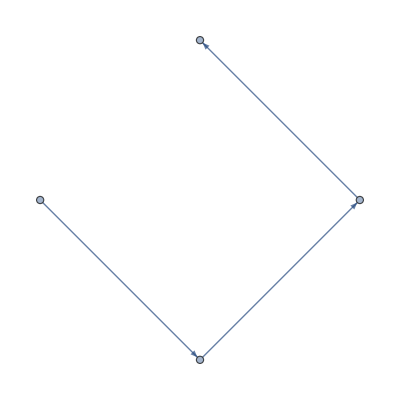
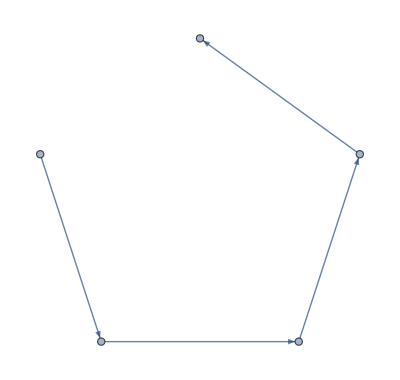
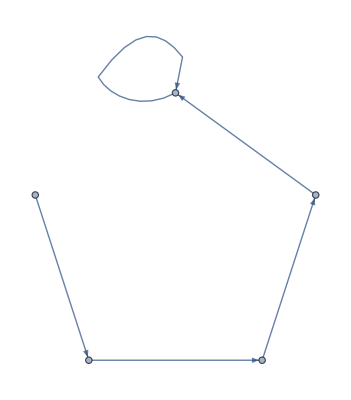
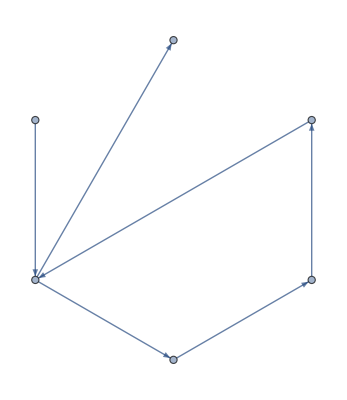
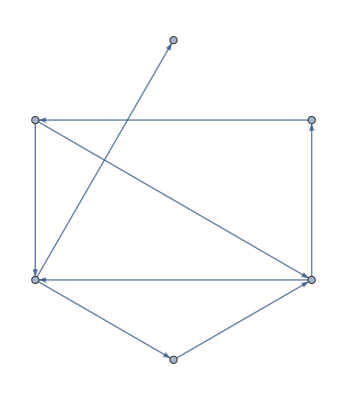
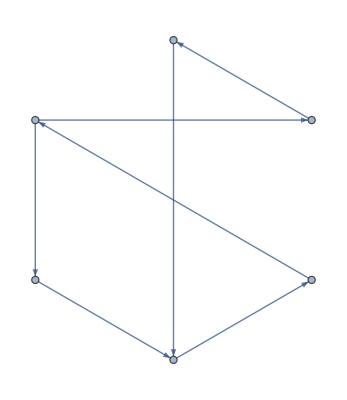
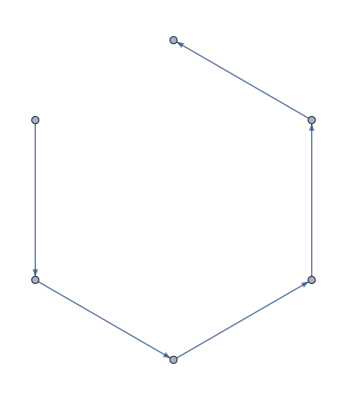
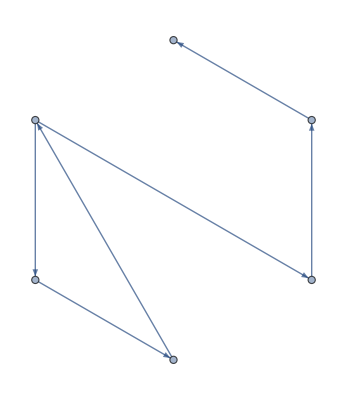
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Union[drawgraph/@test,SameTest->(IsomorphicGraphQ[#1,#2]&)]
```

```mathematica
Union/@test;
```

# 传球次数

1

```mathematica
Permutations[{"Huskies_F2","Huskies_M1","Huskies_M3"},{2}]
```

```mathematica
{{54.534563282610804,48.06674490419984},{50.24932795856887,52.42233426177297},{46.657884143973305,46.37149811550381}}
```

{{Huskies_F2,Huskies_M1},{Huskies_F2,Huskies_M3},{Huskies_M1,Huskies_F2},{Huskies_M1,Huskies_M3},{Huskies_M3,Huskies_F2},{Huskies_M3,Huskies_M1}}

```mathematica
Thread[DirectedEdge@@@{{"Huskies_F2","Huskies_M1"},{"Huskies_F2","Huskies_M3"},{"Huskies_M1","Huskies_F2"},{"Huskies_M1","Huskies_M3"},{"Huskies_M3","Huskies_F2"},{"Huskies_M3","Huskies_M1"}}->(AbsoluteThickness[#]&/@({117,58,182,143,63,168}/34))]
```

{Huskies_F2->Huskies_M1→AbsoluteThickness[117/34],Huskies_F2->Huskies_M3→AbsoluteThickness[29/17],Huskies_M1->Huskies_F2→AbsoluteThickness[91/17],Huskies_M1->Huskies_M3→AbsoluteThickness[143/34],Huskies_M3->Huskies_F2→AbsoluteThickness[63/34],Huskies_M3->Huskies_M1→AbsoluteThickness[84/17]}

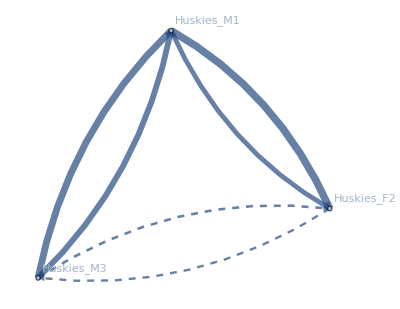

```mathematica
graph1=Graph[Rule@@@{{"Huskies_F2","Huskies_M1"},{"Huskies_F2","Huskies_M3"},{"Huskies_M1","Huskies_F2"},{"Huskies_M1","Huskies_M3"},{"Huskies_M3","Huskies_F2"},{"Huskies_M3","Huskies_M1"}},VertexCoordinates->{{54.534563282610804,48.06674490419984},{50.24932795856887,52.42233426177297},{46.657884143973305,46.37149811550381}},EdgeStyle->{"Huskies_F2"->"Huskies_M1"->AbsoluteThickness[117/34],"Huskies_F2"->"Huskies_M3"->{Dashed,AbsoluteThickness[58/34]},"Huskies_M1"->"Huskies_F2"->AbsoluteThickness[182/34],"Huskies_M1"->"Huskies_M3"->AbsoluteThickness[143/34],"Huskies_M3"->"Huskies_F2"->{Dashed,AbsoluteThickness[63/34]},"Huskies_M3"->"Huskies_M1"->AbsoluteThickness[168/34]},
EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.06}],
VertexLabels->"Name"]
```

```mathematica
graph//VertexList
```

{Huskies_F2,Huskies_M1,Huskies_M3}

```mathematica
Counts[passmember][[Key[#]]]&/@Permutations[{"Huskies_F2","Huskies_M1","Huskies_M3"},{2}]
```

{117,58,182,143,63,168}

2

```mathematica
Thread[DirectedEdge@@@{{"Huskies_M1","Huskies_M3"},{"Huskies_M1","Huskies_D1"},{"Huskies_M3","Huskies_M1"},{"Huskies_M3","Huskies_D1"},{"Huskies_D1","Huskies_M1"},{"Huskies_D1","Huskies_M3"}}->(AbsoluteThickness[#]&/@({143,85,168,74,92,51}/34))]
```

{Huskies_M1->Huskies_M3→AbsoluteThickness[143/34],Huskies_M1->Huskies_D1→AbsoluteThickness[5/2],Huskies_M3->Huskies_M1→AbsoluteThickness[84/17],Huskies_M3->Huskies_D1→AbsoluteThickness[37/17],Huskies_D1->Huskies_M1→AbsoluteThickness[46/17],Huskies_D1->Huskies_M3→AbsoluteThickness[3/2]}

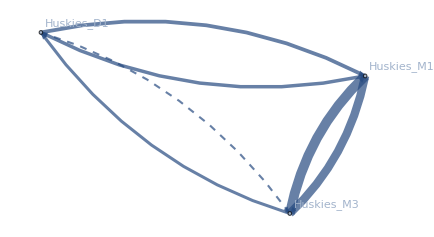

```mathematica
graph2=Graph[Rule@@@{{"Huskies_M1","Huskies_M3"},{"Huskies_M1","Huskies_D1"},{"Huskies_M3","Huskies_M1"},{"Huskies_M3","Huskies_D1"},{"Huskies_D1","Huskies_M1"},{"Huskies_D1","Huskies_M3"}},EdgeStyle->{"Huskies_M1"->"Huskies_M3"->AbsoluteThickness[143/24],"Huskies_M1"->"Huskies_D1"->AbsoluteThickness[5/2],"Huskies_M3"->"Huskies_M1"->AbsoluteThickness[84/12],"Huskies_M3"->"Huskies_D1"->AbsoluteThickness[37/17],"Huskies_D1"->"Huskies_M1"->AbsoluteThickness[46/17],"Huskies_D1"->"Huskies_M3"->{Dashed,AbsoluteThickness[3/2]}},
VertexCoordinates->{{50.24932795856887,52.42233426177297},{46.657884143973305,46.37149811550381},{34.79909112652476,54.33448849002909}},
EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.06}],
VertexLabels->"Name"]
```

```mathematica
VertexList[graph2]
```

{Huskies_M1,Huskies_M3,Huskies_D1}

```mathematica
Permutations[{"Huskies_M1","Huskies_M3","Huskies_D1"},{2}]
```

{{Huskies_M1,Huskies_M3},{Huskies_M1,Huskies_D1},{Huskies_M3,Huskies_M1},{Huskies_M3,Huskies_D1},{Huskies_D1,Huskies_M1},{Huskies_D1,Huskies_M3}}

```mathematica
Counts[passmember][[Key[#]]]&/@Permutations[{"Huskies_M1","Huskies_M3","Huskies_D1"},{2}]
```

{143,85,168,74,92,51}

3

```mathematica
Thread[DirectedEdge@@@{{"Huskies_M6","Huskies_D5"},{"Huskies_M6","Huskies_M1"},{"Huskies_D5","Huskies_M6"},{"Huskies_D5","Huskies_M1"},{"Huskies_M1","Huskies_M6"},{"Huskies_M1","Huskies_D5"}}->(AbsoluteThickness[#]&/@({71,54,67,75,77,79}/34))]
```

{Huskies_M6->Huskies_D5→AbsoluteThickness[71/34],Huskies_M6->Huskies_M1→AbsoluteThickness[27/17],Huskies_D5->Huskies_M6→AbsoluteThickness[67/34],Huskies_D5->Huskies_M1→AbsoluteThickness[75/34],Huskies_M1->Huskies_M6→AbsoluteThickness[77/34],Huskies_M1->Huskies_D5→AbsoluteThickness[79/34]}

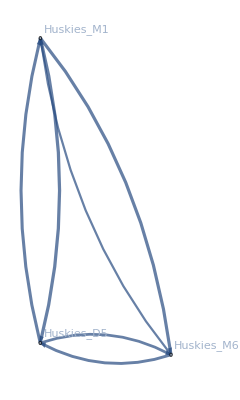

```mathematica
graph3=Graph[Rule@@@{{"Huskies_M6","Huskies_D5"},{"Huskies_M6","Huskies_M1"},{"Huskies_D5","Huskies_M6"},{"Huskies_D5","Huskies_M1"},{"Huskies_M1","Huskies_M6"},{"Huskies_M1","Huskies_D5"}},EdgeStyle->{"Huskies_M6"->"Huskies_D5"->AbsoluteThickness[71/34],"Huskies_M6"->"Huskies_M1"->AbsoluteThickness[27/17],"Huskies_D5"->"Huskies_M6"->AbsoluteThickness[67/34],"Huskies_D5"->"Huskies_M1"->AbsoluteThickness[75/34],"Huskies_M1"->"Huskies_M6"->AbsoluteThickness[77/34],"Huskies_M1"->"Huskies_D5"->AbsoluteThickness[79/34]},
VertexCoordinates->{{59.57960710567603,35.035165471634485},{50.23899208261618,35.6850726333907},{50.24932795856887,52.42233426177297}},
EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.06}],
VertexLabels->"Name"]
```

```mathematica
VertexList[graph3]
```

{Huskies_M6,Huskies_D5,Huskies_M1}

```mathematica
Permutations[{"Huskies_M6","Huskies_D5","Huskies_M1"},{2}]
```

{{Huskies_M6,Huskies_D5},{Huskies_M6,Huskies_M1},{Huskies_D5,Huskies_M6},{Huskies_D5,Huskies_M1},{Huskies_M1,Huskies_M6},{Huskies_M1,Huskies_D5}}

```mathematica
Counts[passmember][[Key[#]]]&/@Permutations[{"Huskies_M6","Huskies_D5","Huskies_M1"},{2}]
```

{71,54,67,75,77,79}

# 处理

```mathematica
test=({{0., 0.10041092467920383, 0.006653821783265927, 0.006379849715308255, 0.026712675654160998, 0.002762778363934057, 0.09086125503207085, 0.005049084687062756, 0.021488625076363125, 0.05442260995207811, 0.0018768864495934668, 0.05847131450156233, 0.00009192869729603767, 0.00313140552621709, 0.029870836708642278, 0.010821371557716217, 0.0021183881223285263, 0.00144281883598638, 0.002886393295838601, 0.003317185571918887, 0.0033165878925446863, 0.005139077737370625, 0.00023141383818841587, 0.03048204957445712, 0.00018718308283783525, 0.001343388969885662, 0.00008863546219969202, 0.00013272601463346144, 0., 0.}, {0.10041092467920383, 0., 0.01852388393923212, 0.018733062482571432, 0.04121765353260088, 0.019952512476965528, 0.3664521675904726, 0.00274386835293509, 0.14885804076633005, 0.18122775280311545, 0.014947569594389773, 0.11651659299194113, 0.0022873354111668047, 0.003278640210041935, 0.02308183630785447, 0.005593018966048395, 0.010288978545875549, 0.007659419962728391, 0.0004873571561773025, 0.0524873426533588, 0.046304026822676064, 0.06356973550945609, 0.0056561222509411094, 0.2291772918918727, 0.005713137079379665, 0.002165948391578891, 0.0003862386819430668, 0.002027298048503003, 0.00008756497003371103, 0.0003514970293887215}, {0.006653821783265927, 0.01852388393923212, 0., 0.006039755475115026, 0., 0., 0.01931856495254461, 0.0005598256412559674, 0.0029312422137967756, 0.003553778797883056, 0.0008917864622340634, 0.005667573736902002, 0.00018818432066672816, 0., 0., 0., 0.0008917771626519767, 0., 0., 0.0018344944043027199, 0.00048290301700407227, 0.0014554662912390909, 0.0000217942098918213, 0.0024067943350636277, 0.00017102556364058816, 0.0001122690359898186, 0., 0., 0., 0.}, {0.006379849715308255, 0.018733062482571432, 0.006039755475115026, 0., 0.0042925085884082835, 0.005641087606373591, 0.03204515343885705, 0.007698061794846386, 0.009511812502410266, 0.043276676534012015, 0., 0.015971402718266633, 0., 0.0004069290391799704, 0.011304257229577582, 0.0036215786964122424, 0.0009516031852483485, 0.003504485166426012, 0.001140266582727368, 0.001477806045266946, 0.0007723978604102957, 0.0010270492514865336, 0.0003892429193422378, 0.013900452745804974, 0.00001259055271320352, 0.00046010000542864014, 0.0001130193321459748, 0.00031059772198783445, 9.732827385619045*^-6, 0.}, {0.026712675654160998, 0.04121765353260088, 0., 0.0042925085884082835, 0., 0.0036733060853302215, 0.01452780683583716, 0.0017591079127140647, 0.014378051871916769, 0.021675698439221812, 0., 0.035783681163525545, 0., 0., 0.004928350897030667, 0., 0.0023926140411798208, 0.010722796119882276, 0.005469073109648489, 0.002440585501117281, 0.00041516629104041195, 0.003154427245333271, 0.0028623154174344436, 0.010194579468268686, 0.00004315156838041493, 0.00004339435341430495, 0., 0.0001081136781965379, 0.00012797809444966567, 0.}, {0.002762778363934057, 0.019952512476965528, 0., 0.005641087606373591, 0.0036733060853302215, 0., 0.02125762848285167, 0.00016276765770552014, 0.004835145160738012, 0.020144818477351854, 0., 0.0003438609375333479, 0., 0., 0.004011476808456522, 0., 0.001334346844242479, 0.000041736125654606926, 0.001387383841165259, 0.0027257165452703163, 0.0002065837467649145, 0.0019106628287640357, 0., 0.0008655464513107428, 0.0016173634696235702, 0.014010011575829057, 0.026159198384954736, 0.00010285698078038004, 0., 0.}, {0.09086125503207085, 0.3664521675904726, 0.01931856495254461, 0.03204515343885705, 0.01452780683583716, 0.02125762848285167, 0., 0.04778057929942155, 0.316164472715174, 0.2319027539601145, 0.009778620526690459, 0.04880521751143648, 0.0021887975970492917, 0.010505853276649347, 0.029301331053052014, 0.02275960135617583, 0.004744336064794631, 0.003280689306490795, 0.017187711570152222, 0.1637424943640313, 0.10528636215679049, 0.17963898016828278, 0.0015681916784439224, 0.15936875566936237, 0.027620481892938503, 0.01173421751638587, 0.005811628391653245, 0.002312934185628423, 0.000840853853788609, 0.0024561584197772277}, {0.005049084687062756, 0.00274386835293509, 0.0005598256412559674, 0.007698061794846386, 0.0017591079127140647, 0.00016276765770552014, 0.04778057929942155, 0., 0.023166676178515686, 0.006838384420414044, 0., 0.0029683104690708256, 0., 0., 0., 0., 0., 0.00007401992751844808, 0., 0.002653377282627293, 0.0012857633292164652, 0.002637715277749506, 0.0003519424685855553, 0.005204165080446868, 0.00014613287668220143, 0., 0.00003017084909996251, 0., 0.000013979059615745911, 0.000015356079038115466}, {0.021488625076363125, 0.14885804076633005, 0.0029312422137967756, 0.009511812502410266, 0.014378051871916769, 0.004835145160738012, 0.316164472715174, 0.023166676178515686, 0., 0.08621603555732092, 0.000964285429772305, 0.04910272399815124, 0., 0.003227835962751458, 0.011741237123894395, 0.008984099937716771, 0.005978758647857517, 0.009318971633152609, 0.02253303697580695, 0.11372221132169631, 0.1258856269261076, 0.1493774275671851, 0.005530003186263876, 0.19783786775963624, 0.009172729749691081, 0.0016159869820679324, 0.00019016548841444084, 0.007608839755567097, 0.0011871015314149692, 0.0044815415292934115}, {0.05442260995207811, 0.18122775280311545, 0.003553778797883056, 0.043276676534012015, 0.021675698439221812, 0.020144818477351854, 0.2319027539601145, 0.006838384420414044, 0.08621603555732092, 0., 0.007894329451153946, 0.02340228868324047, 0., 0.004525229033943937, 0.023419230627300714, 0.003965817956065706, 0.013739071889371037, 0.0017333732371882116, 0.003238173802683337, 0.025968930611667905, 0.012384303194434733, 0.030538967348803417, 0.0006640169568550746, 0.03737200457856286, 0.005862411673581275, 0.013009713615550212, 0.006415898247628262, 0.0009888155561944114, 0.00019411220608223307, 0.}, {0.0018768864495934668, 0.014947569594389773, 0.0008917864622340634, 0., 0., 0., 0.009778620526690459, 0., 0.000964285429772305, 0.007894329451153946, 0., 0.0012600022599631288, 0., 0.0002836929625069779, 0., 0., 0., 0., 0., 0.00012178785040856382, 0.0008673497995910431, 0.0012329058937305246, 0.0005226346349550729, 0.0007810992117328058, 0., 0.00003743163691126874, 0., 0., 0., 0.}, {0.05847131450156233, 0.11651659299194113, 0.005667573736902002, 0.015971402718266633, 0.035783681163525545, 0.0003438609375333479, 0.04880521751143648, 0.0029683104690708256, 0.04910272399815124, 0.02340228868324047, 0.0012600022599631288, 0., 0.0005630029573694621, 0.0004541482233127323, 0.005059376009214481, 0.0051688645668367585, 0.0014545280800146003, 0.010448017597100427, 0.016482546686139198, 0.008083815243747683, 0.011118897293971808, 0.010629573066369918, 0.010788143282098078, 0.25672904460362644, 0., 0., 0.00007702068456722764, 0., 0., 0.}, {0.00009192869729603767, 0.0022873354111668047, 0.00018818432066672816, 0., 0., 0., 0.0021887975970492917, 0., 0., 0., 0., 0.0005630029573694621, 0., 0., 0., 0., 0., 0., 0., 0.0013104073928555708, 0.0005763055837270732, 0.0018889886521464769, 1.8216935084926136*^-6, 0., 0.0005440964005452695, 0., 0., 0., 0., 0.000013011462669210847}, {0.00313140552621709, 0.003278640210041935, 0., 0.0004069290391799704, 0., 0., 0.010505853276649347, 0., 0.003227835962751458, 0.004525229033943937, 0.0002836929625069779, 0.0004541482233127323, 0., 0., 0.004157919929109783, 0.0010863604828310282, 0.00007680774640602763, 0., 0.0008605709097783236, 0.0006585876958455351, 0.0001776139173925491, 0.0010397574650257801, 0., 0.0005333426697602115, 0.0067721685305556605, 0.058408431295179586, 0., 0., 0., 0.0000355223512049087}, {0.029870836708642278, 0.02308183630785447, 0., 0.011304257229577582, 0.004928350897030667, 0.004011476808456522, 0.029301331053052014, 0., 0.011741237123894395, 0.023419230627300714, 0., 0.005059376009214481, 0., 0.004157919929109783, 0., 0.0009393834688512858, 0.001346359823710714, 0.0005367227280314773, 0.013287501301006284, 0.0025006339072602335, 0.0026317951826404272, 0.002408763871050586, 0.00006383608940091495, 0.005472999334499147, 0.005257532697393938, 0.0013913339093016889, 0.0007106214227671716, 0., 8.774889838409596*^-7, 0.000029015549680053633}, {0.010821371557716217, 0.005593018966048395, 0., 0.0036215786964122424, 0., 0., 0.02275960135617583, 0., 0.008984099937716771, 0.003965817956065706, 0., 0.0051688645668367585, 0., 0.0010863604828310282, 0.0009393834688512858, 0., 0.0008582776639122471, 0., 0., 0.0009018008102165164, 0.0006196727863209009, 0.0011340315555296548, 2.5314943499633534*^-6, 0.003618679173374756, 0.00048179933328409394, 0.0009740951374481584, 0., 0., 0., 5.3118552497239986*^-6}, {0.0021183881223285263, 0.010288978545875549, 0.0008917771626519767, 0.0009516031852483485, 0.0023926140411798208, 0.001334346844242479, 0.004744336064794631, 0., 0.005978758647857517, 0.013739071889371037, 0., 0.0014545280800146003, 0., 0.00007680774640602763, 0.001346359823710714, 0.0008582776639122471, 0., 0., 0., 0.003527655260737455, 0.0011777088898586446, 0.014843028126067019, 0.00011402909760127853, 0.001983811689061777, 0.0001758249102497693, 0.0020456244703659734, 0.0004388811234877249, 0., 0.00012080127710680624, 0.0000294815708441368}, {0.00144281883598638, 0.007659419962728391, 0., 0.003504485166426012, 0.010722796119882276, 0.000041736125654606926, 0.003280689306490795, 0.00007401992751844808, 0.009318971633152609, 0.0017333732371882116, 0., 0.010448017597100427, 0., 0., 0.0005367227280314773, 0., 0., 0., 0.0004238179062703307, 0.0000735880676947167, 0.0006509679779611675, 0.0007015464711061754, 0.00800520987752123, 0.029812638664350966, 0.00005473460218176379, 0., 0., 0.0008438915988908253, 0., 0.}, {0.002886393295838601, 0.0004873571561773025, 0., 0.001140266582727368, 0.005469073109648489, 0.001387383841165259, 0.017187711570152222, 0., 0.02253303697580695, 0.003238173802683337, 0., 0.016482546686139198, 0., 0.0008605709097783236, 0.013287501301006284, 0., 0., 0.0004238179062703307, 0., 0.001460307675704651, 0.0028932474742792516, 0.0038930644645186457, 0., 0.02433013520587126, 0.0008556918496609243, 0.0002660816347347734, 0., 0., 0., 0.}, {0.003317185571918887, 0.0524873426533588, 0.0018344944043027199, 0.001477806045266946, 0.002440585501117281, 0.0027257165452703163, 0.1637424943640313, 0.002653377282627293, 0.11372221132169631, 0.025968930611667905, 0.00012178785040856382, 0.008083815243747683, 0.0013104073928555708, 0.0006585876958455351, 0.0025006339072602335, 0.0009018008102165164, 0.003527655260737455, 0.0000735880676947167, 0.001460307675704651, 0., 0.09377021021652317, 0.14733871747548805, 0., 0.027462713497879602, 0.009753346117957248, 0.0027374959342259184, 0.001714449850244577, 0.0014233558001213705, 0.00038860719754535834, 0.025864091406941212}, {0.0033165878925446863, 0.046304026822676064, 0.00048290301700407227, 0.0007723978604102957, 0.00041516629104041195, 0.0002065837467649145, 0.10528636215679049, 0.0012857633292164652, 0.1258856269261076, 0.012384303194434733, 0.0008673497995910431, 0.011118897293971808, 0.0005763055837270732, 0.0001776139173925491, 0.0026317951826404272, 0.0006196727863209009, 0.0011777088898586446, 0.0006509679779611675, 0.0028932474742792516, 0.09377021021652317, 0., 0.06166500673086265, 0.0010738337911383059, 0.09971374439471159, 0.006486351154616577, 0., 0.000013674992380662017, 0.007081447614575445, 0., 0.01546442749239771}, {0.005139077737370625, 0.06356973550945609, 0.0014554662912390909, 0.0010270492514865336, 0.003154427245333271, 0.0019106628287640357, 0.17963898016828278, 0.002637715277749506, 0.1493774275671851, 0.030538967348803417, 0.0012329058937305246, 0.010629573066369918, 0.0018889886521464769, 0.0010397574650257801, 0.002408763871050586, 0.0011340315555296548, 0.014843028126067019, 0.0007015464711061754, 0.0038930644645186457, 0.14733871747548805, 0.06166500673086265, 0., 0., 0.016124257055486677, 0.008141839675079105, 0.0037096379031138454, 0.002275170342436813, 0., 0.0008828773688094724, 0.023853437677396512}, {0.00023141383818841587, 0.0056561222509411094, 0.0000217942098918213, 0.0003892429193422378, 0.0028623154174344436, 0., 0.0015681916784439224, 0.0003519424685855553, 0.005530003186263876, 0.0006640169568550746, 0.0005226346349550729, 0.010788143282098078, 1.8216935084926136*^-6, 0., 0.00006383608940091495, 2.5314943499633534*^-6, 0.00011402909760127853, 0.00800520987752123, 0., 0., 0.0010738337911383059, 0., 0., 0.010736767227733004, 0., 0., 0., 0., 0.003523595602784107, 0.000280126736500543}, {0.03048204957445712, 0.2291772918918727, 0.0024067943350636277, 0.013900452745804974, 0.010194579468268686, 0.0008655464513107428, 0.15936875566936237, 0.005204165080446868, 0.19783786775963624, 0.03737200457856286, 0.0007810992117328058, 0.25672904460362644, 0., 0.0005333426697602115, 0.005472999334499147, 0.003618679173374756, 0.001983811689061777, 0.029812638664350966, 0.02433013520587126, 0.027462713497879602, 0.09971374439471159, 0.016124257055486677, 0.010736767227733004, 0., 0.0004360910348638912, 0.0019369746566221104, 0., 0.014669009937366246, 0., 0.001915558555635025}, {0.00018718308283783525, 0.005713137079379665, 0.00017102556364058816, 0.00001259055271320352, 0.00004315156838041493, 0.0016173634696235702, 0.027620481892938503, 0.00014613287668220143, 0.009172729749691081, 0.005862411673581275, 0., 0., 0.0005440964005452695, 0.0067721685305556605, 0.005257532697393938, 0.00048179933328409394, 0.0001758249102497693, 0.00005473460218176379, 0.0008556918496609243, 0.009753346117957248, 0.006486351154616577, 0.008141839675079105, 0., 0.0004360910348638912, 0., 0.10075234336685673, 0.003138448778894797, 0., 0., 0.00023970337372423176}, {0.001343388969885662, 0.002165948391578891, 0.0001122690359898186, 0.00046010000542864014, 0.00004339435341430495, 0.014010011575829057, 0.01173421751638587, 0., 0.0016159869820679324, 0.013009713615550212, 0.00003743163691126874, 0., 0., 0.058408431295179586, 0.0013913339093016889, 0.0009740951374481584, 0.0020456244703659734, 0., 0.0002660816347347734, 0.0027374959342259184, 0., 0.0037096379031138454, 0., 0.0019369746566221104, 0.10075234336685673, 0., 0., 0., 0., 0.}, {0.00008863546219969202, 0.0003862386819430668, 0., 0.0001130193321459748, 0., 0.026159198384954736, 0.005811628391653245, 0.00003017084909996251, 0.00019016548841444084, 0.006415898247628262, 0., 0.00007702068456722764, 0., 0., 0.0007106214227671716, 0., 0.0004388811234877249, 0., 0., 0.001714449850244577, 0.000013674992380662017, 0.002275170342436813, 0., 0., 0.003138448778894797, 0., 0., 0., 0., 0.}, {0.00013272601463346144, 0.002027298048503003, 0., 0.00031059772198783445, 0.0001081136781965379, 0.00010285698078038004, 0.002312934185628423, 0., 0.007608839755567097, 0.0009888155561944114, 0., 0., 0., 0., 0., 0., 0., 0.0008438915988908253, 0., 0.0014233558001213705, 0.007081447614575445, 0., 0., 0.014669009937366246, 0., 0., 0., 0., 0., 0.0007677208247378613}, {0., 0.00008756497003371103, 0., 9.732827385619045*^-6, 0.00012797809444966567, 0., 0.000840853853788609, 0.000013979059615745911, 0.0011871015314149692, 0.00019411220608223307, 0., 0., 0., 0., 8.774889838409596*^-7, 0., 0.00012080127710680624, 0., 0., 0.00038860719754535834, 0., 0.0008828773688094724, 0.003523595602784107, 0., 0., 0., 0., 0., 0., 0.00014014370700048172}, {0., 0.0003514970293887215, 0., 0., 0., 0., 0.0024561584197772277, 0.000015356079038115466, 0.0044815415292934115, 0., 0., 0., 0.000013011462669210847, 0.0000355223512049087, 0.000029015549680053633, 5.3118552497239986*^-6, 0.0000294815708441368, 0., 0., 0.025864091406941212, 0.01546442749239771, 0.023853437677396512, 0.000280126736500543, 0.001915558555635025, 0.00023970337372423176, 0., 0., 0.0007677208247378613, 0.00014014370700048172, 0.}});
```

```mathematica
TakeLargest[Flatten[test],7]
```

{0.366452,0.366452,0.316164,0.316164,0.256729,0.256729,0.231903}

```mathematica
Position[test,0.2319027539601145]
```

{{7,10},{10,7}}

# pattern

```mathematica
myteampersonskill[match_]:=Cases[result[match],{x_,y_,___,z_}/;MemberQ[StringPart[x,Table[i,{i,1,7}]],"H"]&&MemberQ[StringPart[y,Table[i,{i,1,7}]],"H"]&&MemberQ[StringPart[z,Table[i,{i,1,7}]],"H"]]
```

```mathematica
patternnumber[match_,person1_,person2_]:=Select[result[match],MemberQ[#,person1]&&MemberQ[#,person2]&]
```

```mathematica
patternnumber[1,"Huskies_M5","Huskies_F2"]
```

{{Huskies_F2,Huskies_M5,Huskies_F2,Huskies_M1,Opponent1_F5}}

```mathematica
patternfraction[match_,person1_,person2_]:=Length[Select[result[match],MemberQ[#,person1]&&MemberQ[#,person2]&]]/Length[result[match]]
```

```mathematica
Sum[patternfraction[i,"Huskies_M5","Huskies_F2"],{i,1,38}]
```

0

# 比例

```mathematica
Table[a=result[i];patternfractionnew[{person1_,person2_}]:=Length[Select[a,MemberQ[#,person1]&&MemberQ[#,person2]&]]/Length[a];
ParallelMap[patternfractionnew,allmemberlist ,{2}]//N,{i,1,38}
]
```

({0.108108,0.0675676,0.027027,0.,0.,0.,0.0675676,0.0405405,0.0675676,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0810811,0.0675676,0.108108,0.,0.,0.,0.,0.,0.,0.,0.027027} | {0.0675676,0.337838,0.0675676,0.,0.,0.,0.189189,0.0540541,0.162162,0.0405405,0.0135135,0.,0.,0.,0.,0.,0.,0.,0.,0.121622,0.0675676,0.175676,0.0810811,0.0945946,0.,0.,0.,0.,0.,0.108108} | {0.027027,0.0675676,0.121622,0.,0.,0.,0.0810811,0.0135135,0.0675676,0.027027,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0540541,0.027027,0.0675676,0.0405405,0.0405405,0.,0.,0.,0.,0.,0.0135135} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0675676,0.189189,0.0810811,0.,0.,0.,0.391892,0.121622,0.256757,0.027027,0.0135135,0.,0.,0.,0.,0.,0.,0.,0.,0.216216,0.162162,0.22973,0.0945946,0.0810811,0.,0.,0.,0.,0.,0.0945946} | {0.0405405,0.0540541,0.0135135,0.,0.,0.,0.121622,0.175676,0.148649,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.121622,0.121622,0.108108,0.0540541,0.,0.,0.,0.,0.,0.,0.0405405} | {0.0675676,0.162162,0.0675676,0.,0.,0.,0.256757,0.148649,0.432432,0.0675676,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.189189,0.175676,0.243243,0.108108,0.0945946,0.,0.,0.,0.,0.,0.0810811} | {0.,0.0405405,0.027027,0.,0.,0.,0.027027,0.,0.0675676,0.0675676,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.027027,0.027027,0.027027,0.,0.,0.,0.,0.,0.} | {0.,0.0135135,0.,0.,0.,0.,0.0135135,0.,0.,0.,0.0135135,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0810811,0.121622,0.0540541,0.,0.,0.,0.216216,0.121622,0.189189,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.364865,0.202703,0.243243,0.0540541,0.0405405,0.,0.,0.,0.,0.,0.0945946} | {0.0675676,0.0675676,0.027027,0.,0.,0.,0.162162,0.121622,0.175676,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.202703,0.27027,0.202703,0.0540541,0.,0.,0.,0.,0.,0.,0.0810811} | {0.108108,0.175676,0.0675676,0.,0.,0.,0.22973,0.108108,0.243243,0.027027,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.243243,0.202703,0.391892,0.0810811,0.0675676,0.,0.,0.,0.,0.,0.121622} | {0.,0.0810811,0.0405405,0.,0.,0.,0.0945946,0.0540541,0.108108,0.027027,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0540541,0.0540541,0.0810811,0.189189,0.0405405,0.,0.,0.,0.,0.,0.0405405} | {0.,0.0945946,0.0405405,0.,0.,0.,0.0810811,0.,0.0945946,0.027027,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0405405,0.,0.0675676,0.0405405,0.121622,0.,0.,0.,0.,0.,0.0405405} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.027027,0.108108,0.0135135,0.,0.,0.,0.0945946,0.0405405,0.0810811,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0945946,0.0810811,0.121622,0.0405405,0.0405405,0.,0.,0.,0.,0.,0.162162}
{0.0568182,0.0340909,0.,0.,0.,0.,0.0113636,0.,0.0113636,0.,0.,0.0113636,0.,0.,0.,0.,0.,0.,0.,0.0113636,0.0113636,0.0113636,0.0113636,0.,0.0227273,0.,0.,0.,0.,0.} | {0.0340909,0.136364,0.,0.,0.,0.,0.0795455,0.0113636,0.0568182,0.0227273,0.,0.0227273,0.,0.,0.,0.,0.,0.,0.,0.0681818,0.0340909,0.0113636,0.0113636,0.,0.0568182,0.,0.,0.,0.,0.0113636} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0113636,0.0795455,0.,0.,0.,0.,0.227273,0.0113636,0.0795455,0.0340909,0.,0.0113636,0.,0.,0.,0.,0.,0.,0.,0.102273,0.0568182,0.0454545,0.0340909,0.,0.0568182,0.,0.,0.,0.,0.} | {0.,0.0113636,0.,0.,0.,0.,0.0113636,0.0568182,0.0113636,0.,0.,0.0113636,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0113636,0.,0.,0.,0.,0.,0.,0.} | {0.0113636,0.0568182,0.,0.,0.,0.,0.0795455,0.0113636,0.147727,0.0227273,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0454545,0.0340909,0.0454545,0.0568182,0.,0.0340909,0.,0.,0.,0.,0.0113636} | {0.,0.0227273,0.,0.,0.,0.,0.0340909,0.,0.0227273,0.0909091,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0454545,0.0340909,0.0227273,0.,0.,0.0113636,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0113636,0.0227273,0.,0.,0.,0.,0.0113636,0.0113636,0.,0.,0.,0.0454545,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0113636,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0113636,0.0681818,0.,0.,0.,0.,0.102273,0.,0.0454545,0.0454545,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.0909091,0.0909091,0.0113636,0.,0.0340909,0.,0.,0.,0.,0.0340909} | {0.0113636,0.0340909,0.,0.,0.,0.,0.0568182,0.,0.0340909,0.0340909,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0909091,0.102273,0.0454545,0.,0.,0.0113636,0.,0.,0.,0.,0.0113636} | {0.0113636,0.0113636,0.,0.,0.,0.,0.0454545,0.,0.0454545,0.0227273,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0909091,0.0454545,0.125,0.0340909,0.,0.0113636,0.,0.,0.,0.,0.0227273} | {0.0113636,0.0113636,0.,0.,0.,0.,0.0340909,0.0113636,0.0568182,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0113636,0.,0.0340909,0.0795455,0.,0.,0.,0.,0.,0.,0.0113636} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0227273,0.0568182,0.,0.,0.,0.,0.0568182,0.,0.0340909,0.0113636,0.,0.0113636,0.,0.,0.,0.,0.,0.,0.,0.0340909,0.0113636,0.0113636,0.,0.,0.102273,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0113636,0.,0.,0.,0.,0.,0.,0.0113636,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0340909,0.0113636,0.0227273,0.0113636,0.,0.,0.,0.,0.,0.,0.0568182}
{0.03,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.01,0.01,0.,0.,0.,0.,0.,0.,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.01} | {0.,0.17,0.05,0.,0.,0.,0.1,0.,0.,0.1,0.,0.09,0.03,0.,0.,0.,0.,0.,0.,0.08,0.07,0.11,0.06,0.,0.06,0.,0.,0.,0.,0.04} | {0.,0.05,0.06,0.,0.,0.,0.05,0.,0.,0.05,0.,0.03,0.01,0.,0.,0.,0.,0.,0.,0.04,0.03,0.05,0.02,0.,0.04,0.,0.,0.,0.,0.02} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.1,0.05,0.,0.,0.,0.21,0.,0.,0.14,0.,0.09,0.03,0.,0.,0.,0.,0.,0.,0.13,0.12,0.14,0.11,0.,0.06,0.,0.,0.,0.,0.07} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.1,0.05,0.,0.,0.,0.14,0.,0.,0.21,0.,0.07,0.,0.,0.,0.,0.,0.,0.,0.11,0.1,0.13,0.08,0.,0.07,0.,0.,0.,0.,0.08} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.01,0.09,0.03,0.,0.,0.,0.09,0.,0.,0.07,0.,0.2,0.05,0.01,0.,0.,0.,0.,0.,0.08,0.07,0.09,0.09,0.,0.03,0.,0.,0.,0.,0.03} | {0.01,0.03,0.01,0.,0.,0.,0.03,0.,0.,0.,0.,0.05,0.13,0.,0.,0.,0.,0.,0.,0.06,0.07,0.07,0.01,0.,0.02,0.,0.,0.,0.,0.04} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.01,0.,0.01,0.,0.,0.,0.,0.,0.,0.01,0.,0.,0.,0.01,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.01,0.08,0.04,0.,0.,0.,0.13,0.,0.,0.11,0.,0.08,0.06,0.,0.,0.,0.,0.,0.,0.32,0.16,0.17,0.08,0.,0.1,0.,0.,0.,0.,0.11} | {0.,0.07,0.03,0.,0.,0.,0.12,0.,0.,0.1,0.,0.07,0.07,0.01,0.,0.,0.,0.,0.,0.16,0.28,0.16,0.07,0.,0.08,0.,0.,0.,0.,0.1} | {0.,0.11,0.05,0.,0.,0.,0.14,0.,0.,0.13,0.,0.09,0.07,0.,0.,0.,0.,0.,0.,0.17,0.16,0.3,0.11,0.,0.08,0.,0.,0.,0.,0.12} | {0.,0.06,0.02,0.,0.,0.,0.11,0.,0.,0.08,0.,0.09,0.01,0.,0.,0.,0.,0.,0.,0.08,0.07,0.11,0.14,0.,0.03,0.,0.,0.,0.,0.03} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.06,0.04,0.,0.,0.,0.06,0.,0.,0.07,0.,0.03,0.02,0.01,0.,0.,0.,0.,0.,0.1,0.08,0.08,0.03,0.,0.13,0.,0.,0.,0.,0.05} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.01,0.04,0.02,0.,0.,0.,0.07,0.,0.,0.08,0.,0.03,0.04,0.,0.,0.,0.,0.,0.,0.11,0.1,0.12,0.03,0.,0.05,0.,0.,0.,0.,0.24}
{0.0326087,0.0108696,0.,0.,0.,0.,0.0217391,0.,0.0217391,0.0217391,0.,0.0108696,0.,0.,0.0108696,0.,0.,0.,0.,0.0108696,0.0217391,0.,0.0217391,0.0326087,0.,0.,0.,0.,0.,0.0108696} | {0.0108696,0.173913,0.0326087,0.,0.,0.,0.076087,0.0543478,0.0652174,0.0326087,0.,0.076087,0.,0.,0.0108696,0.,0.,0.,0.,0.0434783,0.0543478,0.,0.0652174,0.108696,0.,0.,0.,0.,0.,0.0434783} | {0.,0.0326087,0.0543478,0.,0.,0.,0.0326087,0.0108696,0.0108696,0.,0.,0.0108696,0.,0.,0.,0.,0.,0.,0.,0.0217391,0.0108696,0.,0.,0.0434783,0.,0.,0.,0.,0.,0.0217391} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0217391,0.076087,0.0326087,0.,0.,0.,0.25,0.0434783,0.0978261,0.0217391,0.,0.0543478,0.,0.,0.,0.,0.,0.,0.,0.076087,0.076087,0.,0.0869565,0.184783,0.,0.,0.,0.,0.,0.0652174} | {0.,0.0543478,0.0108696,0.,0.,0.,0.0434783,0.076087,0.0326087,0.,0.,0.0434783,0.,0.,0.,0.,0.,0.,0.,0.0108696,0.0108696,0.,0.0326087,0.0543478,0.,0.,0.,0.,0.,0.0326087} | {0.0217391,0.0652174,0.0108696,0.,0.,0.,0.0978261,0.0326087,0.26087,0.0869565,0.,0.141304,0.,0.,0.0217391,0.,0.,0.,0.,0.0978261,0.152174,0.,0.195652,0.173913,0.,0.,0.,0.,0.,0.0326087} | {0.0217391,0.0326087,0.,0.,0.,0.,0.0217391,0.,0.0869565,0.108696,0.,0.076087,0.,0.,0.0217391,0.,0.,0.,0.,0.0434783,0.076087,0.,0.108696,0.0869565,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0108696,0.076087,0.0108696,0.,0.,0.,0.0543478,0.0434783,0.141304,0.076087,0.,0.228261,0.,0.,0.0217391,0.,0.,0.,0.,0.0652174,0.0869565,0.,0.163043,0.119565,0.,0.,0.,0.,0.,0.0326087} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0108696,0.0108696,0.,0.,0.,0.,0.,0.,0.0217391,0.0217391,0.,0.0217391,0.,0.,0.0434783,0.,0.,0.,0.,0.0326087,0.0434783,0.,0.0326087,0.0217391,0.,0.,0.,0.,0.,0.0108696} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0108696,0.0434783,0.0217391,0.,0.,0.,0.076087,0.0108696,0.0978261,0.0434783,0.,0.0652174,0.,0.,0.0326087,0.,0.,0.,0.,0.23913,0.141304,0.,0.119565,0.152174,0.,0.,0.,0.,0.,0.076087} | {0.0217391,0.0543478,0.0108696,0.,0.,0.,0.076087,0.0108696,0.152174,0.076087,0.,0.0869565,0.,0.,0.0434783,0.,0.,0.,0.,0.141304,0.282609,0.,0.195652,0.163043,0.,0.,0.,0.,0.,0.076087} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0217391,0.0652174,0.,0.,0.,0.,0.0869565,0.0326087,0.195652,0.108696,0.,0.163043,0.,0.,0.0326087,0.,0.,0.,0.,0.119565,0.195652,0.,0.336957,0.195652,0.,0.,0.,0.,0.,0.0217391} | {0.0326087,0.108696,0.0434783,0.,0.,0.,0.184783,0.0543478,0.173913,0.0869565,0.,0.119565,0.,0.,0.0217391,0.,0.,0.,0.,0.152174,0.163043,0.,0.195652,0.347826,0.,0.,0.,0.,0.,0.076087} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0108696,0.0434783,0.0217391,0.,0.,0.,0.0652174,0.0326087,0.0326087,0.,0.,0.0326087,0.,0.,0.0108696,0.,0.,0.,0.,0.076087,0.076087,0.,0.0217391,0.076087,0.,0.,0.,0.,0.,0.173913}
{0.0102041,0.,0.,0.,0.,0.,0.,0.,0.0102041,0.,0.,0.0102041,0.,0.,0.,0.,0.,0.,0.,0.,0.0102041,0.0102041,0.0102041,0.,0.,0.,0.,0.,0.,0.0102041} | {0.,0.234694,0.0204082,0.,0.,0.,0.173469,0.,0.153061,0.0816327,0.,0.0816327,0.,0.,0.,0.,0.,0.,0.,0.102041,0.0612245,0.0918367,0.122449,0.102041,0.,0.,0.,0.,0.,0.0306122} | {0.,0.0204082,0.0612245,0.,0.,0.,0.0204082,0.,0.0306122,0.,0.0204082,0.0204082,0.,0.,0.,0.,0.,0.,0.,0.0306122,0.,0.0102041,0.0306122,0.0306122,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.173469,0.0204082,0.,0.,0.,0.346939,0.,0.234694,0.0918367,0.,0.122449,0.,0.,0.,0.,0.,0.,0.,0.132653,0.102041,0.153061,0.142857,0.112245,0.,0.,0.,0.,0.,0.0612245} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0102041,0.153061,0.0306122,0.,0.,0.,0.234694,0.,0.459184,0.0612245,0.0204082,0.183673,0.,0.,0.,0.,0.,0.,0.,0.193878,0.122449,0.22449,0.183673,0.163265,0.,0.,0.,0.,0.,0.102041} | {0.,0.0816327,0.,0.,0.,0.,0.0918367,0.,0.0612245,0.122449,0.,0.0510204,0.,0.,0.,0.,0.,0.,0.,0.0408163,0.0306122,0.0510204,0.0408163,0.0612245,0.,0.,0.,0.,0.,0.0204082} | {0.,0.,0.0204082,0.,0.,0.,0.,0.,0.0204082,0.,0.0306122,0.0102041,0.,0.,0.,0.,0.,0.,0.,0.0102041,0.,0.,0.0102041,0.0204082,0.,0.,0.,0.,0.,0.} | {0.0102041,0.0816327,0.0204082,0.,0.,0.,0.122449,0.,0.183673,0.0510204,0.0102041,0.204082,0.,0.,0.,0.,0.,0.,0.,0.112245,0.0612245,0.102041,0.102041,0.0918367,0.,0.,0.,0.,0.,0.0510204} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.102041,0.0306122,0.,0.,0.,0.132653,0.,0.193878,0.0408163,0.0102041,0.112245,0.,0.,0.,0.,0.,0.,0.,0.255102,0.0816327,0.102041,0.0816327,0.153061,0.,0.,0.,0.,0.,0.0612245} | {0.0102041,0.0612245,0.,0.,0.,0.,0.102041,0.,0.122449,0.0306122,0.,0.0612245,0.,0.,0.,0.,0.,0.,0.,0.0816327,0.214286,0.142857,0.0714286,0.0408163,0.,0.,0.,0.,0.,0.0612245} | {0.0102041,0.0918367,0.0102041,0.,0.,0.,0.153061,0.,0.22449,0.0510204,0.,0.102041,0.,0.,0.,0.,0.,0.,0.,0.102041,0.142857,0.285714,0.132653,0.0612245,0.,0.,0.,0.,0.,0.0918367} | {0.0102041,0.122449,0.0306122,0.,0.,0.,0.142857,0.,0.183673,0.0408163,0.0102041,0.102041,0.,0.,0.,0.,0.,0.,0.,0.0816327,0.0714286,0.132653,0.204082,0.0510204,0.,0.,0.,0.,0.,0.0408163} | {0.,0.102041,0.0306122,0.,0.,0.,0.112245,0.,0.163265,0.0612245,0.0204082,0.0918367,0.,0.,0.,0.,0.,0.,0.,0.153061,0.0408163,0.0612245,0.0510204,0.27551,0.,0.,0.,0.,0.,0.0612245} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0102041,0.0306122,0.,0.,0.,0.,0.0612245,0.,0.102041,0.0204082,0.,0.0510204,0.,0.,0.,0.,0.,0.,0.,0.0612245,0.0612245,0.0918367,0.0408163,0.0612245,0.,0.,0.,0.,0.,0.163265}
{0.125,0.0375,0.,0.0125,0.,0.,0.075,0.0375,0.0625,0.05,0.,0.0125,0.,0.,0.,0.,0.,0.,0.,0.,0.0375,0.,0.0375,0.0375,0.025,0.0125,0.,0.,0.,0.} | {0.0375,0.175,0.,0.,0.,0.,0.15,0.0625,0.15,0.,0.,0.075,0.,0.,0.,0.,0.,0.,0.,0.,0.0875,0.,0.075,0.1,0.0625,0.,0.,0.,0.,0.0125} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0125,0.,0.,0.025,0.,0.,0.,0.,0.0125,0.0125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0125,0.,0.0125,0.,0.0125,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.075,0.15,0.,0.,0.,0.,0.45,0.1375,0.325,0.0875,0.,0.125,0.,0.,0.,0.,0.,0.,0.,0.,0.1625,0.,0.125,0.1625,0.1375,0.0125,0.,0.,0.,0.0375} | {0.0375,0.0625,0.,0.,0.,0.,0.1375,0.15,0.1,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.0625,0.,0.075,0.05,0.0625,0.,0.,0.,0.,0.} | {0.0625,0.15,0.,0.0125,0.,0.,0.325,0.1,0.4125,0.075,0.,0.1125,0.,0.,0.,0.,0.,0.,0.,0.,0.2,0.,0.1125,0.175,0.175,0.025,0.,0.,0.,0.075} | {0.05,0.,0.,0.0125,0.,0.,0.0875,0.,0.075,0.125,0.,0.0125,0.,0.,0.,0.,0.,0.,0.,0.,0.025,0.,0.0375,0.0375,0.025,0.0125,0.,0.,0.,0.025} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0125,0.075,0.,0.,0.,0.,0.125,0.05,0.1125,0.0125,0.,0.175,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.075,0.05,0.05,0.,0.,0.,0.,0.025} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0375,0.0875,0.,0.0125,0.,0.,0.1625,0.0625,0.2,0.025,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.075,0.1125,0.1125,0.,0.,0.,0.,0.075} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0375,0.075,0.,0.0125,0.,0.,0.125,0.075,0.1125,0.0375,0.,0.075,0.,0.,0.,0.,0.,0.,0.,0.,0.075,0.,0.1875,0.0875,0.0875,0.,0.,0.,0.,0.0375} | {0.0375,0.1,0.,0.,0.,0.,0.1625,0.05,0.175,0.0375,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.1125,0.,0.0875,0.225,0.1,0.,0.,0.,0.,0.05} | {0.025,0.0625,0.,0.0125,0.,0.,0.1375,0.0625,0.175,0.025,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.1125,0.,0.0875,0.1,0.2375,0.,0.,0.,0.,0.05} | {0.0125,0.,0.,0.,0.,0.,0.0125,0.,0.025,0.0125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.025,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0125,0.,0.,0.,0.,0.0375,0.,0.075,0.025,0.,0.025,0.,0.,0.,0.,0.,0.,0.,0.,0.075,0.,0.0375,0.05,0.05,0.,0.,0.,0.,0.1125}
{0.220779,0.025974,0.025974,0.025974,0.,0.,0.116883,0.,0.0779221,0.025974,0.,0.0519481,0.,0.,0.025974,0.,0.,0.,0.,0.0519481,0.116883,0.,0.142857,0.0909091,0.,0.,0.,0.,0.,0.012987} | {0.025974,0.116883,0.025974,0.012987,0.,0.,0.0779221,0.,0.,0.0519481,0.,0.038961,0.,0.,0.012987,0.,0.,0.,0.,0.038961,0.0779221,0.,0.0649351,0.0519481,0.,0.,0.,0.,0.,0.025974} | {0.025974,0.025974,0.038961,0.,0.,0.,0.025974,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.025974,0.038961,0.,0.012987,0.,0.,0.,0.,0.,0.,0.012987} | {0.025974,0.012987,0.,0.0909091,0.,0.,0.0649351,0.,0.038961,0.012987,0.,0.025974,0.,0.,0.012987,0.,0.,0.,0.,0.012987,0.0519481,0.,0.038961,0.025974,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.116883,0.0779221,0.025974,0.0649351,0.,0.,0.545455,0.,0.25974,0.0519481,0.,0.12987,0.,0.,0.103896,0.,0.,0.,0.,0.233766,0.285714,0.,0.272727,0.25974,0.,0.,0.,0.,0.,0.142857} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0779221,0.,0.,0.038961,0.,0.,0.25974,0.,0.324675,0.,0.,0.0519481,0.,0.,0.0519481,0.,0.,0.,0.,0.155844,0.12987,0.,0.168831,0.168831,0.,0.,0.,0.,0.,0.0519481} | {0.025974,0.0519481,0.,0.012987,0.,0.,0.0519481,0.,0.,0.0779221,0.,0.038961,0.,0.,0.,0.,0.,0.,0.,0.,0.038961,0.,0.038961,0.038961,0.,0.,0.,0.,0.,0.012987} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0519481,0.038961,0.,0.025974,0.,0.,0.12987,0.,0.0519481,0.038961,0.,0.194805,0.,0.,0.0519481,0.,0.,0.,0.,0.038961,0.0779221,0.,0.0779221,0.103896,0.,0.,0.,0.,0.,0.038961} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.025974,0.012987,0.,0.012987,0.,0.,0.103896,0.,0.0519481,0.,0.,0.0519481,0.,0.,0.142857,0.,0.,0.,0.,0.038961,0.0779221,0.,0.0519481,0.0649351,0.,0.,0.,0.,0.,0.012987} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0519481,0.038961,0.025974,0.012987,0.,0.,0.233766,0.,0.155844,0.,0.,0.038961,0.,0.,0.038961,0.,0.,0.,0.,0.376623,0.220779,0.,0.155844,0.194805,0.,0.,0.,0.,0.,0.0909091} | {0.116883,0.0779221,0.038961,0.0519481,0.,0.,0.285714,0.,0.12987,0.038961,0.,0.0779221,0.,0.,0.0779221,0.,0.,0.,0.,0.220779,0.402597,0.,0.272727,0.181818,0.,0.,0.,0.,0.,0.12987} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.142857,0.0649351,0.012987,0.038961,0.,0.,0.272727,0.,0.168831,0.038961,0.,0.0779221,0.,0.,0.0519481,0.,0.,0.,0.,0.155844,0.272727,0.,0.402597,0.168831,0.,0.,0.,0.,0.,0.0909091} | {0.0909091,0.0519481,0.,0.025974,0.,0.,0.25974,0.,0.168831,0.038961,0.,0.103896,0.,0.,0.0649351,0.,0.,0.,0.,0.194805,0.181818,0.,0.168831,0.350649,0.,0.,0.,0.,0.,0.0649351} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.012987,0.025974,0.012987,0.,0.,0.,0.142857,0.,0.0519481,0.012987,0.,0.038961,0.,0.,0.012987,0.,0.,0.,0.,0.0909091,0.12987,0.,0.0909091,0.0649351,0.,0.,0.,0.,0.,0.194805}
{0.108108,0.0405405,0.,0.,0.,0.,0.0540541,0.,0.0945946,0.,0.,0.0540541,0.,0.,0.0405405,0.,0.,0.,0.,0.0405405,0.,0.0675676,0.0810811,0.,0.0405405,0.,0.,0.,0.,0.} | {0.0405405,0.202703,0.,0.,0.,0.,0.0945946,0.,0.121622,0.,0.,0.027027,0.,0.,0.0675676,0.,0.,0.,0.,0.0810811,0.,0.121622,0.148649,0.,0.108108,0.,0.,0.,0.,0.0540541} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0540541,0.0945946,0.,0.,0.,0.,0.243243,0.,0.135135,0.,0.,0.027027,0.,0.,0.0945946,0.,0.,0.,0.,0.135135,0.,0.162162,0.162162,0.,0.148649,0.,0.,0.,0.,0.0810811} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0945946,0.121622,0.,0.,0.,0.,0.135135,0.,0.297297,0.,0.,0.0675676,0.,0.,0.0675676,0.,0.,0.,0.,0.121622,0.,0.135135,0.189189,0.,0.121622,0.,0.,0.,0.,0.0540541} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0405405,0.,0.,0.,0.,0.,0.,0.,0.,0.0135135,0.,0.0135135,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0540541,0.027027,0.,0.,0.,0.,0.027027,0.,0.0675676,0.,0.,0.121622,0.,0.,0.0405405,0.,0.,0.,0.,0.0405405,0.,0.0405405,0.0540541,0.,0.0405405,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0405405,0.0675676,0.,0.,0.,0.,0.0945946,0.,0.0675676,0.,0.,0.0405405,0.,0.,0.148649,0.,0.,0.,0.,0.0540541,0.,0.0540541,0.0810811,0.,0.121622,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0405405,0.0810811,0.,0.,0.,0.,0.135135,0.,0.121622,0.,0.0135135,0.0405405,0.,0.,0.0540541,0.,0.,0.,0.,0.337838,0.,0.256757,0.135135,0.,0.162162,0.,0.,0.,0.,0.121622} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0675676,0.121622,0.,0.,0.,0.,0.162162,0.,0.135135,0.,0.0135135,0.0405405,0.,0.,0.0540541,0.,0.,0.,0.,0.256757,0.,0.378378,0.175676,0.,0.148649,0.,0.,0.,0.,0.121622} | {0.0810811,0.148649,0.,0.,0.,0.,0.162162,0.,0.189189,0.,0.,0.0540541,0.,0.,0.0810811,0.,0.,0.,0.,0.135135,0.,0.175676,0.27027,0.,0.135135,0.,0.,0.,0.,0.0675676} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0405405,0.108108,0.,0.,0.,0.,0.148649,0.,0.121622,0.,0.,0.0405405,0.,0.,0.121622,0.,0.,0.,0.,0.162162,0.,0.148649,0.135135,0.,0.22973,0.,0.,0.,0.,0.0675676} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0540541,0.,0.,0.,0.,0.0810811,0.,0.0540541,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.121622,0.,0.121622,0.0675676,0.,0.0675676,0.,0.,0.,0.,0.175676}
{0.0740741,0.037037,0.,0.,0.,0.,0.0246914,0.,0.,0.0123457,0.,0.0246914,0.,0.,0.0493827,0.,0.,0.,0.,0.0123457,0.,0.,0.0123457,0.,0.,0.0246914,0.,0.,0.,0.0123457} | {0.037037,0.111111,0.,0.,0.,0.,0.0617284,0.,0.,0.0123457,0.,0.0246914,0.,0.,0.037037,0.,0.,0.,0.,0.0246914,0.0246914,0.0246914,0.0246914,0.,0.,0.0493827,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0246914,0.0617284,0.,0.,0.,0.,0.148148,0.,0.,0.0246914,0.,0.0617284,0.,0.,0.0617284,0.,0.,0.,0.,0.0493827,0.0246914,0.0123457,0.0493827,0.,0.,0.0617284,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0123457,0.0123457,0.,0.,0.,0.,0.0246914,0.,0.,0.0864198,0.,0.0246914,0.,0.,0.0246914,0.0123457,0.,0.,0.,0.0493827,0.,0.037037,0.0123457,0.,0.,0.0246914,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0246914,0.0246914,0.,0.,0.,0.,0.0617284,0.,0.,0.0246914,0.,0.123457,0.,0.,0.037037,0.0123457,0.,0.,0.,0.0493827,0.0123457,0.0246914,0.0493827,0.,0.,0.0617284,0.,0.,0.,0.0123457} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0493827,0.037037,0.,0.,0.,0.,0.0617284,0.,0.,0.0246914,0.,0.037037,0.,0.,0.17284,0.,0.,0.,0.,0.0246914,0.0246914,0.0246914,0.0246914,0.,0.,0.0493827,0.,0.,0.,0.0123457} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0123457,0.,0.0123457,0.,0.,0.,0.0246914,0.,0.,0.,0.0123457,0.,0.0123457,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0123457,0.0246914,0.,0.,0.,0.,0.0493827,0.,0.,0.0493827,0.,0.0493827,0.,0.,0.0246914,0.0123457,0.,0.,0.,0.17284,0.0123457,0.0493827,0.037037,0.,0.,0.0493827,0.,0.,0.,0.} | {0.,0.0246914,0.,0.,0.,0.,0.0246914,0.,0.,0.,0.,0.0123457,0.,0.,0.0246914,0.,0.,0.,0.,0.0123457,0.0617284,0.0123457,0.0246914,0.,0.,0.0246914,0.,0.,0.,0.} | {0.,0.0246914,0.,0.,0.,0.,0.0123457,0.,0.,0.037037,0.,0.0246914,0.,0.,0.0246914,0.0123457,0.,0.,0.,0.0493827,0.0123457,0.111111,0.037037,0.,0.,0.037037,0.,0.,0.,0.0123457} | {0.0123457,0.0246914,0.,0.,0.,0.,0.0493827,0.,0.,0.0123457,0.,0.0493827,0.,0.,0.0246914,0.,0.,0.,0.,0.037037,0.0246914,0.037037,0.111111,0.,0.,0.037037,0.,0.,0.,0.0123457} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0246914,0.0493827,0.,0.,0.,0.,0.0617284,0.,0.,0.0246914,0.,0.0617284,0.,0.,0.0493827,0.,0.,0.,0.,0.0493827,0.0246914,0.037037,0.037037,0.,0.,0.148148,0.,0.,0.,0.0246914} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0123457,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0123457,0.,0.,0.0123457,0.,0.,0.,0.,0.,0.,0.0123457,0.0123457,0.,0.,0.0246914,0.,0.,0.,0.037037}
{0.0724638,0.0434783,0.,0.0144928,0.,0.,0.0434783,0.,0.,0.057971,0.0144928,0.,0.,0.0144928,0.,0.,0.0289855,0.,0.,0.,0.0434783,0.0434783,0.0434783,0.,0.,0.057971,0.,0.,0.,0.0144928} | {0.0434783,0.478261,0.,0.0289855,0.,0.,0.304348,0.,0.,0.246377,0.173913,0.,0.,0.101449,0.,0.,0.0869565,0.,0.,0.,0.188406,0.275362,0.231884,0.,0.,0.246377,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0144928,0.0289855,0.,0.0289855,0.,0.,0.0289855,0.,0.,0.0144928,0.,0.,0.,0.,0.,0.,0.0144928,0.,0.,0.,0.0289855,0.,0.0144928,0.,0.,0.0289855,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0434783,0.304348,0.,0.0289855,0.,0.,0.492754,0.,0.,0.231884,0.15942,0.0144928,0.,0.0724638,0.,0.,0.0869565,0.,0.,0.,0.188406,0.246377,0.275362,0.,0.,0.275362,0.,0.,0.,0.057971} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.057971,0.246377,0.,0.0144928,0.,0.,0.231884,0.,0.,0.333333,0.101449,0.,0.,0.057971,0.,0.,0.101449,0.,0.,0.,0.144928,0.202899,0.15942,0.,0.,0.231884,0.,0.,0.,0.0289855} | {0.0144928,0.173913,0.,0.,0.,0.,0.15942,0.,0.,0.101449,0.246377,0.,0.,0.057971,0.,0.,0.,0.,0.,0.,0.101449,0.144928,0.115942,0.,0.,0.057971,0.,0.,0.,0.0144928} | {0.,0.,0.,0.,0.,0.,0.0144928,0.,0.,0.,0.,0.0289855,0.,0.,0.,0.,0.0144928,0.,0.,0.,0.0144928,0.,0.0289855,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0144928,0.101449,0.,0.,0.,0.,0.0724638,0.,0.,0.057971,0.057971,0.,0.,0.130435,0.,0.,0.,0.,0.,0.,0.0724638,0.101449,0.057971,0.,0.,0.0869565,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0289855,0.0869565,0.,0.0144928,0.,0.,0.0869565,0.,0.,0.101449,0.,0.0144928,0.,0.,0.,0.,0.15942,0.,0.,0.,0.057971,0.101449,0.0869565,0.,0.,0.115942,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0434783,0.188406,0.,0.0289855,0.,0.,0.188406,0.,0.,0.144928,0.101449,0.0144928,0.,0.0724638,0.,0.,0.057971,0.,0.,0.,0.318841,0.217391,0.15942,0.,0.,0.188406,0.,0.,0.,0.0434783} | {0.0434783,0.275362,0.,0.,0.,0.,0.246377,0.,0.,0.202899,0.144928,0.,0.,0.101449,0.,0.,0.101449,0.,0.,0.,0.217391,0.434783,0.188406,0.,0.,0.246377,0.,0.,0.,0.0289855} | {0.0434783,0.231884,0.,0.0144928,0.,0.,0.275362,0.,0.,0.15942,0.115942,0.0289855,0.,0.057971,0.,0.,0.0869565,0.,0.,0.,0.15942,0.188406,0.347826,0.,0.,0.173913,0.,0.,0.,0.0434783} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.057971,0.246377,0.,0.0289855,0.,0.,0.275362,0.,0.,0.231884,0.057971,0.,0.,0.0869565,0.,0.,0.115942,0.,0.,0.,0.188406,0.246377,0.173913,0.,0.,0.405797,0.,0.,0.,0.0289855} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0144928,0.,0.,0.,0.,0.,0.057971,0.,0.,0.0289855,0.0144928,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0434783,0.0289855,0.0434783,0.,0.,0.0289855,0.,0.,0.,0.0869565}
{0.0149254,0.,0.,0.,0.,0.,0.,0.,0.,0.0149254,0.,0.0149254,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.149254,0.,0.0298507,0.,0.,0.119403,0.,0.,0.0746269,0.,0.0447761,0.,0.,0.,0.0149254,0.0149254,0.,0.,0.0447761,0.,0.0597015,0.0447761,0.,0.,0.0149254,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0298507,0.,0.0895522,0.,0.,0.0298507,0.,0.,0.0447761,0.,0.,0.,0.,0.,0.0149254,0.0149254,0.,0.,0.0149254,0.,0.0149254,0.0149254,0.,0.,0.0149254,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.119403,0.,0.0298507,0.,0.,0.253731,0.,0.,0.0895522,0.,0.0746269,0.,0.,0.,0.0149254,0.0447761,0.,0.,0.0895522,0.,0.0597015,0.0895522,0.,0.,0.0298507,0.,0.,0.,0.0298507} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0149254,0.0746269,0.,0.0447761,0.,0.,0.0895522,0.,0.,0.19403,0.,0.0597015,0.,0.,0.,0.0149254,0.0597015,0.,0.,0.0298507,0.,0.0447761,0.0447761,0.,0.,0.0298507,0.,0.,0.,0.0149254} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0149254,0.0447761,0.,0.,0.,0.,0.0746269,0.,0.,0.0597015,0.,0.19403,0.,0.,0.,0.,0.0447761,0.,0.,0.0298507,0.,0.0298507,0.0447761,0.,0.,0.0149254,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0149254,0.,0.0149254,0.,0.,0.0149254,0.,0.,0.0149254,0.,0.,0.,0.,0.,0.0149254,0.,0.,0.,0.0149254,0.,0.0149254,0.0149254,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0149254,0.,0.0149254,0.,0.,0.0447761,0.,0.,0.0597015,0.,0.0447761,0.,0.,0.,0.,0.119403,0.,0.,0.0447761,0.,0.0447761,0.0447761,0.,0.,0.0447761,0.,0.,0.,0.0298507} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0447761,0.,0.0149254,0.,0.,0.0895522,0.,0.,0.0298507,0.,0.0298507,0.,0.,0.,0.0149254,0.0447761,0.,0.,0.119403,0.,0.0746269,0.0597015,0.,0.,0.0298507,0.,0.,0.,0.0149254} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0597015,0.,0.0149254,0.,0.,0.0597015,0.,0.,0.0447761,0.,0.0298507,0.,0.,0.,0.0149254,0.0447761,0.,0.,0.0746269,0.,0.149254,0.0597015,0.,0.,0.0447761,0.,0.,0.,0.0149254} | {0.,0.0447761,0.,0.0149254,0.,0.,0.0895522,0.,0.,0.0447761,0.,0.0447761,0.,0.,0.,0.0149254,0.0447761,0.,0.,0.0597015,0.,0.0597015,0.104478,0.,0.,0.0298507,0.,0.,0.,0.0298507} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0149254,0.,0.0149254,0.,0.,0.0298507,0.,0.,0.0298507,0.,0.0149254,0.,0.,0.,0.,0.0447761,0.,0.,0.0298507,0.,0.0447761,0.0298507,0.,0.,0.134328,0.,0.,0.,0.0298507} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.0298507,0.,0.,0.0149254,0.,0.,0.,0.,0.,0.,0.0298507,0.,0.,0.0149254,0.,0.0149254,0.0298507,0.,0.,0.0298507,0.,0.,0.,0.0895522}
{0.0609756,0.,0.0121951,0.0121951,0.,0.,0.0121951,0.,0.,0.0121951,0.,0.0243902,0.,0.,0.,0.,0.,0.,0.,0.0121951,0.,0.0121951,0.0121951,0.,0.,0.0121951,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0121951,0.,0.0487805,0.0365854,0.,0.,0.0121951,0.,0.,0.0365854,0.,0.0365854,0.,0.,0.,0.,0.,0.,0.,0.0121951,0.,0.0121951,0.0365854,0.,0.,0.0121951,0.,0.,0.,0.} | {0.0121951,0.,0.0365854,0.0609756,0.,0.,0.0121951,0.,0.0121951,0.0243902,0.,0.0365854,0.,0.,0.,0.0121951,0.,0.,0.,0.0243902,0.,0.0121951,0.0243902,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0121951,0.,0.0121951,0.0121951,0.,0.,0.121951,0.,0.0121951,0.0243902,0.,0.0121951,0.,0.0365854,0.,0.,0.,0.,0.,0.0243902,0.,0.0487805,0.0365854,0.,0.,0.,0.,0.,0.,0.0121951} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0121951,0.,0.,0.0121951,0.,0.0731707,0.,0.,0.0243902,0.,0.0121951,0.,0.0243902,0.,0.,0.,0.0243902,0.,0.0243902,0.0121951,0.,0.,0.0121951,0.,0.,0.,0.0243902} | {0.0121951,0.,0.0365854,0.0243902,0.,0.,0.0243902,0.,0.,0.0487805,0.,0.0243902,0.,0.0121951,0.,0.,0.,0.,0.,0.0243902,0.,0.0121951,0.0487805,0.,0.,0.0121951,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0243902,0.,0.0365854,0.0365854,0.,0.,0.0121951,0.,0.0243902,0.0243902,0.,0.158537,0.,0.0121951,0.,0.0121951,0.,0.,0.,0.0487805,0.,0.0365854,0.0609756,0.,0.,0.0243902,0.,0.,0.,0.0121951} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.0365854,0.,0.0121951,0.0121951,0.,0.0121951,0.,0.0853659,0.,0.,0.,0.,0.,0.0243902,0.,0.0243902,0.0243902,0.,0.,0.,0.,0.,0.,0.0121951} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0121951,0.,0.,0.,0.,0.0243902,0.,0.,0.0121951,0.,0.,0.,0.0365854,0.,0.,0.,0.0121951,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0121951,0.,0.0121951,0.0243902,0.,0.,0.0243902,0.,0.0243902,0.0243902,0.,0.0487805,0.,0.0243902,0.,0.0121951,0.,0.,0.,0.109756,0.,0.0243902,0.0487805,0.,0.,0.0121951,0.,0.,0.,0.0243902} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0121951,0.,0.0121951,0.0121951,0.,0.,0.0487805,0.,0.0243902,0.0121951,0.,0.0365854,0.,0.0243902,0.,0.,0.,0.,0.,0.0243902,0.,0.121951,0.0365854,0.,0.,0.0121951,0.,0.,0.,0.0365854} | {0.0121951,0.,0.0365854,0.0243902,0.,0.,0.0365854,0.,0.0121951,0.0487805,0.,0.0609756,0.,0.0243902,0.,0.,0.,0.,0.,0.0487805,0.,0.0365854,0.097561,0.,0.,0.0243902,0.,0.,0.,0.0121951} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0121951,0.,0.0121951,0.,0.,0.,0.,0.,0.0121951,0.0121951,0.,0.0243902,0.,0.,0.,0.,0.,0.,0.,0.0121951,0.,0.0121951,0.0243902,0.,0.,0.0853659,0.,0.,0.,0.0121951} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.0121951,0.,0.0243902,0.,0.,0.0121951,0.,0.0121951,0.,0.,0.,0.,0.,0.0243902,0.,0.0365854,0.0121951,0.,0.,0.0121951,0.,0.,0.,0.0365854}
{0.0813953,0.,0.,0.,0.,0.,0.0581395,0.,0.0348837,0.,0.0116279,0.,0.,0.0348837,0.0116279,0.0116279,0.,0.,0.,0.0116279,0.0116279,0.0232558,0.0116279,0.,0.,0.0232558,0.,0.,0.,0.0116279} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0581395,0.,0.,0.,0.,0.,0.267442,0.,0.174419,0.,0.0116279,0.0813953,0.,0.0813953,0.0348837,0.0813953,0.,0.,0.,0.0581395,0.104651,0.139535,0.0348837,0.,0.,0.116279,0.,0.,0.,0.0465116} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0348837,0.,0.,0.,0.,0.,0.174419,0.,0.27907,0.,0.0116279,0.0697674,0.,0.0930233,0.0348837,0.0581395,0.,0.,0.,0.0697674,0.0930233,0.116279,0.0348837,0.,0.,0.104651,0.,0.,0.,0.0348837} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0116279,0.,0.,0.,0.,0.,0.0116279,0.,0.0116279,0.,0.0697674,0.0116279,0.,0.0232558,0.,0.,0.,0.,0.,0.,0.,0.0116279,0.0116279,0.,0.,0.0232558,0.,0.,0.,0.0116279} | {0.,0.,0.,0.,0.,0.,0.0813953,0.,0.0697674,0.,0.0116279,0.116279,0.,0.0232558,0.,0.0116279,0.,0.,0.,0.0348837,0.0348837,0.0581395,0.0116279,0.,0.,0.0581395,0.,0.,0.,0.0348837} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0348837,0.,0.,0.,0.,0.,0.0813953,0.,0.0930233,0.,0.0232558,0.0232558,0.,0.162791,0.0232558,0.0465116,0.,0.,0.,0.0232558,0.0348837,0.0930233,0.,0.,0.,0.0581395,0.,0.,0.,0.0348837} | {0.0116279,0.,0.,0.,0.,0.,0.0348837,0.,0.0348837,0.,0.,0.,0.,0.0232558,0.0348837,0.0232558,0.,0.,0.,0.,0.0116279,0.0232558,0.,0.,0.,0.0116279,0.,0.,0.,0.} | {0.0116279,0.,0.,0.,0.,0.,0.0813953,0.,0.0581395,0.,0.,0.0116279,0.,0.0465116,0.0232558,0.0813953,0.,0.,0.,0.0116279,0.0465116,0.0465116,0.,0.,0.,0.0465116,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0116279,0.,0.,0.,0.,0.,0.0581395,0.,0.0697674,0.,0.,0.0348837,0.,0.0232558,0.,0.0116279,0.,0.,0.,0.0813953,0.0348837,0.0465116,0.0116279,0.,0.,0.0348837,0.,0.,0.,0.} | {0.0116279,0.,0.,0.,0.,0.,0.104651,0.,0.0930233,0.,0.,0.0348837,0.,0.0348837,0.0116279,0.0465116,0.,0.,0.,0.0348837,0.139535,0.0581395,0.,0.,0.,0.0813953,0.,0.,0.,0.0232558} | {0.0232558,0.,0.,0.,0.,0.,0.139535,0.,0.116279,0.,0.0116279,0.0581395,0.,0.0930233,0.0232558,0.0465116,0.,0.,0.,0.0465116,0.0581395,0.209302,0.0116279,0.,0.,0.0697674,0.,0.,0.,0.0348837} | {0.0116279,0.,0.,0.,0.,0.,0.0348837,0.,0.0348837,0.,0.0116279,0.0116279,0.,0.,0.,0.,0.,0.,0.,0.0116279,0.,0.0116279,0.0348837,0.,0.,0.0232558,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0232558,0.,0.,0.,0.,0.,0.116279,0.,0.104651,0.,0.0232558,0.0581395,0.,0.0581395,0.0116279,0.0465116,0.,0.,0.,0.0348837,0.0813953,0.0697674,0.0232558,0.,0.,0.186047,0.,0.,0.,0.0348837} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0116279,0.,0.,0.,0.,0.,0.0465116,0.,0.0348837,0.,0.0116279,0.0348837,0.,0.0348837,0.,0.,0.,0.,0.,0.,0.0232558,0.0348837,0.,0.,0.,0.0348837,0.,0.,0.,0.0813953}
{0.0777778,0.0555556,0.,0.,0.,0.,0.0444444,0.,0.,0.0222222,0.,0.0444444,0.,0.0333333,0.,0.,0.,0.,0.,0.,0.0333333,0.,0.,0.0111111,0.0333333,0.0222222,0.,0.,0.,0.} | {0.0555556,0.411111,0.,0.,0.,0.,0.222222,0.,0.,0.0777778,0.,0.177778,0.,0.122222,0.,0.,0.,0.,0.,0.,0.222222,0.,0.,0.188889,0.211111,0.166667,0.,0.,0.,0.0666667} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0444444,0.222222,0.,0.,0.,0.,0.366667,0.,0.,0.0888889,0.,0.144444,0.,0.122222,0.0222222,0.0111111,0.0222222,0.,0.,0.,0.222222,0.,0.,0.133333,0.188889,0.166667,0.,0.,0.,0.0555556} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0222222,0.0777778,0.,0.,0.,0.,0.0888889,0.,0.,0.144444,0.,0.0666667,0.,0.0888889,0.0111111,0.0111111,0.0111111,0.,0.,0.,0.0777778,0.,0.,0.0555556,0.0777778,0.1,0.,0.,0.,0.0333333} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0444444,0.177778,0.,0.,0.,0.,0.144444,0.,0.,0.0666667,0.,0.233333,0.,0.0666667,0.0111111,0.0111111,0.0111111,0.,0.,0.,0.144444,0.,0.,0.0888889,0.133333,0.133333,0.,0.,0.,0.0111111} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0333333,0.122222,0.,0.,0.,0.,0.122222,0.,0.,0.0888889,0.,0.0666667,0.,0.188889,0.,0.,0.,0.,0.,0.,0.1,0.,0.,0.1,0.122222,0.1,0.,0.,0.,0.0222222} | {0.,0.,0.,0.,0.,0.,0.0222222,0.,0.,0.0111111,0.,0.0111111,0.,0.,0.0222222,0.0111111,0.0222222,0.,0.,0.,0.0222222,0.,0.,0.0111111,0.0111111,0.0111111,0.,0.,0.,0.0111111} | {0.,0.,0.,0.,0.,0.,0.0111111,0.,0.,0.0111111,0.,0.0111111,0.,0.,0.0111111,0.0111111,0.0111111,0.,0.,0.,0.0111111,0.,0.,0.0111111,0.0111111,0.0111111,0.,0.,0.,0.0111111} | {0.,0.,0.,0.,0.,0.,0.0222222,0.,0.,0.0111111,0.,0.0111111,0.,0.,0.0222222,0.0111111,0.0222222,0.,0.,0.,0.0222222,0.,0.,0.0111111,0.0111111,0.0111111,0.,0.,0.,0.0111111} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0333333,0.222222,0.,0.,0.,0.,0.222222,0.,0.,0.0777778,0.,0.144444,0.,0.1,0.0222222,0.0111111,0.0222222,0.,0.,0.,0.366667,0.,0.,0.133333,0.211111,0.155556,0.,0.,0.,0.0666667} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0111111,0.188889,0.,0.,0.,0.,0.133333,0.,0.,0.0555556,0.,0.0888889,0.,0.1,0.0111111,0.0111111,0.0111111,0.,0.,0.,0.133333,0.,0.,0.233333,0.133333,0.1,0.,0.,0.,0.0555556} | {0.0333333,0.211111,0.,0.,0.,0.,0.188889,0.,0.,0.0777778,0.,0.133333,0.,0.122222,0.0111111,0.0111111,0.0111111,0.,0.,0.,0.211111,0.,0.,0.133333,0.277778,0.155556,0.,0.,0.,0.0444444} | {0.0222222,0.166667,0.,0.,0.,0.,0.166667,0.,0.,0.1,0.,0.133333,0.,0.1,0.0111111,0.0111111,0.0111111,0.,0.,0.,0.155556,0.,0.,0.1,0.155556,0.266667,0.,0.,0.,0.0444444} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0666667,0.,0.,0.,0.,0.0555556,0.,0.,0.0333333,0.,0.0111111,0.,0.0222222,0.0111111,0.0111111,0.0111111,0.,0.,0.,0.0666667,0.,0.,0.0555556,0.0444444,0.0444444,0.,0.,0.,0.1}
{0.174603,0.0634921,0.,0.,0.,0.,0.126984,0.,0.015873,0.0793651,0.,0.0793651,0.,0.031746,0.,0.047619,0.,0.,0.,0.015873,0.0793651,0.,0.,0.0634921,0.0634921,0.126984,0.,0.,0.,0.031746} | {0.0634921,0.269841,0.,0.,0.,0.,0.0952381,0.,0.015873,0.206349,0.,0.126984,0.,0.031746,0.,0.031746,0.,0.,0.,0.,0.142857,0.,0.,0.126984,0.0634921,0.174603,0.,0.,0.,0.047619} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.126984,0.0952381,0.,0.,0.,0.,0.380952,0.,0.015873,0.0952381,0.,0.15873,0.,0.047619,0.,0.0634921,0.,0.,0.,0.015873,0.15873,0.,0.,0.126984,0.206349,0.174603,0.,0.,0.,0.0634921} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.015873,0.015873,0.,0.,0.,0.,0.015873,0.,0.047619,0.,0.,0.015873,0.,0.,0.,0.031746,0.,0.,0.,0.031746,0.015873,0.,0.,0.015873,0.031746,0.015873,0.,0.,0.,0.031746} | {0.0793651,0.206349,0.,0.,0.,0.,0.0952381,0.,0.,0.269841,0.,0.111111,0.,0.031746,0.,0.,0.,0.,0.,0.,0.126984,0.,0.,0.111111,0.0952381,0.174603,0.,0.,0.,0.047619} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0793651,0.126984,0.,0.,0.,0.,0.15873,0.,0.015873,0.111111,0.,0.238095,0.,0.031746,0.,0.047619,0.,0.,0.,0.015873,0.111111,0.,0.,0.126984,0.126984,0.111111,0.,0.,0.,0.047619} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.031746,0.031746,0.,0.,0.,0.,0.047619,0.,0.,0.031746,0.,0.031746,0.,0.0634921,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.015873,0.,0.047619,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.047619,0.031746,0.,0.,0.,0.,0.0634921,0.,0.031746,0.,0.,0.047619,0.,0.,0.,0.0952381,0.,0.,0.,0.015873,0.031746,0.,0.,0.047619,0.047619,0.0634921,0.,0.,0.,0.015873} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.015873,0.,0.,0.,0.,0.,0.015873,0.,0.031746,0.,0.,0.015873,0.,0.,0.,0.015873,0.,0.,0.,0.047619,0.015873,0.,0.,0.015873,0.031746,0.031746,0.,0.,0.,0.031746} | {0.0793651,0.142857,0.,0.,0.,0.,0.15873,0.,0.015873,0.126984,0.,0.111111,0.,0.,0.,0.031746,0.,0.,0.,0.015873,0.269841,0.,0.,0.126984,0.142857,0.126984,0.,0.,0.,0.0634921} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0634921,0.126984,0.,0.,0.,0.,0.126984,0.,0.015873,0.111111,0.,0.126984,0.,0.015873,0.,0.047619,0.,0.,0.,0.015873,0.126984,0.,0.,0.253968,0.0793651,0.0793651,0.,0.,0.,0.047619} | {0.0634921,0.0634921,0.,0.,0.,0.,0.206349,0.,0.031746,0.0952381,0.,0.126984,0.,0.,0.,0.047619,0.,0.,0.,0.031746,0.142857,0.,0.,0.0793651,0.253968,0.111111,0.,0.,0.,0.0793651} | {0.126984,0.174603,0.,0.,0.,0.,0.174603,0.,0.015873,0.174603,0.,0.111111,0.,0.047619,0.,0.0634921,0.,0.,0.,0.031746,0.126984,0.,0.,0.0793651,0.111111,0.333333,0.,0.,0.,0.047619} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.031746,0.047619,0.,0.,0.,0.,0.0634921,0.,0.031746,0.047619,0.,0.047619,0.,0.,0.,0.015873,0.,0.,0.,0.031746,0.0634921,0.,0.,0.047619,0.0793651,0.047619,0.,0.,0.,0.126984}
{0.0348837,0.0232558,0.,0.,0.,0.,0.0348837,0.,0.0116279,0.0116279,0.,0.,0.,0.0232558,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0116279,0.,0.,0.,0.,0.} | {0.0232558,0.0465116,0.,0.,0.,0.,0.0348837,0.,0.0116279,0.0116279,0.,0.,0.,0.0116279,0.,0.,0.,0.,0.,0.,0.0116279,0.,0.,0.0116279,0.0116279,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0116279,0.,0.,0.0116279,0.,0.,0.,0.,0.0116279,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0348837,0.0348837,0.,0.0116279,0.,0.,0.104651,0.,0.0232558,0.0116279,0.,0.0116279,0.,0.0465116,0.,0.,0.,0.,0.,0.,0.0116279,0.,0.,0.0232558,0.0348837,0.0116279,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0116279,0.0116279,0.,0.,0.,0.,0.0232558,0.,0.0348837,0.,0.,0.,0.,0.0232558,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0116279,0.,0.,0.,0.,0.} | {0.0116279,0.0116279,0.,0.,0.,0.,0.0116279,0.,0.,0.0348837,0.,0.0116279,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0116279,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0116279,0.,0.,0.0116279,0.,0.,0.0116279,0.,0.0348837,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0116279,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0232558,0.0116279,0.,0.,0.,0.,0.0465116,0.,0.0232558,0.,0.,0.,0.,0.0581395,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0116279,0.0232558,0.0116279,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0116279,0.,0.,0.,0.,0.0116279,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0465116,0.,0.,0.0116279,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0116279,0.,0.,0.,0.,0.0232558,0.,0.,0.0116279,0.,0.0116279,0.,0.0116279,0.,0.,0.,0.,0.,0.,0.0116279,0.,0.,0.0813953,0.0116279,0.0116279,0.,0.,0.,0.} | {0.0116279,0.0116279,0.,0.,0.,0.,0.0348837,0.,0.0116279,0.,0.,0.,0.,0.0232558,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0116279,0.0465116,0.0116279,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.0116279,0.,0.,0.,0.,0.,0.,0.0116279,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0116279,0.0116279,0.0348837,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0465116}
{0.0886076,0.0379747,0.,0.,0.,0.,0.0759494,0.,0.0506329,0.0253165,0.,0.0253165,0.,0.0253165,0.0253165,0.,0.,0.,0.,0.,0.0379747,0.,0.,0.0506329,0.0506329,0.0379747,0.,0.,0.,0.0126582} | {0.0379747,0.291139,0.,0.,0.,0.,0.151899,0.,0.151899,0.,0.,0.126582,0.,0.0379747,0.0126582,0.,0.,0.,0.,0.,0.113924,0.,0.,0.164557,0.126582,0.0886076,0.,0.,0.,0.0253165} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0759494,0.151899,0.,0.,0.,0.,0.379747,0.,0.240506,0.0253165,0.,0.0759494,0.,0.0632911,0.0506329,0.,0.,0.,0.,0.,0.151899,0.,0.,0.177215,0.177215,0.151899,0.,0.,0.,0.0253165} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0506329,0.151899,0.,0.,0.,0.,0.240506,0.,0.278481,0.,0.,0.0886076,0.,0.0506329,0.0253165,0.,0.,0.,0.,0.,0.177215,0.,0.,0.21519,0.189873,0.126582,0.,0.,0.,0.0126582} | {0.0253165,0.,0.,0.,0.,0.,0.0253165,0.,0.,0.0379747,0.,0.,0.,0.,0.0253165,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0126582,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0253165,0.126582,0.,0.,0.,0.,0.0759494,0.,0.0886076,0.,0.,0.151899,0.,0.0379747,0.0126582,0.,0.,0.,0.,0.,0.0632911,0.,0.,0.113924,0.0506329,0.0506329,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0253165,0.0379747,0.,0.,0.,0.,0.0632911,0.,0.0506329,0.,0.,0.0379747,0.,0.0632911,0.,0.,0.,0.,0.,0.,0.0506329,0.,0.,0.0506329,0.0253165,0.0379747,0.,0.,0.,0.0126582} | {0.0253165,0.0126582,0.,0.,0.,0.,0.0506329,0.,0.0253165,0.0253165,0.,0.0126582,0.,0.,0.0759494,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0253165,0.0126582,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0379747,0.113924,0.,0.,0.,0.,0.151899,0.,0.177215,0.,0.,0.0632911,0.,0.0506329,0.,0.,0.,0.,0.,0.,0.227848,0.,0.,0.151899,0.151899,0.101266,0.,0.,0.,0.0379747} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0126582,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0506329,0.164557,0.,0.,0.,0.,0.177215,0.,0.21519,0.,0.,0.113924,0.,0.0506329,0.,0.,0.,0.,0.,0.,0.151899,0.,0.,0.316456,0.164557,0.101266,0.,0.,0.,0.0253165} | {0.0506329,0.126582,0.,0.,0.,0.,0.177215,0.,0.189873,0.0126582,0.,0.0506329,0.,0.0253165,0.0253165,0.,0.,0.,0.,0.,0.151899,0.,0.,0.164557,0.253165,0.113924,0.,0.,0.,0.0506329} | {0.0379747,0.0886076,0.,0.,0.,0.,0.151899,0.,0.126582,0.,0.,0.0506329,0.,0.0379747,0.0126582,0.,0.,0.,0.,0.,0.101266,0.,0.,0.101266,0.113924,0.189873,0.,0.,0.,0.0379747} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0126582,0.0253165,0.,0.,0.,0.,0.0253165,0.,0.0126582,0.,0.,0.,0.,0.0126582,0.,0.,0.,0.,0.,0.,0.0379747,0.,0.,0.0253165,0.0506329,0.0379747,0.,0.,0.,0.0632911}
{0.0779221,0.038961,0.,0.,0.,0.,0.0779221,0.,0.012987,0.025974,0.,0.025974,0.,0.012987,0.,0.,0.,0.,0.,0.,0.012987,0.,0.,0.0519481,0.012987,0.,0.,0.,0.,0.} | {0.038961,0.25974,0.,0.,0.,0.,0.168831,0.,0.116883,0.0779221,0.,0.0779221,0.,0.0649351,0.,0.012987,0.,0.,0.,0.,0.142857,0.,0.,0.116883,0.142857,0.142857,0.,0.,0.,0.038961} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0779221,0.168831,0.,0.,0.,0.,0.454545,0.,0.168831,0.103896,0.,0.116883,0.,0.0909091,0.,0.025974,0.,0.,0.,0.,0.207792,0.,0.,0.168831,0.220779,0.155844,0.,0.,0.,0.025974} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.012987,0.116883,0.,0.,0.,0.,0.168831,0.,0.311688,0.,0.,0.0909091,0.,0.0649351,0.,0.,0.,0.,0.,0.,0.181818,0.,0.,0.12987,0.181818,0.116883,0.,0.,0.,0.012987} | {0.025974,0.0779221,0.,0.,0.,0.,0.103896,0.,0.,0.116883,0.,0.038961,0.,0.012987,0.,0.012987,0.,0.,0.,0.,0.0519481,0.,0.,0.038961,0.0519481,0.0519481,0.,0.,0.,0.012987} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.025974,0.0779221,0.,0.,0.,0.,0.116883,0.,0.0909091,0.038961,0.,0.194805,0.,0.0519481,0.,0.025974,0.,0.,0.,0.,0.0779221,0.,0.,0.12987,0.103896,0.0779221,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.012987,0.0649351,0.,0.,0.,0.,0.0909091,0.,0.0649351,0.012987,0.,0.0519481,0.,0.142857,0.,0.,0.,0.,0.,0.,0.0649351,0.,0.,0.0649351,0.0909091,0.0779221,0.,0.,0.,0.012987} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.012987,0.,0.,0.,0.,0.025974,0.,0.,0.012987,0.,0.025974,0.,0.,0.,0.025974,0.,0.,0.,0.,0.012987,0.,0.,0.025974,0.012987,0.025974,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.012987,0.142857,0.,0.,0.,0.,0.207792,0.,0.181818,0.0519481,0.,0.0779221,0.,0.0649351,0.,0.012987,0.,0.,0.,0.,0.311688,0.,0.,0.103896,0.181818,0.116883,0.,0.,0.,0.038961} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0519481,0.116883,0.,0.,0.,0.,0.168831,0.,0.12987,0.038961,0.,0.12987,0.,0.0649351,0.,0.025974,0.,0.,0.,0.,0.103896,0.,0.,0.324675,0.12987,0.103896,0.,0.,0.,0.025974} | {0.012987,0.142857,0.,0.,0.,0.,0.220779,0.,0.181818,0.0519481,0.,0.103896,0.,0.0909091,0.,0.012987,0.,0.,0.,0.,0.181818,0.,0.,0.12987,0.311688,0.168831,0.,0.,0.,0.0519481} | {0.,0.142857,0.,0.,0.,0.,0.155844,0.,0.116883,0.0519481,0.,0.0779221,0.,0.0779221,0.,0.025974,0.,0.,0.,0.,0.116883,0.,0.,0.103896,0.168831,0.246753,0.,0.,0.,0.025974} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.038961,0.,0.,0.,0.,0.025974,0.,0.012987,0.012987,0.,0.,0.,0.012987,0.,0.,0.,0.,0.,0.,0.038961,0.,0.,0.025974,0.0519481,0.025974,0.,0.,0.,0.0779221}
{0.0900901,0.,0.027027,0.,0.,0.,0.00900901,0.,0.045045,0.018018,0.,0.018018,0.,0.,0.,0.,0.027027,0.,0.,0.018018,0.00900901,0.027027,0.,0.0540541,0.,0.00900901,0.,0.,0.,0.018018} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.027027,0.,0.0900901,0.,0.,0.,0.,0.,0.00900901,0.,0.,0.036036,0.,0.,0.,0.,0.045045,0.,0.,0.00900901,0.018018,0.018018,0.,0.027027,0.,0.018018,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.00900901,0.,0.,0.,0.,0.,0.0810811,0.,0.036036,0.00900901,0.,0.,0.,0.036036,0.,0.,0.,0.,0.,0.,0.,0.018018,0.,0.018018,0.,0.036036,0.,0.,0.,0.018018} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.045045,0.,0.00900901,0.,0.,0.,0.036036,0.,0.198198,0.027027,0.,0.045045,0.,0.027027,0.,0.,0.027027,0.,0.,0.0540541,0.018018,0.0990991,0.,0.0900901,0.,0.0810811,0.,0.,0.,0.0630631} | {0.018018,0.,0.,0.,0.,0.,0.00900901,0.,0.027027,0.0630631,0.,0.018018,0.,0.018018,0.,0.,0.,0.,0.,0.00900901,0.,0.027027,0.,0.036036,0.,0.018018,0.,0.,0.,0.018018} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.018018,0.,0.036036,0.,0.,0.,0.,0.,0.045045,0.018018,0.,0.144144,0.,0.,0.,0.,0.027027,0.,0.,0.036036,0.00900901,0.0630631,0.,0.0720721,0.,0.0540541,0.,0.,0.,0.018018} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.036036,0.,0.027027,0.018018,0.,0.,0.,0.0630631,0.,0.,0.,0.,0.,0.00900901,0.,0.018018,0.,0.00900901,0.,0.027027,0.,0.,0.,0.018018} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.027027,0.,0.045045,0.,0.,0.,0.,0.,0.027027,0.,0.,0.027027,0.,0.,0.,0.,0.0720721,0.,0.,0.018018,0.018018,0.036036,0.,0.027027,0.,0.00900901,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.018018,0.,0.00900901,0.,0.,0.,0.,0.,0.0540541,0.00900901,0.,0.036036,0.,0.00900901,0.,0.,0.018018,0.,0.,0.171171,0.,0.0720721,0.,0.0630631,0.,0.0540541,0.,0.,0.,0.0630631} | {0.00900901,0.,0.018018,0.,0.,0.,0.,0.,0.018018,0.,0.,0.00900901,0.,0.,0.,0.,0.018018,0.,0.,0.,0.027027,0.018018,0.,0.00900901,0.,0.00900901,0.,0.,0.,0.00900901} | {0.027027,0.,0.018018,0.,0.,0.,0.018018,0.,0.0990991,0.027027,0.,0.0630631,0.,0.018018,0.,0.,0.036036,0.,0.,0.0720721,0.018018,0.171171,0.,0.117117,0.,0.0810811,0.,0.,0.,0.045045} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0540541,0.,0.027027,0.,0.,0.,0.018018,0.,0.0900901,0.036036,0.,0.0720721,0.,0.00900901,0.,0.,0.027027,0.,0.,0.0630631,0.00900901,0.117117,0.,0.198198,0.,0.0630631,0.,0.,0.,0.045045} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.00900901,0.,0.018018,0.,0.,0.,0.036036,0.,0.0810811,0.018018,0.,0.0540541,0.,0.027027,0.,0.,0.00900901,0.,0.,0.0540541,0.00900901,0.0810811,0.,0.0630631,0.,0.162162,0.,0.,0.,0.036036} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.018018,0.,0.,0.,0.,0.,0.018018,0.,0.0630631,0.018018,0.,0.018018,0.,0.018018,0.,0.,0.,0.,0.,0.0630631,0.00900901,0.045045,0.,0.045045,0.,0.036036,0.,0.,0.,0.135135}
{0.030303,0.,0.,0.,0.,0.,0.,0.,0.030303,0.0151515,0.,0.030303,0.,0.,0.,0.,0.,0.,0.,0.0151515,0.0151515,0.,0.,0.0151515,0.,0.030303,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0454545,0.,0.,0.,0.,0.,0.,0.,0.030303,0.,0.0151515,0.,0.,0.0151515,0.,0.,0.030303,0.,0.,0.,0.0454545,0.,0.,0.,0.,0.,0.0151515} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.030303,0.,0.,0.,0.,0.,0.,0.,0.287879,0.121212,0.,0.121212,0.,0.0151515,0.,0.,0.,0.0757576,0.,0.106061,0.106061,0.,0.,0.151515,0.151515,0.106061,0.,0.,0.,0.0757576} | {0.0151515,0.,0.,0.,0.,0.,0.,0.,0.121212,0.212121,0.,0.121212,0.,0.0454545,0.,0.,0.,0.0606061,0.,0.0909091,0.0909091,0.,0.,0.0454545,0.0909091,0.121212,0.,0.,0.,0.0151515} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.030303,0.,0.,0.030303,0.,0.,0.,0.,0.121212,0.121212,0.,0.272727,0.,0.0151515,0.,0.,0.,0.0454545,0.,0.136364,0.0909091,0.,0.,0.136364,0.0757576,0.106061,0.,0.,0.,0.030303} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0151515,0.,0.,0.,0.,0.0151515,0.0454545,0.,0.0151515,0.,0.0606061,0.,0.,0.0151515,0.,0.,0.,0.0151515,0.,0.,0.0151515,0.0151515,0.030303,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0151515,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0151515,0.,0.,0.0151515,0.,0.,0.,0.,0.,0.,0.0151515,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.0757576,0.0606061,0.,0.0454545,0.,0.,0.,0.,0.,0.0909091,0.,0.0606061,0.0454545,0.,0.,0.0606061,0.0757576,0.0454545,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0151515,0.,0.,0.030303,0.,0.,0.,0.,0.106061,0.0909091,0.,0.136364,0.,0.,0.,0.,0.,0.0606061,0.,0.272727,0.106061,0.,0.,0.121212,0.106061,0.106061,0.,0.,0.,0.030303} | {0.0151515,0.,0.,0.,0.,0.,0.,0.,0.106061,0.0909091,0.,0.0909091,0.,0.0151515,0.,0.,0.,0.0454545,0.,0.106061,0.181818,0.,0.,0.0757576,0.106061,0.0909091,0.,0.,0.,0.0151515} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0151515,0.,0.,0.0454545,0.,0.,0.,0.,0.151515,0.0454545,0.,0.136364,0.,0.0151515,0.,0.,0.0151515,0.0606061,0.,0.121212,0.0757576,0.,0.,0.227273,0.0909091,0.0606061,0.,0.,0.,0.0454545} | {0.,0.,0.,0.,0.,0.,0.,0.,0.151515,0.0909091,0.,0.0757576,0.,0.0151515,0.,0.,0.,0.0757576,0.,0.106061,0.106061,0.,0.,0.0909091,0.242424,0.0606061,0.,0.,0.,0.0606061} | {0.030303,0.,0.,0.,0.,0.,0.,0.,0.106061,0.121212,0.,0.106061,0.,0.030303,0.,0.,0.,0.0454545,0.,0.106061,0.0909091,0.,0.,0.0606061,0.0606061,0.181818,0.,0.,0.,0.0151515} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0151515,0.,0.,0.,0.,0.0757576,0.0151515,0.,0.030303,0.,0.,0.,0.,0.,0.,0.,0.030303,0.0151515,0.,0.,0.0454545,0.0606061,0.0151515,0.,0.,0.,0.181818}
{0.0724638,0.,0.,0.,0.,0.,0.0434783,0.,0.0434783,0.,0.,0.0724638,0.,0.0289855,0.,0.,0.,0.,0.0289855,0.0144928,0.,0.0434783,0.,0.0434783,0.,0.0289855,0.,0.,0.,0.0144928} | {0.,0.130435,0.,0.0289855,0.,0.,0.0289855,0.,0.057971,0.,0.,0.0144928,0.,0.0289855,0.,0.,0.,0.0434783,0.,0.0434783,0.,0.0724638,0.,0.0724638,0.,0.057971,0.,0.,0.,0.0724638} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0289855,0.,0.0724638,0.,0.,0.0289855,0.,0.0289855,0.,0.,0.0289855,0.,0.0144928,0.,0.,0.,0.0144928,0.,0.0144928,0.,0.0144928,0.,0.,0.,0.0434783,0.,0.,0.,0.0289855} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0434783,0.0289855,0.,0.0289855,0.,0.,0.405797,0.,0.246377,0.,0.,0.188406,0.,0.0869565,0.,0.,0.,0.,0.101449,0.231884,0.,0.275362,0.,0.173913,0.,0.173913,0.,0.,0.,0.15942} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0434783,0.057971,0.,0.0289855,0.,0.,0.246377,0.,0.391304,0.,0.,0.173913,0.,0.0724638,0.,0.,0.,0.0144928,0.115942,0.202899,0.,0.202899,0.,0.15942,0.,0.15942,0.,0.,0.,0.130435} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0724638,0.0144928,0.,0.0289855,0.,0.,0.188406,0.,0.173913,0.,0.,0.304348,0.,0.0724638,0.,0.,0.,0.,0.101449,0.0869565,0.,0.144928,0.,0.144928,0.,0.101449,0.,0.,0.,0.0869565} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0289855,0.0289855,0.,0.0144928,0.,0.,0.0869565,0.,0.0724638,0.,0.,0.0724638,0.,0.130435,0.,0.,0.,0.,0.0144928,0.0724638,0.,0.0869565,0.,0.0434783,0.,0.0724638,0.,0.,0.,0.0434783} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0434783,0.,0.0144928,0.,0.,0.,0.,0.0144928,0.,0.,0.,0.,0.,0.,0.,0.,0.0434783,0.,0.0144928,0.,0.0144928,0.,0.0289855,0.,0.0289855,0.,0.,0.,0.0434783} | {0.0289855,0.,0.,0.,0.,0.,0.101449,0.,0.115942,0.,0.,0.101449,0.,0.0144928,0.,0.,0.,0.,0.173913,0.0724638,0.,0.0724638,0.,0.101449,0.,0.0724638,0.,0.,0.,0.0289855} | {0.0144928,0.0434783,0.,0.0144928,0.,0.,0.231884,0.,0.202899,0.,0.,0.0869565,0.,0.0724638,0.,0.,0.,0.0144928,0.0724638,0.333333,0.,0.231884,0.,0.0724638,0.,0.217391,0.,0.,0.,0.173913} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0434783,0.0724638,0.,0.0144928,0.,0.,0.275362,0.,0.202899,0.,0.,0.144928,0.,0.0869565,0.,0.,0.,0.0144928,0.0724638,0.231884,0.,0.434783,0.,0.144928,0.,0.188406,0.,0.,0.,0.188406} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0434783,0.0724638,0.,0.,0.,0.,0.173913,0.,0.15942,0.,0.,0.144928,0.,0.0434783,0.,0.,0.,0.0289855,0.101449,0.0724638,0.,0.144928,0.,0.318841,0.,0.101449,0.,0.,0.,0.115942} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0289855,0.057971,0.,0.0434783,0.,0.,0.173913,0.,0.15942,0.,0.,0.101449,0.,0.0724638,0.,0.,0.,0.0289855,0.0724638,0.217391,0.,0.188406,0.,0.101449,0.,0.347826,0.,0.,0.,0.130435} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0144928,0.0724638,0.,0.0289855,0.,0.,0.15942,0.,0.130435,0.,0.,0.0869565,0.,0.0434783,0.,0.,0.,0.0434783,0.0289855,0.173913,0.,0.188406,0.,0.115942,0.,0.130435,0.,0.,0.,0.246377}
{0.0114943,0.,0.,0.,0.,0.,0.,0.,0.0114943,0.,0.,0.,0.,0.,0.0114943,0.,0.,0.,0.0114943,0.0114943,0.,0.,0.,0.,0.0114943,0.,0.,0.,0.,0.} | {0.,0.206897,0.,0.045977,0.,0.,0.,0.,0.103448,0.091954,0.,0.,0.,0.,0.0689655,0.,0.,0.0689655,0.,0.0229885,0.045977,0.,0.,0.137931,0.0804598,0.,0.,0.,0.,0.0114943} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.045977,0.,0.091954,0.,0.,0.,0.,0.0574713,0.045977,0.,0.,0.,0.0114943,0.0574713,0.,0.,0.0114943,0.0114943,0.,0.045977,0.,0.,0.045977,0.0229885,0.,0.,0.,0.,0.0229885} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0114943,0.103448,0.,0.0574713,0.,0.,0.,0.,0.218391,0.0689655,0.,0.,0.,0.0229885,0.091954,0.,0.,0.0689655,0.0344828,0.0229885,0.091954,0.,0.,0.126437,0.103448,0.,0.,0.,0.,0.045977} | {0.,0.091954,0.,0.045977,0.,0.,0.,0.,0.0689655,0.172414,0.,0.,0.,0.0229885,0.0804598,0.,0.,0.0574713,0.0229885,0.,0.0229885,0.,0.,0.103448,0.0574713,0.,0.,0.,0.,0.0114943} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0114943,0.,0.,0.,0.,0.0229885,0.0229885,0.,0.,0.,0.0344828,0.0229885,0.,0.,0.,0.0344828,0.0114943,0.0229885,0.,0.,0.0344828,0.0114943,0.,0.,0.,0.,0.0114943} | {0.0114943,0.0689655,0.,0.0574713,0.,0.,0.,0.,0.091954,0.0804598,0.,0.,0.,0.0229885,0.149425,0.,0.,0.0344828,0.045977,0.0229885,0.045977,0.,0.,0.0804598,0.091954,0.,0.,0.,0.,0.0344828} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0689655,0.,0.0114943,0.,0.,0.,0.,0.0689655,0.0574713,0.,0.,0.,0.,0.0344828,0.,0.,0.137931,0.,0.,0.,0.,0.,0.0804598,0.045977,0.,0.,0.,0.,0.} | {0.0114943,0.,0.,0.0114943,0.,0.,0.,0.,0.0344828,0.0229885,0.,0.,0.,0.0344828,0.045977,0.,0.,0.,0.0804598,0.0229885,0.0229885,0.,0.,0.0344828,0.0344828,0.,0.,0.,0.,0.0114943} | {0.0114943,0.0229885,0.,0.,0.,0.,0.,0.,0.0229885,0.,0.,0.,0.,0.0114943,0.0229885,0.,0.,0.,0.0229885,0.103448,0.0344828,0.,0.,0.0344828,0.0344828,0.,0.,0.,0.,0.0229885} | {0.,0.045977,0.,0.045977,0.,0.,0.,0.,0.091954,0.0229885,0.,0.,0.,0.0229885,0.045977,0.,0.,0.,0.0229885,0.0344828,0.172414,0.,0.,0.0574713,0.0574713,0.,0.,0.,0.,0.0574713} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.137931,0.,0.045977,0.,0.,0.,0.,0.126437,0.103448,0.,0.,0.,0.0344828,0.0804598,0.,0.,0.0804598,0.0344828,0.0344828,0.0574713,0.,0.,0.229885,0.0689655,0.,0.,0.,0.,0.0344828} | {0.0114943,0.0804598,0.,0.0229885,0.,0.,0.,0.,0.103448,0.0574713,0.,0.,0.,0.0114943,0.091954,0.,0.,0.045977,0.0344828,0.0344828,0.0574713,0.,0.,0.0689655,0.149425,0.,0.,0.,0.,0.0344828} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0114943,0.,0.0229885,0.,0.,0.,0.,0.045977,0.0114943,0.,0.,0.,0.0114943,0.0344828,0.,0.,0.,0.0114943,0.0229885,0.0574713,0.,0.,0.0344828,0.0344828,0.,0.,0.,0.,0.0804598}
{0.0196078,0.00980392,0.,0.,0.,0.,0.0196078,0.,0.00980392,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00980392,0.,0.,0.,0.,0.00980392,0.00980392,0.00980392,0.,0.,0.,0.} | {0.00980392,0.127451,0.,0.,0.0294118,0.,0.0784314,0.,0.0196078,0.,0.,0.0490196,0.,0.0196078,0.,0.,0.,0.00980392,0.0588235,0.,0.,0.0196078,0.,0.0882353,0.0392157,0.0294118,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0294118,0.,0.,0.0882353,0.,0.0294118,0.,0.,0.,0.,0.0392157,0.,0.,0.,0.,0.,0.00980392,0.00980392,0.,0.,0.,0.,0.0196078,0.00980392,0.,0.,0.,0.,0.00980392} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0196078,0.0784314,0.,0.,0.0294118,0.,0.27451,0.,0.0588235,0.,0.,0.0686275,0.,0.0294118,0.,0.,0.,0.,0.0686275,0.,0.,0.0686275,0.,0.156863,0.0588235,0.0784314,0.,0.,0.,0.0392157} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.00980392,0.0196078,0.,0.,0.,0.,0.0588235,0.,0.0686275,0.,0.,0.00980392,0.,0.0196078,0.,0.,0.,0.,0.,0.,0.,0.00980392,0.,0.0392157,0.0196078,0.0196078,0.,0.,0.,0.00980392} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0490196,0.,0.,0.0392157,0.,0.0686275,0.,0.00980392,0.,0.,0.117647,0.,0.,0.,0.,0.,0.,0.0588235,0.,0.,0.0392157,0.,0.0784314,0.0294118,0.00980392,0.,0.,0.,0.00980392} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0196078,0.,0.,0.,0.,0.0294118,0.,0.0196078,0.,0.,0.,0.,0.0490196,0.,0.,0.,0.,0.00980392,0.,0.,0.,0.,0.00980392,0.,0.0490196,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.00980392,0.,0.,0.00980392,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0392157,0.,0.,0.,0.00980392,0.,0.,0.00980392,0.,0.,0.,0.,0.} | {0.00980392,0.0588235,0.,0.,0.00980392,0.,0.0686275,0.,0.,0.,0.,0.0588235,0.,0.00980392,0.,0.,0.,0.,0.186275,0.,0.,0.0588235,0.,0.0784314,0.0392157,0.0392157,0.,0.,0.,0.00980392} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0196078,0.,0.,0.,0.,0.0686275,0.,0.00980392,0.,0.,0.0392157,0.,0.,0.,0.,0.,0.00980392,0.0588235,0.,0.,0.147059,0.,0.0686275,0.0392157,0.0294118,0.,0.,0.,0.0294118} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.00980392,0.0882353,0.,0.,0.0196078,0.,0.156863,0.,0.0392157,0.,0.,0.0784314,0.,0.00980392,0.,0.,0.,0.,0.0784314,0.,0.,0.0686275,0.,0.254902,0.0588235,0.0294118,0.,0.,0.,0.0392157} | {0.00980392,0.0392157,0.,0.,0.00980392,0.,0.0588235,0.,0.0196078,0.,0.,0.0294118,0.,0.,0.,0.,0.,0.00980392,0.0392157,0.,0.,0.0392157,0.,0.0588235,0.117647,0.0294118,0.,0.,0.,0.0490196} | {0.00980392,0.0294118,0.,0.,0.,0.,0.0784314,0.,0.0196078,0.,0.,0.00980392,0.,0.0490196,0.,0.,0.,0.,0.0392157,0.,0.,0.0294118,0.,0.0294118,0.0294118,0.117647,0.,0.,0.,0.0196078} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.00980392,0.,0.0392157,0.,0.00980392,0.,0.,0.00980392,0.,0.,0.,0.,0.,0.,0.00980392,0.,0.,0.0294118,0.,0.0392157,0.0490196,0.0196078,0.,0.,0.,0.0980392}
{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.224138,0.,0.,0.0172414,0.0172414,0.,0.,0.103448,0.,0.,0.0172414,0.,0.,0.,0.,0.,0.103448,0.,0.,0.155172,0.,0.,0.103448,0.0862069,0.0517241,0.,0.,0.,0.0862069} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0172414,0.,0.,0.,0.,0.,0.,0.,0.0172414,0.,0.,0.,0.,0.,0.0172414,0.,0.,0.,0.,0.,0.0172414,0.,0.,0.,0.,0.,0.} | {0.,0.0172414,0.,0.,0.155172,0.0517241,0.,0.,0.103448,0.,0.,0.0862069,0.,0.,0.0689655,0.,0.,0.,0.0689655,0.,0.0344828,0.,0.,0.0517241,0.0517241,0.0344828,0.,0.,0.,0.0344828} | {0.,0.0172414,0.,0.,0.0517241,0.224138,0.,0.,0.155172,0.,0.,0.0344828,0.,0.,0.0689655,0.,0.,0.0344828,0.103448,0.,0.103448,0.,0.,0.137931,0.0862069,0.172414,0.,0.,0.,0.0517241} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.103448,0.,0.,0.103448,0.155172,0.,0.,0.413793,0.,0.,0.0517241,0.,0.,0.12069,0.,0.,0.12069,0.155172,0.,0.241379,0.,0.,0.258621,0.137931,0.172414,0.,0.,0.,0.0862069} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0172414,0.,0.0172414,0.0862069,0.0344828,0.,0.,0.0517241,0.,0.,0.224138,0.,0.,0.12069,0.,0.,0.0172414,0.0517241,0.,0.0172414,0.,0.,0.103448,0.0517241,0.0172414,0.,0.,0.,0.0172414} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.0689655,0.0689655,0.,0.,0.12069,0.,0.,0.12069,0.,0.,0.206897,0.,0.,0.,0.103448,0.,0.0689655,0.,0.,0.12069,0.0689655,0.0862069,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.103448,0.,0.0172414,0.,0.0344828,0.,0.,0.12069,0.,0.,0.0172414,0.,0.,0.,0.,0.,0.172414,0.0172414,0.,0.0862069,0.,0.,0.137931,0.0517241,0.0344828,0.,0.,0.,0.0172414} | {0.,0.,0.,0.,0.0689655,0.103448,0.,0.,0.155172,0.,0.,0.0517241,0.,0.,0.103448,0.,0.,0.0172414,0.206897,0.,0.0862069,0.,0.,0.0689655,0.0689655,0.137931,0.,0.,0.,0.0344828} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.155172,0.,0.,0.0344828,0.103448,0.,0.,0.241379,0.,0.,0.0172414,0.,0.,0.0689655,0.,0.,0.0862069,0.0862069,0.,0.413793,0.,0.,0.224138,0.224138,0.189655,0.,0.,0.,0.155172} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.103448,0.,0.0172414,0.0517241,0.137931,0.,0.,0.258621,0.,0.,0.103448,0.,0.,0.12069,0.,0.,0.137931,0.0689655,0.,0.224138,0.,0.,0.413793,0.12069,0.137931,0.,0.,0.,0.0517241} | {0.,0.0862069,0.,0.,0.0517241,0.0862069,0.,0.,0.137931,0.,0.,0.0517241,0.,0.,0.0689655,0.,0.,0.0517241,0.0689655,0.,0.224138,0.,0.,0.12069,0.310345,0.12069,0.,0.,0.,0.103448} | {0.,0.0517241,0.,0.,0.0344828,0.172414,0.,0.,0.172414,0.,0.,0.0172414,0.,0.,0.0862069,0.,0.,0.0344828,0.137931,0.,0.189655,0.,0.,0.137931,0.12069,0.310345,0.,0.,0.,0.0862069} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0862069,0.,0.,0.0344828,0.0517241,0.,0.,0.0862069,0.,0.,0.0172414,0.,0.,0.,0.,0.,0.0172414,0.0344828,0.,0.155172,0.,0.,0.0517241,0.103448,0.0862069,0.,0.,0.,0.172414}
{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.26087,0.,0.0289855,0.,0.057971,0.130435,0.,0.,0.057971,0.,0.057971,0.,0.,0.,0.,0.,0.,0.,0.101449,0.,0.115942,0.,0.130435,0.,0.,0.101449,0.,0.,0.057971} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0289855,0.,0.0869565,0.,0.0144928,0.0289855,0.,0.,0.0434783,0.,0.0144928,0.,0.,0.,0.,0.,0.,0.,0.0144928,0.,0.0289855,0.,0.057971,0.,0.,0.0289855,0.,0.,0.0144928} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.057971,0.,0.0144928,0.,0.130435,0.057971,0.,0.,0.0289855,0.,0.0434783,0.,0.,0.,0.,0.,0.,0.,0.057971,0.,0.0724638,0.,0.0434783,0.,0.,0.057971,0.,0.,0.0144928} | {0.,0.130435,0.,0.0289855,0.,0.057971,0.275362,0.,0.,0.101449,0.,0.057971,0.,0.,0.,0.,0.,0.,0.,0.15942,0.,0.101449,0.,0.115942,0.,0.,0.144928,0.,0.,0.0724638} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.057971,0.,0.0434783,0.,0.0289855,0.101449,0.,0.,0.130435,0.,0.0434783,0.,0.,0.,0.,0.,0.,0.,0.0289855,0.,0.057971,0.,0.0434783,0.,0.,0.057971,0.,0.,0.0144928} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.057971,0.,0.0144928,0.,0.0434783,0.057971,0.,0.,0.0434783,0.,0.144928,0.,0.,0.,0.,0.,0.,0.,0.057971,0.,0.0434783,0.,0.057971,0.,0.,0.0724638,0.,0.,0.0434783} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.101449,0.,0.0144928,0.,0.057971,0.15942,0.,0.,0.0289855,0.,0.057971,0.,0.,0.,0.,0.,0.,0.,0.275362,0.,0.130435,0.,0.115942,0.,0.,0.115942,0.,0.,0.115942} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.115942,0.,0.0289855,0.,0.0724638,0.101449,0.,0.,0.057971,0.,0.0434783,0.,0.,0.,0.,0.,0.,0.,0.130435,0.,0.231884,0.,0.0724638,0.,0.,0.101449,0.,0.,0.0724638} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.130435,0.,0.057971,0.,0.0434783,0.115942,0.,0.,0.0434783,0.,0.057971,0.,0.,0.,0.,0.,0.,0.,0.115942,0.,0.0724638,0.,0.231884,0.,0.,0.0724638,0.,0.,0.057971} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.101449,0.,0.0289855,0.,0.057971,0.144928,0.,0.,0.057971,0.,0.0724638,0.,0.,0.,0.,0.,0.,0.,0.115942,0.,0.101449,0.,0.0724638,0.,0.,0.275362,0.,0.,0.0434783} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.057971,0.,0.0144928,0.,0.0144928,0.0724638,0.,0.,0.0144928,0.,0.0434783,0.,0.,0.,0.,0.,0.,0.,0.115942,0.,0.0724638,0.,0.057971,0.,0.,0.0434783,0.,0.,0.188406}
{0.05,0.,0.,0.0125,0.025,0.,0.0375,0.,0.025,0.025,0.,0.,0.,0.,0.,0.,0.,0.0125,0.,0.,0.025,0.,0.,0.0375,0.,0.0375,0.,0.0375,0.,0.0125} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0125,0.,0.,0.1,0.,0.025,0.05,0.,0.05,0.025,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.0125,0.075,0.,0.,0.0625,0.,0.0375,0.,0.05,0.,0.025} | {0.025,0.,0.,0.,0.025,0.,0.0125,0.,0.0125,0.0125,0.,0.,0.,0.,0.,0.,0.,0.0125,0.,0.,0.,0.,0.,0.025,0.,0.0125,0.,0.025,0.,0.} | {0.,0.,0.,0.025,0.,0.0375,0.,0.,0.025,0.,0.,0.,0.,0.,0.,0.,0.,0.025,0.,0.,0.0375,0.,0.,0.025,0.,0.025,0.,0.025,0.,0.0125} | {0.0375,0.,0.,0.05,0.0125,0.,0.25,0.,0.1125,0.0625,0.,0.,0.,0.,0.,0.,0.,0.0875,0.,0.0375,0.125,0.,0.,0.0875,0.,0.1125,0.,0.125,0.,0.075} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.025,0.,0.,0.05,0.0125,0.025,0.1125,0.,0.375,0.0875,0.,0.,0.,0.,0.,0.,0.,0.075,0.,0.05,0.1625,0.,0.,0.15,0.,0.1875,0.,0.2375,0.,0.1} | {0.025,0.,0.,0.025,0.0125,0.,0.0625,0.,0.0875,0.125,0.,0.,0.,0.,0.,0.,0.,0.025,0.,0.,0.0625,0.,0.,0.0625,0.,0.05,0.,0.0875,0.,0.025} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0125,0.,0.,0.05,0.0125,0.025,0.0875,0.,0.075,0.025,0.,0.,0.,0.,0.,0.,0.,0.1375,0.,0.0125,0.0625,0.,0.,0.1,0.,0.075,0.,0.075,0.,0.0375} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0125,0.,0.,0.0375,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.0125,0.,0.1,0.05,0.,0.,0.0125,0.,0.05,0.,0.05,0.,0.0375} | {0.025,0.,0.,0.075,0.,0.0375,0.125,0.,0.1625,0.0625,0.,0.,0.,0.,0.,0.,0.,0.0625,0.,0.05,0.275,0.,0.,0.0875,0.,0.1625,0.,0.175,0.,0.1375} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0375,0.,0.,0.0625,0.025,0.025,0.0875,0.,0.15,0.0625,0.,0.,0.,0.,0.,0.,0.,0.1,0.,0.0125,0.0875,0.,0.,0.2375,0.,0.1,0.,0.15,0.,0.05} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0375,0.,0.,0.0375,0.0125,0.025,0.1125,0.,0.1875,0.05,0.,0.,0.,0.,0.,0.,0.,0.075,0.,0.05,0.1625,0.,0.,0.1,0.,0.275,0.,0.1625,0.,0.0875} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0375,0.,0.,0.05,0.025,0.025,0.125,0.,0.2375,0.0875,0.,0.,0.,0.,0.,0.,0.,0.075,0.,0.05,0.175,0.,0.,0.15,0.,0.1625,0.,0.3125,0.,0.125} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0125,0.,0.,0.025,0.,0.0125,0.075,0.,0.1,0.025,0.,0.,0.,0.,0.,0.,0.,0.0375,0.,0.0375,0.1375,0.,0.,0.05,0.,0.0875,0.,0.125,0.,0.175}
{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.421053,0.,0.0877193,0.,0.245614,0.245614,0.,0.,0.175439,0.,0.122807,0.,0.,0.,0.,0.,0.,0.,0.192982,0.105263,0.,0.,0.192982,0.,0.122807,0.140351,0.122807,0.,0.0701754} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0877193,0.,0.140351,0.,0.0877193,0.0701754,0.,0.0175439,0.0701754,0.,0.0350877,0.,0.,0.,0.,0.,0.,0.,0.0701754,0.0350877,0.,0.,0.0877193,0.,0.0350877,0.0526316,0.0350877,0.,0.0175439} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.245614,0.,0.0877193,0.,0.298246,0.175439,0.,0.,0.140351,0.,0.0701754,0.,0.,0.,0.,0.,0.,0.,0.192982,0.0701754,0.,0.,0.0877193,0.,0.0701754,0.122807,0.0877193,0.,0.0526316} | {0.,0.245614,0.,0.0701754,0.,0.175439,0.350877,0.,0.,0.122807,0.,0.0701754,0.,0.,0.,0.,0.,0.,0.,0.175439,0.0701754,0.,0.,0.175439,0.,0.0877193,0.105263,0.0877193,0.,0.0350877} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0175439,0.,0.,0.,0.,0.0175439,0.,0.,0.0175439,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0175439,0.,0.,0.,0.} | {0.,0.175439,0.,0.0701754,0.,0.140351,0.122807,0.,0.,0.22807,0.,0.0701754,0.,0.,0.,0.,0.,0.,0.,0.105263,0.0350877,0.,0.,0.0877193,0.,0.0526316,0.0877193,0.0350877,0.,0.0175439} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.122807,0.,0.0350877,0.,0.0701754,0.0701754,0.,0.0175439,0.0701754,0.,0.140351,0.,0.,0.,0.,0.,0.,0.,0.0350877,0.0526316,0.,0.,0.105263,0.,0.0701754,0.0175439,0.,0.,0.0175439} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.192982,0.,0.0701754,0.,0.192982,0.175439,0.,0.,0.105263,0.,0.0350877,0.,0.,0.,0.,0.,0.,0.,0.298246,0.0701754,0.,0.,0.0877193,0.,0.0526316,0.157895,0.157895,0.,0.0701754} | {0.,0.105263,0.,0.0350877,0.,0.0701754,0.0701754,0.,0.,0.0350877,0.,0.0526316,0.,0.,0.,0.,0.,0.,0.,0.0701754,0.175439,0.,0.,0.0877193,0.,0.0877193,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.192982,0.,0.0877193,0.,0.0877193,0.175439,0.,0.,0.0877193,0.,0.105263,0.,0.,0.,0.,0.,0.,0.,0.0877193,0.0877193,0.,0.,0.22807,0.,0.0701754,0.0526316,0.0175439,0.,0.0175439} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.122807,0.,0.0350877,0.,0.0701754,0.0877193,0.,0.0175439,0.0526316,0.,0.0701754,0.,0.,0.,0.,0.,0.,0.,0.0526316,0.0877193,0.,0.,0.0701754,0.,0.192982,0.,0.,0.,0.0175439} | {0.,0.140351,0.,0.0526316,0.,0.122807,0.105263,0.,0.,0.0877193,0.,0.0175439,0.,0.,0.,0.,0.,0.,0.,0.157895,0.,0.,0.,0.0526316,0.,0.,0.22807,0.122807,0.,0.0701754} | {0.,0.122807,0.,0.0350877,0.,0.0877193,0.0877193,0.,0.,0.0350877,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.157895,0.,0.,0.,0.0175439,0.,0.,0.122807,0.245614,0.,0.0877193} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0701754,0.,0.0175439,0.,0.0526316,0.0350877,0.,0.,0.0175439,0.,0.0175439,0.,0.,0.,0.,0.,0.,0.,0.0701754,0.,0.,0.,0.0175439,0.,0.0175439,0.0701754,0.0877193,0.,0.140351}
{0.016129,0.,0.,0.,0.,0.,0.,0.,0.,0.016129,0.,0.,0.,0.,0.,0.,0.,0.016129,0.,0.016129,0.016129,0.,0.,0.016129,0.,0.,0.,0.,0.,0.} | {0.,0.290323,0.,0.0806452,0.016129,0.0806452,0.193548,0.,0.,0.0967742,0.,0.0806452,0.,0.,0.,0.,0.,0.,0.,0.0967742,0.112903,0.,0.,0.177419,0.,0.16129,0.,0.,0.,0.0322581} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0806452,0.,0.112903,0.,0.,0.0645161,0.,0.,0.0322581,0.,0.0322581,0.,0.,0.,0.,0.,0.,0.,0.0322581,0.016129,0.,0.,0.0483871,0.,0.0322581,0.,0.,0.,0.016129} | {0.,0.016129,0.,0.,0.112903,0.016129,0.016129,0.,0.,0.016129,0.,0.016129,0.,0.,0.,0.,0.,0.,0.,0.0322581,0.016129,0.,0.,0.016129,0.,0.016129,0.,0.,0.,0.} | {0.,0.0806452,0.,0.,0.016129,0.145161,0.0806452,0.,0.,0.0645161,0.,0.0322581,0.,0.,0.,0.,0.,0.,0.,0.0322581,0.0483871,0.,0.,0.0483871,0.,0.0483871,0.,0.,0.,0.016129} | {0.,0.193548,0.,0.0645161,0.016129,0.0806452,0.354839,0.,0.,0.0806452,0.,0.0483871,0.,0.,0.,0.,0.,0.,0.,0.129032,0.112903,0.,0.,0.145161,0.,0.16129,0.,0.,0.,0.0645161} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.016129,0.0967742,0.,0.0322581,0.016129,0.0645161,0.0806452,0.,0.,0.225806,0.,0.0483871,0.,0.,0.,0.,0.,0.016129,0.,0.0645161,0.129032,0.,0.,0.0967742,0.,0.0806452,0.,0.,0.,0.0322581} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0806452,0.,0.0322581,0.016129,0.0322581,0.0483871,0.,0.,0.0483871,0.,0.112903,0.,0.,0.,0.,0.,0.,0.,0.0322581,0.0322581,0.,0.,0.0483871,0.,0.0322581,0.,0.,0.,0.016129} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.016129,0.,0.,0.,0.,0.,0.,0.,0.,0.016129,0.,0.,0.,0.,0.,0.,0.,0.016129,0.,0.016129,0.016129,0.,0.,0.016129,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.016129,0.0967742,0.,0.0322581,0.0322581,0.0322581,0.129032,0.,0.,0.0645161,0.,0.0322581,0.,0.,0.,0.,0.,0.016129,0.,0.16129,0.0806452,0.,0.,0.0645161,0.,0.0483871,0.,0.,0.,0.0322581} | {0.016129,0.112903,0.,0.016129,0.016129,0.0483871,0.112903,0.,0.,0.129032,0.,0.0322581,0.,0.,0.,0.,0.,0.016129,0.,0.0806452,0.193548,0.,0.,0.129032,0.,0.129032,0.,0.,0.,0.0483871} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.016129,0.177419,0.,0.0483871,0.016129,0.0483871,0.145161,0.,0.,0.0967742,0.,0.0483871,0.,0.,0.,0.,0.,0.016129,0.,0.0645161,0.129032,0.,0.,0.274194,0.,0.193548,0.,0.,0.,0.0483871} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.16129,0.,0.0322581,0.016129,0.0483871,0.16129,0.,0.,0.0806452,0.,0.0322581,0.,0.,0.,0.,0.,0.,0.,0.0483871,0.129032,0.,0.,0.193548,0.,0.241935,0.,0.,0.,0.0483871} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0322581,0.,0.016129,0.,0.016129,0.0645161,0.,0.,0.0322581,0.,0.016129,0.,0.,0.,0.,0.,0.,0.,0.0322581,0.0483871,0.,0.,0.0483871,0.,0.0483871,0.,0.,0.,0.0645161}
{0.211538,0.0769231,0.,0.,0.0961538,0.0576923,0.153846,0.,0.,0.0384615,0.,0.0961538,0.,0.,0.,0.,0.,0.,0.,0.0192308,0.0961538,0.,0.,0.0576923,0.,0.,0.0576923,0.,0.,0.} | {0.0769231,0.153846,0.,0.0192308,0.0384615,0.0769231,0.115385,0.,0.,0.,0.,0.0384615,0.,0.,0.,0.,0.,0.,0.,0.0384615,0.0769231,0.,0.,0.0769231,0.,0.,0.0576923,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0192308,0.,0.0192308,0.,0.0192308,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0192308,0.,0.,0.} | {0.0961538,0.0384615,0.,0.,0.134615,0.0192308,0.0384615,0.,0.,0.0576923,0.,0.0769231,0.,0.,0.,0.,0.,0.,0.,0.,0.0192308,0.,0.,0.0576923,0.,0.,0.0384615,0.,0.,0.} | {0.0576923,0.0769231,0.,0.0192308,0.0192308,0.173077,0.134615,0.,0.,0.0192308,0.,0.0384615,0.,0.,0.,0.,0.,0.,0.,0.0192308,0.0576923,0.,0.,0.0576923,0.,0.,0.0961538,0.,0.,0.} | {0.153846,0.115385,0.,0.,0.0384615,0.134615,0.269231,0.,0.,0.0384615,0.,0.0576923,0.,0.0192308,0.,0.,0.,0.,0.,0.0384615,0.115385,0.,0.,0.0961538,0.,0.,0.0769231,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0384615,0.,0.,0.,0.0576923,0.0192308,0.0384615,0.,0.,0.153846,0.,0.0384615,0.,0.,0.,0.,0.,0.,0.,0.0192308,0.0192308,0.,0.,0.0576923,0.,0.,0.0192308,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0961538,0.0384615,0.,0.,0.0769231,0.0384615,0.0576923,0.,0.,0.0384615,0.,0.134615,0.,0.,0.,0.,0.,0.,0.,0.,0.0384615,0.,0.,0.0384615,0.,0.,0.0576923,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.0192308,0.,0.,0.,0.,0.,0.,0.173077,0.,0.,0.,0.,0.,0.0192308,0.,0.,0.,0.0192308,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0192308,0.0384615,0.,0.,0.,0.0192308,0.0384615,0.,0.,0.0192308,0.,0.,0.,0.0192308,0.,0.,0.,0.,0.,0.0769231,0.0576923,0.,0.,0.0192308,0.,0.,0.0192308,0.,0.,0.} | {0.0961538,0.0769231,0.,0.,0.0192308,0.0576923,0.115385,0.,0.,0.0192308,0.,0.0384615,0.,0.,0.,0.,0.,0.,0.,0.0576923,0.153846,0.,0.,0.0769231,0.,0.,0.0384615,0.,0.,0.0192308} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0576923,0.0769231,0.,0.,0.0576923,0.0576923,0.0961538,0.,0.,0.0576923,0.,0.0384615,0.,0.0192308,0.,0.,0.,0.,0.,0.0192308,0.0769231,0.,0.,0.230769,0.,0.,0.0192308,0.,0.,0.0192308} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0576923,0.0576923,0.,0.0192308,0.0384615,0.0961538,0.0769231,0.,0.,0.0192308,0.,0.0576923,0.,0.,0.,0.,0.,0.,0.,0.0192308,0.0384615,0.,0.,0.0192308,0.,0.,0.153846,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0192308,0.,0.,0.0192308,0.,0.,0.,0.,0.,0.0384615}
{0.0344828,0.0172414,0.,0.,0.0344828,0.,0.,0.,0.,0.0344828,0.,0.0172414,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0172414,0.0344828,0.,0.,0.,0.0344828,0.,0.,0.0172414} | {0.0172414,0.413793,0.,0.,0.12069,0.137931,0.,0.0344828,0.,0.206897,0.,0.137931,0.,0.,0.,0.,0.,0.0517241,0.,0.172414,0.,0.241379,0.258621,0.,0.0517241,0.,0.103448,0.,0.,0.0689655} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0344828,0.12069,0.,0.,0.275862,0.0689655,0.,0.,0.,0.155172,0.,0.0862069,0.,0.,0.,0.,0.,0.0172414,0.,0.103448,0.,0.103448,0.137931,0.,0.,0.,0.103448,0.,0.,0.0517241} | {0.,0.137931,0.,0.,0.0689655,0.206897,0.,0.,0.,0.12069,0.,0.0689655,0.,0.,0.,0.,0.,0.0344828,0.,0.103448,0.,0.103448,0.137931,0.,0.,0.,0.0689655,0.,0.,0.0517241} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0344828,0.,0.,0.,0.,0.,0.0344828,0.,0.,0.,0.0172414,0.,0.,0.,0.,0.,0.,0.,0.0344828,0.,0.0344828,0.0344828,0.,0.0344828,0.,0.0172414,0.,0.,0.0172414} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0344828,0.206897,0.,0.,0.155172,0.12069,0.,0.,0.,0.344828,0.,0.0862069,0.,0.,0.,0.,0.,0.0517241,0.,0.12069,0.,0.172414,0.189655,0.,0.0172414,0.,0.155172,0.,0.,0.0517241} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0172414,0.137931,0.,0.,0.0862069,0.0689655,0.,0.0172414,0.,0.0862069,0.,0.241379,0.,0.,0.,0.,0.,0.0344828,0.,0.103448,0.,0.137931,0.137931,0.,0.0172414,0.,0.0689655,0.,0.,0.0689655} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0517241,0.,0.,0.0172414,0.0344828,0.,0.,0.,0.0517241,0.,0.0344828,0.,0.,0.,0.,0.,0.103448,0.,0.0689655,0.,0.0344828,0.0862069,0.,0.,0.,0.0344828,0.,0.,0.0172414} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.172414,0.,0.,0.103448,0.103448,0.,0.0344828,0.,0.12069,0.,0.103448,0.,0.,0.,0.,0.,0.0689655,0.,0.310345,0.,0.189655,0.258621,0.,0.0344828,0.,0.103448,0.,0.,0.103448} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0172414,0.241379,0.,0.,0.103448,0.103448,0.,0.0344828,0.,0.172414,0.,0.137931,0.,0.,0.,0.,0.,0.0344828,0.,0.189655,0.,0.362069,0.241379,0.,0.0344828,0.,0.103448,0.,0.,0.12069} | {0.0344828,0.258621,0.,0.,0.137931,0.137931,0.,0.0344828,0.,0.189655,0.,0.137931,0.,0.,0.,0.,0.,0.0862069,0.,0.258621,0.,0.241379,0.431034,0.,0.0344828,0.,0.137931,0.,0.,0.12069} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0517241,0.,0.,0.,0.,0.,0.0344828,0.,0.0172414,0.,0.0172414,0.,0.,0.,0.,0.,0.,0.,0.0344828,0.,0.0344828,0.0344828,0.,0.0517241,0.,0.0172414,0.,0.,0.0172414} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0344828,0.103448,0.,0.,0.103448,0.0689655,0.,0.0172414,0.,0.155172,0.,0.0689655,0.,0.,0.,0.,0.,0.0344828,0.,0.103448,0.,0.103448,0.137931,0.,0.0172414,0.,0.206897,0.,0.,0.0862069} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0172414,0.0689655,0.,0.,0.0517241,0.0517241,0.,0.0172414,0.,0.0517241,0.,0.0689655,0.,0.,0.,0.,0.,0.0172414,0.,0.103448,0.,0.12069,0.12069,0.,0.0172414,0.,0.0862069,0.,0.,0.155172}
{0.0882353,0.0294118,0.,0.,0.,0.0441176,0.0294118,0.,0.0147059,0.,0.,0.,0.,0.,0.,0.,0.,0.0294118,0.,0.0147059,0.,0.0147059,0.0588235,0.,0.0147059,0.,0.0147059,0.,0.,0.} | {0.0294118,0.411765,0.,0.,0.0735294,0.191176,0.235294,0.,0.,0.0735294,0.,0.,0.,0.,0.,0.,0.,0.0147059,0.,0.25,0.,0.220588,0.220588,0.,0.,0.,0.205882,0.,0.,0.117647} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0735294,0.,0.,0.132353,0.0294118,0.0735294,0.,0.,0.0441176,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0441176,0.,0.0441176,0.0294118,0.,0.,0.,0.0441176,0.,0.,0.} | {0.0441176,0.191176,0.,0.,0.0294118,0.279412,0.102941,0.,0.0147059,0.0441176,0.,0.,0.,0.,0.,0.,0.,0.0147059,0.,0.102941,0.,0.102941,0.147059,0.,0.0147059,0.,0.147059,0.,0.,0.0294118} | {0.0294118,0.235294,0.,0.,0.0735294,0.102941,0.382353,0.,0.0147059,0.0882353,0.,0.,0.,0.,0.,0.,0.,0.0294118,0.,0.25,0.,0.220588,0.235294,0.,0.0147059,0.,0.176471,0.,0.,0.147059} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0147059,0.,0.,0.,0.,0.0147059,0.0147059,0.,0.0147059,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0147059,0.,0.0147059,0.,0.0147059,0.,0.,0.} | {0.,0.0735294,0.,0.,0.0441176,0.0441176,0.0882353,0.,0.,0.132353,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0588235,0.,0.0588235,0.0588235,0.,0.,0.,0.0882353,0.,0.,0.0294118} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0294118,0.0147059,0.,0.,0.,0.0147059,0.0294118,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0882353,0.,0.0294118,0.,0.0294118,0.0441176,0.,0.,0.,0.0147059,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0147059,0.25,0.,0.,0.0441176,0.102941,0.25,0.,0.,0.0588235,0.,0.,0.,0.,0.,0.,0.,0.0294118,0.,0.352941,0.,0.161765,0.176471,0.,0.,0.,0.191176,0.,0.,0.132353} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0147059,0.220588,0.,0.,0.0441176,0.102941,0.220588,0.,0.,0.0588235,0.,0.,0.,0.,0.,0.,0.,0.0294118,0.,0.161765,0.,0.382353,0.205882,0.,0.,0.,0.161765,0.,0.,0.102941} | {0.0588235,0.220588,0.,0.,0.0294118,0.147059,0.235294,0.,0.0147059,0.0588235,0.,0.,0.,0.,0.,0.,0.,0.0441176,0.,0.176471,0.,0.205882,0.323529,0.,0.0147059,0.,0.161765,0.,0.,0.102941} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0147059,0.,0.,0.,0.,0.0147059,0.0147059,0.,0.0147059,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0147059,0.,0.0147059,0.,0.0147059,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0147059,0.205882,0.,0.,0.0441176,0.147059,0.176471,0.,0.0147059,0.0882353,0.,0.,0.,0.,0.,0.,0.,0.0147059,0.,0.191176,0.,0.161765,0.161765,0.,0.0147059,0.,0.294118,0.,0.,0.0882353} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.117647,0.,0.,0.,0.0294118,0.147059,0.,0.,0.0294118,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.132353,0.,0.102941,0.102941,0.,0.,0.,0.0882353,0.,0.,0.191176}
{0.0384615,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0384615,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.025641,0.,0.025641,0.025641,0.,0.,0.,0.0128205,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0128205,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0128205,0.,0.,0.,0.,0.0128205,0.,0.,0.,0.,0.0128205,0.,0.,0.0128205} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.0128205,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0128205,0.0128205,0.,0.,0.,0.0128205,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.0641026,0.0384615,0.,0.,0.,0.,0.,0.,0.0128205,0.025641,0.,0.0128205,0.,0.0128205,0.0641026,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.0384615,0.0769231,0.,0.,0.,0.,0.,0.,0.0128205,0.,0.,0.025641,0.,0.,0.0512821,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0128205,0.,0.,0.,0.,0.0128205,0.0128205,0.,0.,0.,0.,0.,0.,0.0512821,0.,0.,0.,0.,0.025641,0.0128205,0.,0.,0.,0.0128205,0.,0.,0.025641} | {0.,0.,0.,0.,0.,0.,0.,0.,0.025641,0.,0.,0.,0.,0.,0.,0.,0.,0.0384615,0.,0.,0.,0.0128205,0.025641,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.025641,0.,0.,0.,0.,0.,0.,0.0128205,0.025641,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.128205,0.,0.025641,0.0512821,0.,0.,0.,0.,0.,0.,0.0128205} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.025641,0.,0.0128205,0.,0.0128205,0.,0.,0.0128205,0.,0.,0.,0.,0.,0.,0.,0.025641,0.0128205,0.,0.025641,0.,0.166667,0.0384615,0.,0.,0.,0.0384615,0.,0.,0.0384615} | {0.,0.025641,0.,0.,0.,0.0128205,0.,0.,0.0641026,0.0512821,0.,0.,0.,0.,0.,0.,0.0128205,0.025641,0.,0.0512821,0.,0.0384615,0.166667,0.,0.,0.,0.0128205,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0128205,0.,0.0128205,0.,0.0128205,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0128205,0.,0.,0.,0.,0.0384615,0.0128205,0.,0.,0.,0.0384615,0.,0.,0.0128205} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0128205,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.025641,0.,0.,0.0128205,0.,0.0384615,0.,0.,0.,0.,0.0128205,0.,0.,0.0641026}
{0.0533333,0.,0.,0.,0.0133333,0.0266667,0.0533333,0.,0.0266667,0.,0.,0.,0.,0.,0.,0.,0.0133333,0.,0.,0.04,0.,0.0266667,0.0533333,0.,0.,0.,0.0266667,0.,0.,0.} | {0.,0.08,0.,0.,0.0266667,0.,0.,0.,0.0666667,0.0133333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0533333,0.,0.04,0.04,0.,0.,0.,0.04,0.,0.,0.0133333} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0133333,0.0266667,0.,0.,0.12,0.0266667,0.0266667,0.,0.0666667,0.0533333,0.,0.,0.,0.,0.,0.,0.0133333,0.0133333,0.,0.08,0.,0.0666667,0.08,0.,0.,0.,0.0533333,0.,0.,0.} | {0.0266667,0.,0.,0.,0.0266667,0.12,0.0266667,0.,0.04,0.,0.,0.,0.,0.,0.,0.,0.0133333,0.0133333,0.,0.0533333,0.,0.0266667,0.04,0.,0.,0.,0.0133333,0.,0.,0.} | {0.0533333,0.,0.,0.,0.0266667,0.0266667,0.0933333,0.,0.0266667,0.0133333,0.,0.,0.,0.,0.,0.,0.0133333,0.,0.,0.0533333,0.,0.04,0.0666667,0.,0.,0.,0.04,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0266667,0.0666667,0.,0.,0.0666667,0.04,0.0266667,0.,0.186667,0.04,0.,0.,0.,0.,0.,0.,0.0133333,0.0266667,0.,0.146667,0.,0.12,0.106667,0.,0.,0.,0.08,0.,0.,0.0133333} | {0.,0.0133333,0.,0.,0.0533333,0.,0.0133333,0.,0.04,0.08,0.,0.,0.,0.,0.,0.,0.,0.0266667,0.,0.0533333,0.,0.0533333,0.0533333,0.,0.,0.,0.0533333,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0133333,0.,0.,0.,0.0133333,0.0133333,0.0133333,0.,0.0133333,0.,0.,0.,0.,0.,0.,0.,0.0133333,0.,0.,0.0133333,0.,0.0133333,0.0133333,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.0133333,0.0133333,0.,0.,0.0266667,0.0266667,0.,0.,0.,0.,0.,0.,0.,0.0666667,0.,0.0266667,0.,0.0133333,0.0266667,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.04,0.0533333,0.,0.,0.08,0.0533333,0.0533333,0.,0.146667,0.0533333,0.,0.,0.,0.,0.,0.,0.0133333,0.0266667,0.,0.253333,0.,0.16,0.146667,0.,0.,0.,0.12,0.,0.,0.0133333} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0266667,0.04,0.,0.,0.0666667,0.0266667,0.04,0.,0.12,0.0533333,0.,0.,0.,0.,0.,0.,0.0133333,0.0133333,0.,0.16,0.,0.186667,0.0933333,0.,0.,0.,0.12,0.,0.,0.} | {0.0533333,0.04,0.,0.,0.08,0.04,0.0666667,0.,0.106667,0.0533333,0.,0.,0.,0.,0.,0.,0.0133333,0.0266667,0.,0.146667,0.,0.0933333,0.2,0.,0.,0.,0.08,0.,0.,0.0133333} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0266667,0.04,0.,0.,0.0533333,0.0133333,0.04,0.,0.08,0.0533333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.12,0.,0.12,0.08,0.,0.,0.,0.133333,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0133333,0.,0.,0.,0.,0.,0.,0.0133333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0133333,0.,0.,0.0133333,0.,0.,0.,0.,0.,0.,0.0133333}
{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.269663,0.,0.,0.0898876,0.0449438,0.123596,0.,0.191011,0.,0.,0.,0.,0.,0.,0.,0.0337079,0.0561798,0.,0.123596,0.,0.11236,0.101124,0.,0.,0.,0.0898876,0.,0.011236,0.0674157} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0898876,0.,0.,0.168539,0.0224719,0.0449438,0.,0.0898876,0.,0.,0.,0.,0.,0.011236,0.,0.0337079,0.0337079,0.,0.0898876,0.,0.0786517,0.0898876,0.,0.,0.,0.0561798,0.,0.0337079,0.0674157} | {0.,0.0449438,0.,0.,0.0224719,0.0898876,0.0449438,0.,0.0561798,0.,0.,0.,0.,0.,0.,0.,0.0337079,0.0224719,0.,0.0449438,0.,0.0449438,0.0449438,0.,0.,0.,0.0449438,0.,0.,0.} | {0.,0.123596,0.,0.,0.0449438,0.0449438,0.258427,0.,0.202247,0.,0.,0.,0.,0.,0.,0.,0.,0.0786517,0.,0.134831,0.,0.11236,0.101124,0.,0.,0.,0.101124,0.,0.,0.0786517} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.191011,0.,0.,0.0898876,0.0561798,0.202247,0.,0.382022,0.,0.,0.,0.,0.,0.,0.,0.011236,0.0674157,0.,0.191011,0.,0.157303,0.146067,0.,0.,0.,0.123596,0.,0.011236,0.11236} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.011236,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.011236,0.,0.,0.,0.,0.,0.,0.,0.011236,0.,0.,0.,0.011236,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0337079,0.,0.,0.0337079,0.0337079,0.,0.,0.011236,0.,0.,0.,0.,0.,0.,0.,0.0674157,0.,0.,0.0337079,0.,0.0449438,0.0561798,0.,0.,0.,0.0224719,0.,0.0337079,0.} | {0.,0.0561798,0.,0.,0.0337079,0.0224719,0.0786517,0.,0.0674157,0.,0.,0.,0.,0.,0.,0.,0.,0.146067,0.,0.0337079,0.,0.0337079,0.0561798,0.,0.,0.,0.0224719,0.,0.,0.0224719} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.123596,0.,0.,0.0898876,0.0449438,0.134831,0.,0.191011,0.,0.,0.,0.,0.,0.,0.,0.0337079,0.0337079,0.,0.337079,0.,0.202247,0.123596,0.,0.,0.,0.157303,0.,0.011236,0.11236} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.11236,0.,0.,0.0786517,0.0449438,0.11236,0.,0.157303,0.,0.,0.,0.,0.,0.,0.,0.0449438,0.0337079,0.,0.202247,0.,0.303371,0.11236,0.,0.,0.,0.146067,0.,0.0224719,0.0898876} | {0.,0.101124,0.,0.,0.0898876,0.0449438,0.101124,0.,0.146067,0.,0.,0.,0.,0.,0.011236,0.,0.0561798,0.0561798,0.,0.123596,0.,0.11236,0.247191,0.,0.,0.,0.0786517,0.,0.0449438,0.101124} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0898876,0.,0.,0.0561798,0.0449438,0.101124,0.,0.123596,0.,0.,0.,0.,0.,0.011236,0.,0.0224719,0.0224719,0.,0.157303,0.,0.146067,0.0786517,0.,0.,0.,0.269663,0.,0.,0.0449438} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.011236,0.,0.,0.0337079,0.,0.,0.,0.011236,0.,0.,0.,0.,0.,0.,0.,0.0337079,0.,0.,0.011236,0.,0.0224719,0.0449438,0.,0.,0.,0.,0.,0.0449438,0.011236} | {0.,0.0674157,0.,0.,0.0674157,0.,0.0786517,0.,0.11236,0.,0.,0.,0.,0.,0.,0.,0.,0.0224719,0.,0.11236,0.,0.0898876,0.101124,0.,0.,0.,0.0449438,0.,0.011236,0.179775}
{0.0243902,0.0243902,0.,0.,0.,0.0121951,0.0243902,0.,0.,0.0121951,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0243902,0.,0.0243902,0.0121951,0.,0.,0.,0.0121951,0.,0.,0.} | {0.0243902,0.353659,0.,0.,0.0609756,0.0731707,0.146341,0.,0.158537,0.0487805,0.,0.,0.,0.,0.,0.,0.,0.0609756,0.,0.195122,0.,0.207317,0.158537,0.,0.,0.,0.134146,0.,0.,0.0853659} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0609756,0.,0.,0.097561,0.0243902,0.0365854,0.,0.0487805,0.0121951,0.,0.,0.,0.,0.,0.,0.,0.0243902,0.,0.0487805,0.,0.0365854,0.0731707,0.,0.,0.,0.0609756,0.,0.,0.0121951} | {0.0121951,0.0731707,0.,0.,0.0243902,0.134146,0.0731707,0.,0.0731707,0.0243902,0.,0.,0.,0.,0.,0.,0.,0.0365854,0.,0.0731707,0.,0.0731707,0.0731707,0.,0.,0.,0.0487805,0.,0.,0.0365854} | {0.0243902,0.146341,0.,0.,0.0365854,0.0731707,0.280488,0.,0.158537,0.0609756,0.,0.,0.,0.,0.,0.,0.,0.0609756,0.,0.158537,0.,0.158537,0.170732,0.,0.,0.,0.109756,0.,0.,0.0243902} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.158537,0.,0.,0.0487805,0.0731707,0.158537,0.,0.341463,0.,0.,0.,0.,0.,0.,0.,0.,0.109756,0.,0.195122,0.,0.158537,0.182927,0.,0.,0.,0.109756,0.,0.,0.0853659} | {0.0121951,0.0487805,0.,0.,0.0121951,0.0243902,0.0609756,0.,0.,0.0853659,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0365854,0.,0.0243902,0.0609756,0.,0.,0.,0.0243902,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0609756,0.,0.,0.0243902,0.0365854,0.0609756,0.,0.109756,0.,0.,0.,0.,0.,0.,0.,0.,0.134146,0.,0.0853659,0.,0.0609756,0.0731707,0.,0.,0.,0.0487805,0.,0.,0.0243902} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0243902,0.195122,0.,0.,0.0487805,0.0731707,0.158537,0.,0.195122,0.0365854,0.,0.,0.,0.,0.,0.,0.,0.0853659,0.,0.402439,0.,0.256098,0.219512,0.,0.,0.,0.134146,0.,0.,0.109756} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0243902,0.207317,0.,0.,0.0365854,0.0731707,0.158537,0.,0.158537,0.0243902,0.,0.,0.,0.,0.,0.,0.,0.0609756,0.,0.256098,0.,0.365854,0.158537,0.,0.,0.,0.109756,0.,0.,0.0853659} | {0.0121951,0.158537,0.,0.,0.0731707,0.0731707,0.170732,0.,0.182927,0.0609756,0.,0.,0.,0.,0.,0.,0.,0.0731707,0.,0.219512,0.,0.158537,0.378049,0.,0.,0.,0.097561,0.,0.,0.0609756} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.0121951,0.134146,0.,0.,0.0609756,0.0487805,0.109756,0.,0.109756,0.0243902,0.,0.,0.,0.,0.,0.,0.,0.0487805,0.,0.134146,0.,0.109756,0.097561,0.,0.,0.,0.182927,0.,0.,0.0609756} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0853659,0.,0.,0.0121951,0.0365854,0.0243902,0.,0.0853659,0.,0.,0.,0.,0.,0.,0.,0.,0.0243902,0.,0.109756,0.,0.0853659,0.0609756,0.,0.,0.,0.0609756,0.,0.,0.182927}
{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.2625,0.,0.,0.0375,0.05,0.1375,0.,0.1375,0.,0.,0.,0.,0.,0.0625,0.,0.,0.,0.,0.1125,0.,0.1125,0.0875,0.,0.,0.,0.0875,0.,0.,0.0375} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0125,0.,0.,0.0125,0.,0.0125,0.0125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0125,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0375,0.,0.,0.075,0.025,0.0375,0.,0.025,0.,0.,0.,0.,0.,0.0125,0.,0.,0.,0.,0.025,0.,0.025,0.0125,0.,0.,0.,0.0125,0.,0.,0.} | {0.,0.05,0.,0.,0.025,0.2,0.1125,0.,0.1,0.025,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0625,0.,0.0875,0.0625,0.,0.,0.,0.0375,0.,0.025,0.025} | {0.,0.1375,0.,0.0125,0.0375,0.1125,0.3375,0.,0.2125,0.025,0.,0.,0.,0.,0.0625,0.,0.,0.,0.,0.0875,0.,0.1375,0.125,0.,0.,0.,0.0875,0.,0.0375,0.0625} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.1375,0.,0.0125,0.025,0.1,0.2125,0.,0.375,0.025,0.,0.,0.,0.,0.0375,0.,0.,0.,0.,0.125,0.,0.15,0.1625,0.,0.,0.,0.0625,0.,0.0375,0.075} | {0.,0.,0.,0.0125,0.,0.025,0.025,0.,0.025,0.0375,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0125,0.,0.0125,0.0125,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0625,0.,0.,0.0125,0.,0.0625,0.,0.0375,0.,0.,0.,0.,0.,0.1,0.,0.,0.,0.,0.0125,0.,0.05,0.,0.,0.,0.,0.0375,0.,0.,0.0125} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.1125,0.,0.,0.025,0.0625,0.0875,0.,0.125,0.0125,0.,0.,0.,0.,0.0125,0.,0.,0.,0.,0.2125,0.,0.1,0.1,0.,0.,0.,0.025,0.,0.,0.0375} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.1125,0.,0.,0.025,0.0875,0.1375,0.,0.15,0.0125,0.,0.,0.,0.,0.05,0.,0.,0.,0.,0.1,0.,0.2875,0.075,0.,0.,0.,0.1,0.,0.025,0.05} | {0.,0.0875,0.,0.0125,0.0125,0.0625,0.125,0.,0.1625,0.0125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.1,0.,0.075,0.2,0.,0.,0.,0.0125,0.,0.0125,0.05} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.0875,0.,0.,0.0125,0.0375,0.0875,0.,0.0625,0.,0.,0.,0.,0.,0.0375,0.,0.,0.,0.,0.025,0.,0.1,0.0125,0.,0.,0.,0.1875,0.,0.0125,0.025} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.025,0.0375,0.,0.0375,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.025,0.0125,0.,0.,0.,0.0125,0.,0.0375,0.025} | {0.,0.0375,0.,0.,0.,0.025,0.0625,0.,0.075,0.,0.,0.,0.,0.,0.0125,0.,0.,0.,0.,0.0375,0.,0.05,0.05,0.,0.,0.,0.025,0.,0.025,0.125}
{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0410959,0.,0.,0.0273973,0.,0.0273973,0.0273973,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0136986,0.,0.,0.,0.0136986,0.,0.0136986,0.0136986} | {0.,0.,0.,0.,0.164384,0.,0.0410959,0.0273973,0.0958904,0.0273973,0.,0.,0.,0.,0.0410959,0.,0.,0.0136986,0.,0.109589,0.,0.0684932,0.0958904,0.,0.,0.,0.0821918,0.,0.0547945,0.0410959} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0273973,0.0410959,0.,0.246575,0.0273973,0.178082,0.109589,0.,0.,0.,0.,0.0136986,0.,0.,0.0136986,0.,0.0958904,0.,0.136986,0.123288,0.,0.,0.,0.0958904,0.,0.0547945,0.0547945} | {0.,0.,0.,0.,0.0273973,0.,0.0273973,0.0821918,0.0273973,0.0410959,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0136986,0.,0.,0.0273973,0.,0.,0.,0.0410959,0.,0.0410959,0.0136986} | {0.,0.,0.,0.0273973,0.0958904,0.,0.178082,0.0273973,0.356164,0.136986,0.,0.,0.,0.,0.0958904,0.,0.,0.0136986,0.,0.164384,0.,0.164384,0.191781,0.,0.,0.,0.123288,0.,0.109589,0.0684932} | {0.,0.,0.,0.0273973,0.0273973,0.,0.109589,0.0410959,0.136986,0.232877,0.,0.,0.,0.,0.0410959,0.,0.,0.,0.,0.109589,0.,0.0958904,0.0958904,0.,0.,0.,0.0958904,0.,0.0958904,0.0958904} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.0410959,0.,0.0136986,0.,0.0958904,0.0410959,0.,0.,0.,0.,0.123288,0.,0.,0.,0.,0.0410959,0.,0.0684932,0.0547945,0.,0.,0.,0.0273973,0.,0.0136986,0.0273973} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.0136986,0.,0.0136986,0.,0.0136986,0.,0.,0.,0.,0.,0.,0.,0.,0.0410959,0.,0.0136986,0.,0.0136986,0.0273973,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.109589,0.,0.0958904,0.0136986,0.164384,0.109589,0.,0.,0.,0.,0.0410959,0.,0.,0.0136986,0.,0.30137,0.,0.164384,0.150685,0.,0.,0.,0.136986,0.,0.0958904,0.0958904} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.0684932,0.,0.136986,0.,0.164384,0.0958904,0.,0.,0.,0.,0.0684932,0.,0.,0.0136986,0.,0.164384,0.,0.315068,0.123288,0.,0.,0.,0.109589,0.,0.0821918,0.0958904} | {0.,0.,0.,0.0136986,0.0958904,0.,0.123288,0.0273973,0.191781,0.0958904,0.,0.,0.,0.,0.0547945,0.,0.,0.0273973,0.,0.150685,0.,0.123288,0.246575,0.,0.,0.,0.0821918,0.,0.0547945,0.0547945} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0136986,0.0821918,0.,0.0958904,0.0410959,0.123288,0.0958904,0.,0.,0.,0.,0.0273973,0.,0.,0.,0.,0.136986,0.,0.109589,0.0821918,0.,0.,0.,0.219178,0.,0.0684932,0.0684932} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0136986,0.0547945,0.,0.0547945,0.0410959,0.109589,0.0958904,0.,0.,0.,0.,0.0136986,0.,0.,0.,0.,0.0958904,0.,0.0821918,0.0547945,0.,0.,0.,0.0684932,0.,0.232877,0.0821918} | {0.,0.,0.,0.0136986,0.0410959,0.,0.0547945,0.0136986,0.0684932,0.0958904,0.,0.,0.,0.,0.0273973,0.,0.,0.,0.,0.0958904,0.,0.0958904,0.0547945,0.,0.,0.,0.0684932,0.,0.0821918,0.191781}
{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.259259,0.0246914,0.0617284,0.197531,0.0987654,0.111111,0.0740741,0.,0.,0.,0.,0.,0.,0.,0.0246914,0.,0.0987654,0.,0.0864198,0.135802,0.,0.,0.,0.0987654,0.,0.0246914,0.0123457} | {0.,0.,0.,0.0246914,0.0617284,0.,0.0246914,0.,0.,0.0246914,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0246914,0.,0.0123457,0.0246914,0.,0.,0.,0.0123457,0.,0.0123457,0.} | {0.,0.,0.,0.0617284,0.,0.0864198,0.0617284,0.0493827,0.0493827,0.037037,0.,0.,0.,0.,0.,0.,0.,0.0123457,0.,0.0246914,0.,0.0246914,0.0740741,0.,0.,0.,0.037037,0.,0.,0.} | {0.,0.,0.,0.197531,0.0246914,0.0617284,0.308642,0.0987654,0.148148,0.123457,0.,0.,0.,0.,0.,0.,0.,0.0246914,0.,0.123457,0.,0.0864198,0.160494,0.,0.,0.,0.135802,0.,0.0246914,0.0246914} | {0.,0.,0.,0.0987654,0.,0.0493827,0.0987654,0.123457,0.0617284,0.037037,0.,0.,0.,0.,0.,0.,0.,0.0123457,0.,0.0123457,0.,0.037037,0.0493827,0.,0.,0.,0.0617284,0.,0.,0.0123457} | {0.,0.,0.,0.111111,0.,0.0493827,0.148148,0.0617284,0.296296,0.0987654,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.111111,0.,0.111111,0.135802,0.,0.,0.,0.0987654,0.,0.0246914,0.0246914} | {0.,0.,0.,0.0740741,0.0246914,0.037037,0.123457,0.037037,0.0987654,0.160494,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0617284,0.,0.0493827,0.0987654,0.,0.,0.,0.0987654,0.,0.,0.0123457} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0246914,0.,0.0123457,0.0246914,0.0123457,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.037037,0.,0.0246914,0.,0.,0.0246914,0.,0.,0.,0.0123457,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0987654,0.0246914,0.0246914,0.123457,0.0123457,0.111111,0.0617284,0.,0.,0.,0.,0.,0.,0.,0.0246914,0.,0.209877,0.,0.0493827,0.0864198,0.,0.,0.,0.0617284,0.,0.0246914,0.0246914} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0864198,0.0123457,0.0246914,0.0864198,0.037037,0.111111,0.0493827,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0493827,0.,0.17284,0.0740741,0.,0.,0.,0.0617284,0.,0.0246914,0.0123457} | {0.,0.,0.,0.135802,0.0246914,0.0740741,0.160494,0.0493827,0.135802,0.0987654,0.,0.,0.,0.,0.,0.,0.,0.0246914,0.,0.0864198,0.,0.0740741,0.222222,0.,0.,0.,0.0864198,0.,0.0123457,0.0123457} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0987654,0.0123457,0.037037,0.135802,0.0617284,0.0987654,0.0987654,0.,0.,0.,0.,0.,0.,0.,0.0123457,0.,0.0617284,0.,0.0617284,0.0864198,0.,0.,0.,0.209877,0.,0.0123457,0.0246914} | {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {0.,0.,0.,0.0246914,0.0123457,0.,0.0246914,0.,0.0246914,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0246914,0.,0.0246914,0.0123457,0.,0.,0.,0.0123457,0.,0.0493827,0.} | {0.,0.,0.,0.0123457,0.,0.,0.0246914,0.0123457,0.0246914,0.0123457,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0246914,0.,0.0123457,0.0123457,0.,0.,0.,0.0246914,0.,0.,0.0617284})

# BC

```mathematica
data4=Import[NotebookDirectory[]<>"2020_Problem_D_DATA\\passingevents.csv"];
```

```mathematica
object4=Transpose[data4][[{1,2,3,4}]];
```

```mathematica
myteam4=Drop[Thread[Table[object4[[i]],{i,1,4}]],1]
```

{{1,Huskies,Huskies_D1,Huskies_F1},{1,Huskies,Huskies_M1,Huskies_F2},{1,Opponent1,Opponent1_D2,Opponent1_G1},{1,Opponent1,Opponent1_G1,Opponent1_F1},{1,Huskies,Huskies_M2,Huskies_M3},23419,{38,Opponent14,Opponent14_M3,Opponent14_D1},{38,Opponent14,Opponent14_D1,Opponent14_D6},{38,Opponent14,Opponent14_D6,Opponent14_M4},{38,Opponent14,Opponent14_M4,Opponent14_M2},{38,Opponent14,Opponent14_M2,Opponent14_F1}}
 |  |  |  |

```mathematica
allteampass[match_]:=Cases[myteam4,{match,"Huskies",_,_}]
```

```mathematica
graphallteampass[match_]:=Graph[Rule@@Drop[#,2]&/@allteampass[match]]
```

```mathematica
bcgraph[match_]:=BetweennessCentrality[graphallteampass[match]]
```

```mathematica
bcgraphvertexlist[match_]:=VertexList[graphallteampass[match]]
```

```mathematica
Thread[bcgraphvertexlist[1]->bcgraph[1]]
```

```mathematica
9.55*1.43
```

13.6565

```mathematica
"Huskies_D1"*"Huskies_M2"/.Thread[bcgraphvertexlist[1]->bcgraph[1]]
```

13.7189

```mathematica
VertexList[graphallteampass[1]]
```

{Huskies_D1,Huskies_F1,Huskies_M1,Huskies_F2,Huskies_M2,Huskies_M3,Huskies_G1,Huskies_D2,Huskies_D3,Huskies_D4,Huskies_F3,Huskies_D5,Huskies_M4,Huskies_M5}

```mathematica
graphallteampass[3]
```

-Graphics-

```mathematica
finalresult=Table[a=result[i];
patternfractionnew[{person1_,person2_}]:=(Length[Select[a,MemberQ[#,person1]&&MemberQ[#,person2]&]]/Length[a])*ReplaceAll[Thread[bcgraphvertexlist[i]->bcgraph[i]]][(person1+person2)];
ParallelMap[patternfractionnew,allmemberlist ,{2}]//N,{i,1,38}
];
```

```mathematica
patternfractionnew[{"Huskies_F1","Huskies_M1"}]/.Thread[bcgraphvertexlist[1]->bcgraph[1]]
```

1.39731

```mathematica
Sum[finalresult[[i]],{i,1,38}]-finalresult[[29]]+correction
```

(24.7868 | 10.9537 | 0.59497 | 0.531453 | 1.85455 | 1.24759 | 21.9542 | 0.571517 | 9.53753 | 5.04421 | 0.145289 | 6.66974 | 0.0418777 | 1.78922 | 2.08416 | 0.7126 | 0.511866 | 0.29123 | 0.306909 | 4.93277 | 6.51613 | 6.78935 | 7.55008 | 8.63499 | 4.643 | 7.92237 | 2.18306 | 0.453782 | 0. | 1.33716
10.9537 | 123.436 | 2.78166 | 4.12114 | 7.62275 | 15.6102 | 72.0334 | 2.91558 | 28.7747 | 28.2209 | 2.16507 | 20.556 | 0.493159 | 3.5053 | 3.40386 | 0.737923 | 1.60883 | 3.9448 | 0.892063 | 30.1611 | 22.0118 | 34.4221 | 31.3902 | 37.1293 | 17.6775 | 23.9005 | 17.8 | 2.26447 | 0.118272 | 12.4969
0.59497 | 2.78166 | 2.06745 | 0.444715 | 0. | 0. | 3.44837 | 0.0743472 | 1.21101 | 0.438436 | 0.118546 | 1.66417 | 0.0487911 | 0. | 0. | 0. | 0.137816 | 0. | 0. | 2.13434 | 0.70324 | 1.68106 | 1.05409 | 0.999854 | 0.57171 | 0.356908 | 0. | 0. | 0. | 0.219571
0.531453 | 4.12114 | 0.444715 | 14.0455 | 0.243445 | 2.71458 | 13.3083 | 1.20024 | 6.07346 | 7.10033 | 0. | 2.8992 | 0. | 0.271947 | 0.955752 | 0.323959 | 0.33988 | 0.920349 | 0.198112 | 4.04494 | 2.42573 | 2.77136 | 3.38326 | 6.43422 | 0.332805 | 2.31317 | 2.96636 | 1.13162 | 0.262038 | 0.890638
1.85455 | 7.62275 | 0. | 0.243445 | 16.2046 | 2.6517 | 7.48199 | 0.225375 | 6.39736 | 4.16507 | 0. | 3.09522 | 0. | 0. | 0.851683 | 0. | 0.923001 | 0.869016 | 0.681679 | 6.61393 | 0.782368 | 5.80643 | 8.95715 | 2.91244 | 0.615986 | 0.589099 | 8.16205 | 0.203474 | 0.93038 | 1.9466
1.24759 | 15.6102 | 0. | 2.71458 | 2.6517 | 23.0473 | 16.632 | 0.153557 | 6.43286 | 6.82171 | 0. | 2.84503 | 0. | 0. | 0.409496 | 0. | 0.699631 | 1.14572 | 0.976601 | 8.31237 | 3.94281 | 6.26649 | 8.35716 | 7.30443 | 0.962269 | 4.03828 | 9.70364 | 1.67012 | 0.232351 | 2.16423
21.9542 | 72.0334 | 3.44837 | 13.3083 | 7.48199 | 16.632 | 248.351 | 8.82879 | 70.9683 | 40.1264 | 2.16619 | 30.1485 | 0.616909 | 11.2326 | 7.11928 | 2.77341 | 1.75696 | 4.25191 | 2.78179 | 53.4376 | 38.863 | 55.906 | 53.1881 | 52.0216 | 29.0704 | 38.3671 | 24.8004 | 3.34917 | 2.32468 | 24.2579
0.571517 | 2.91558 | 0.0743472 | 1.20024 | 0.225375 | 0.153557 | 8.82879 | 1.99219 | 4.09412 | 1.09384 | 0. | 0.537917 | 0. | 0. | 0. | 0. | 0. | 0.0324221 | 0. | 1.8713 | 0.899139 | 1.79127 | 2.00633 | 0.961941 | 0.387052 | 0. | 1.42826 | 0. | 0.0452544 | 0.280405
9.53753 | 28.7747 | 1.21101 | 6.07346 | 6.39736 | 6.43286 | 70.9683 | 4.09412 | 124.613 | 16.3709 | 0.282865 | 17.2502 | 0. | 5.52144 | 7.09179 | 1.41064 | 1.19361 | 7.54317 | 3.91895 | 32.643 | 25.8487 | 34.2893 | 31.0078 | 35.9243 | 20.4018 | 19.6543 | 9.65951 | 5.56752 | 1.37453 | 14.6348
5.04421 | 28.2209 | 0.438436 | 7.10033 | 4.16507 | 6.82171 | 40.1264 | 1.09384 | 16.3709 | 56.9544 | 1.21196 | 11.7361 | 0. | 1.74506 | 2.65233 | 0.44456 | 2.3558 | 1.49754 | 0.405036 | 15.1487 | 9.20998 | 15.8628 | 17.2206 | 16.8307 | 5.63849 | 16.2629 | 13.9567 | 1.68916 | 1.29943 | 4.91814
0.145289 | 2.16507 | 0.118546 | 0. | 0. | 0. | 2.16619 | 0. | 0.282865 | 1.21196 | 1.66099 | 0.153237 | 0. | 0.389747 | 0. | 0. | 0. | 0. | 0. | 0.22798 | 0.784058 | 1.37894 | 1.4865 | 0.112771 | 0. | 1.46255 | 0. | 0. | 0. | 0.0864157
6.66974 | 20.556 | 1.66417 | 2.8992 | 3.09522 | 2.84503 | 30.1485 | 0.537917 | 17.2502 | 11.7361 | 0.153237 | 55.4779 | 0.70283 | 2.85267 | 3.51849 | 0.964567 | 0.863056 | 0.932688 | 2.35553 | 14.5556 | 9.80218 | 13.1508 | 11.2155 | 25.0825 | 9.54214 | 13.5298 | 2.78056 | 0. | 0. | 4.60907
0.0418777 | 0.493159 | 0.0487911 | 0. | 0. | 0. | 0.616909 | 0. | 0. | 0. | 0. | 0.70283 | 0.919201 | 0. | 0. | 0. | 0. | 0. | 0. | 0.462266 | 0.443841 | 0.563311 | 0.0667868 | 0. | 0.329688 | 0. | 0. | 0. | 0. | 0.277814
1.78922 | 3.5053 | 0. | 0.271947 | 0. | 0. | 11.2326 | 0. | 5.52144 | 1.74506 | 0.389747 | 2.85267 | 0. | 7.23868 | 0.635321 | 0.442414 | 0.0383838 | 0. | 0.827806 | 1.52478 | 1.93018 | 4.23644 | 0.793921 | 5.12558 | 2.69316 | 7.49912 | 0. | 0. | 0. | 0.995559
2.08416 | 3.40386 | 0. | 0.955752 | 0.851683 | 0.409496 | 7.11928 | 0. | 7.09179 | 2.65233 | 0. | 3.51849 | 0. | 0.635321 | 11.3616 | 0.0841824 | 0.191005 | 0.51601 | 1.76301 | 2.67078 | 3.0157 | 2.92955 | 2.83428 | 4.31354 | 5.91572 | 1.78657 | 0.680524 | 0. | 0.0150848 | 0.750275
0.7126 | 0.737923 | 0. | 0.323959 | 0. | 0. | 2.77341 | 0. | 1.41064 | 0.44456 | 0. | 0.964567 | 0. | 0.442414 | 0.0841824 | 1.45179 | 0.0899471 | 0. | 0. | 0.728154 | 0.521903 | 0.905986 | 0.0542881 | 0.961084 | 0.872814 | 2.51727 | 0. | 0. | 0. | 0.132683
0.511866 | 1.60883 | 0.137816 | 0.33988 | 0.923001 | 0.699631 | 1.75696 | 0. | 1.19361 | 2.3558 | 0. | 0.863056 | 0. | 0.0383838 | 0.191005 | 0.0899471 | 4.05917 | 0. | 0. | 1.12797 | 0.59106 | 3.52169 | 3.32615 | 0.796969 | 0.129974 | 2.87615 | 1.01729 | 0. | 0.454775 | 0.500828
0.29123 | 3.9448 | 0. | 0.920349 | 0.869016 | 1.14572 | 4.25191 | 0.0324221 | 7.54317 | 1.49754 | 0. | 0.932688 | 0. | 0. | 0.51601 | 0. | 0. | 5.8136 | 0.162603 | 2.52784 | 2.12043 | 2.35614 | 4.12393 | 5.97883 | 1.65068 | 1.5051 | 2.06608 | 0.857484 | 0. | 0.578771
0.306909 | 0.892063 | 0. | 0.198112 | 0.681679 | 0.976601 | 2.78179 | 0. | 3.91895 | 0.405036 | 0. | 2.35553 | 0. | 0.827806 | 1.76301 | 0. | 0. | 0.162603 | 6.66527 | 0.746884 | 1.66914 | 1.71681 | 0. | 3.57023 | 1.98515 | 2.64171 | 0. | 0. | 0. | 0.537353
4.93277 | 30.1611 | 2.13434 | 4.04494 | 6.61393 | 8.31237 | 53.4376 | 1.8713 | 32.643 | 15.1487 | 0.22798 | 14.5556 | 0.462266 | 1.52478 | 2.67078 | 0.728154 | 1.12797 | 2.52784 | 0.746884 | 87.5962 | 13.91 | 43.1923 | 32.2678 | 19.3342 | 7.84231 | 8.72195 | 17.11 | 1.88611 | 1.06087 | 13.2754
6.51613 | 22.0118 | 0.70324 | 2.42573 | 0.782368 | 3.94281 | 38.863 | 0.899139 | 25.8487 | 9.20998 | 0.784058 | 9.80218 | 0.443841 | 1.93018 | 3.0157 | 0.521903 | 0.59106 | 2.12043 | 1.66914 | 13.91 | 45.34 | 8.40255 | 11.846 | 29.2895 | 14.316 | 20.0211 | 0.284707 | 1.96614 | 0. | 7.88516
6.78935 | 34.4221 | 1.68106 | 2.77136 | 5.80643 | 6.26649 | 55.906 | 1.79127 | 34.2893 | 15.8628 | 1.37894 | 13.1508 | 0.563311 | 4.23644 | 2.92955 | 0.905986 | 3.52169 | 2.35614 | 1.71681 | 43.1923 | 8.40255 | 109.627 | 33.322 | 7.87637 | 7.82287 | 13.8668 | 19.5356 | 0. | 1.08003 | 17.1748
7.55008 | 31.3902 | 1.05409 | 3.38326 | 8.95715 | 8.35716 | 53.1881 | 2.00633 | 31.0078 | 17.2206 | 1.4865 | 11.2155 | 0.0667868 | 0.793921 | 2.83428 | 0.0542881 | 3.32615 | 4.12393 | 0. | 32.2678 | 11.846 | 33.322 | 82.6025 | 8.72857 | 5.06552 | 5.97565 | 17.1936 | 0. | 1.58681 | 9.96194
8.63499 | 37.1293 | 0.999854 | 6.43422 | 2.91244 | 7.30443 | 52.0216 | 0.961941 | 35.9243 | 16.8307 | 0.112771 | 25.0825 | 0. | 5.12558 | 4.31354 | 0.961084 | 0.796969 | 5.97883 | 3.57023 | 19.3342 | 29.2895 | 7.87637 | 8.72857 | 105.977 | 16.1722 | 22.7706 | 1.74546 | 2.7585 | 0. | 10.8832
4.643 | 17.6775 | 0.57171 | 0.332805 | 0.615986 | 0.962269 | 29.0704 | 0.387052 | 20.4018 | 5.63849 | 0. | 9.54214 | 0.329688 | 2.69316 | 5.91572 | 0.872814 | 0.129974 | 1.65068 | 1.98515 | 7.84231 | 14.316 | 7.82287 | 5.06552 | 16.1722 | 42.1045 | 12.4791 | 0.662599 | 0. | 0. | 6.48088
7.92237 | 23.9005 | 0.356908 | 2.31317 | 0.589099 | 4.03828 | 38.3671 | 0. | 19.6543 | 16.2629 | 1.46255 | 13.5298 | 0. | 7.49912 | 1.78657 | 2.51727 | 2.87615 | 1.5051 | 2.64171 | 8.72195 | 20.0211 | 13.8668 | 5.97565 | 22.7706 | 12.4791 | 73.4421 | 0. | 2.05119 | 0. | 7.13434
2.18306 | 17.8 | 0. | 2.96636 | 8.16205 | 9.70364 | 24.8004 | 1.42826 | 9.65951 | 13.9567 | 0. | 2.78056 | 0. | 0. | 0.680524 | 0. | 1.01729 | 2.06608 | 0. | 17.11 | 0.284707 | 19.5356 | 17.1936 | 1.74546 | 0.662599 | 0. | 43.4851 | 0.777047 | 0.879284 | 7.00175
0.453782 | 2.26447 | 0. | 1.13162 | 0.203474 | 1.67012 | 3.34917 | 0. | 5.56752 | 1.68916 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.857484 | 0. | 1.88611 | 1.96614 | 0. | 0. | 2.7585 | 0. | 2.05119 | 0.777047 | 7.20776 | 0. | 1.65639
0. | 0.118272 | 0. | 0.262038 | 0.93038 | 0.232351 | 2.32468 | 0.0452544 | 1.37453 | 1.29943 | 0. | 0. | 0. | 0. | 0.0150848 | 0. | 0.454775 | 0. | 0. | 1.06087 | 0. | 1.08003 | 1.58681 | 0. | 0. | 0. | 0.879284 | 0. | 0.571763 | 0.321612
1.33716 | 12.4969 | 0.219571 | 0.890638 | 1.9466 | 2.16423 | 24.2579 | 0.280405 | 14.6348 | 4.91814 | 0.0864157 | 4.60907 | 0.277814 | 0.995559 | 0.750275 | 0.132683 | 0.500828 | 0.578771 | 0.537353 | 13.2754 | 7.88516 | 17.1748 | 9.96194 | 10.8832 | 6.48088 | 7.13434 | 7.00175 | 1.65639 | 0.321612 | 16.2239)